# SRF Cavity GW Detection Scheme:

## Electromagnetic couplings of cavities with mechanical oscillations induced by gravitational waves

Constants

```mathematica
(* define all physical constants (not cavity parameters) *)
SPEEDOFLIGHT=1.0(*3.0*10.0^8.0;*);
shearModulus=37.5*10^9;
youngsModulus=104.9*10^9;
matieralDensity=8.57*10^(-3)/((10^(-2))^3);

(* define all derived constants *)
lambdaMaterial = -shearModulus*(youngsModulus-2*shearModulus)/(youngsModulus-3*shearModulus);
vt = (matieralDensity/shearModulus)^(-1/2);
vl = (matieralDensity/(lambdaMaterial+2*shearModulus))^(-1/2);

(* define all cavity parameters *)
innerRadius=0.2;
outerRadius=0.205;
maxWaveNumber=10.0^4;
```

Conventions

“parity” --- 1 means even parity and 0 means odd parity
“TMorTE” --- 1 means TM and 0 means TE
The indices here are rather weird. Need to be careful about the selection rules and all that.

SELECTION RULES FOR EM CAVITIES (EVEN)
0 <= m <= n azimuthal
0 <= n inclination
1 <= p radial

SELECTION RULES FOR MECHANICAL CAVITIES
m >= 0 inclination
n >= 0 radial
0 <= l <= m azimuthal

Comment on rotations

There are three relevant coordinate systems for this problem: the coordinate system of the mechanical vibrations, the coordinate system of the electric fields in one of the coupled cavities, and the coordinate system for the electric fields in the other cavity. To write this code with full generality, we need to allow for the coordinate system of each of these to be rotated w.r.t. the coordinate system of the detector. Therefore, we need to provide a rotation formalism for each of the field functions.

These functions will be written into the field definition, where the field will take as an argument a set of three angles (α, β, γ) to be used in an Euler rotation matrix. The coordinates will be transformed by the inverse of that rotation matrix, and the vectors will be transformed by the rotation matrix itself.

I’m going to get rid of all the rotation junk from the overlap factor calculation.

I almost died creating this capability.

Comment on excited cavity modes

As shown in the Bethe paper, the excited modes exhibit a frequency splitting along with a sign flip. That sign flip, which in the paper is absorbed into the time-dependent part of the EM fields, must be accounted for here inside of the spatial part because each side of the cavity must have the same time-dependent part.

Coordinate rotations

```mathematica
(* A is a vector in spherical coordinates A = {Ar, Aθ, Aϕ} defined at point p
p is a point in spherical coordinates p = {r, theta, phi} *)
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}

(* X is a vector in cartesian coordinates X = {X, Y, Z} defined at point p
p is a point in spherical coordinates p = {r, theta, phi} *)
cartvec2spherevec[X_,p_]:={X[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+X[[2]]*Sin[p[[2]]]*Sin[p[[3]]]+X[[3]]*Cos[p[[2]]],X[[1]]*Cos[p[[2]]]*Cos[p[[3]]]+X[[2]]*Cos[p[[2]]]*Sin[p[[3]]]-X[[3]]*Sin[p[[2]]],-X[[1]]*Sin[p[[3]]]+X[[2]]*Cos[p[[3]]]}

(* write a cartesian rotation function *)
rotateCartesianVector[vector_,eulerangles_]:=RollPitchYawMatrix[eulerangles,{3,2,3}].vector

(* write a function to rotate a spherical vector *)
(*rotateSphericalVector[vector_,currentpoint_,eulerangles_]:=cartvec2spherevec[rotateCartesianVector[spherevec2cartvec[vector,currentpoint],eulerangles],currentpoint]*)

rotateSphericalVector[vector_,currentpoint_,eulerangles_]:=cartvec2spherevec[rotateCartesianVector[spherevec2cartvec[vector,currentpoint],eulerangles],currentpoint]

rotate spherical vector field[myarray_]:=(myarrayagain=myarray;
(*Print[myarrayagain];*)
spherefield[r_,θ_,ϕ_]:=Evaluate[myarrayagain];
(*Print[spherefield[rr,tt,pp]];*)
cartfield[xmod_,ymod_,zmod_]:=Evaluate[spherevec2cartvec[spherefield[#1,#2,#3],ToSphericalCoordinates[{xmod,ymod,zmod}]]&@@ToSphericalCoordinates[{xmod,ymod,zmod}]];
(*Print[Simplify[cartfield[a,b,c]]];*)
cartfieldrotated[xmode_,ymode_,zmode_,ang1_,ang2_,ang3_]:=Evaluate[rotateCartesianVector[cartfield[#1,#2,#3]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{xmode,ymode,zmode}),{ang1,ang2,ang3}]];
(*Print[Simplify[cartfieldrotated[a,b,c,u,v,w]]];*)
spherefieldrotated[r1_,θ1_,ϕ1_,ang1_,ang2_,ang3_]:=
Evaluate[cartvec2spherevec[cartfieldrotated[#1,#2,#3,ang1,ang2,ang3]&@@FromSphericalCoordinates[{r1,θ1,ϕ1}],{r1,θ1,ϕ1}]];
spherefieldrotated[r,θ,ϕ,ang1,ang2,ang3])
```

```mathematica
(* The scheme for converting a vector field should be the following:
 1. convert the vector field to a cartesian vector field with cartesian arguemnts
2. rotate the cartesian argument by the inverse of the rotation you want to do
3. rotate the cartesian vector by the rotation you want to do
4. convert the field back to spherical coordinates which spherical arguments
*)
```

#### Test rotation functions with cartesian vector field

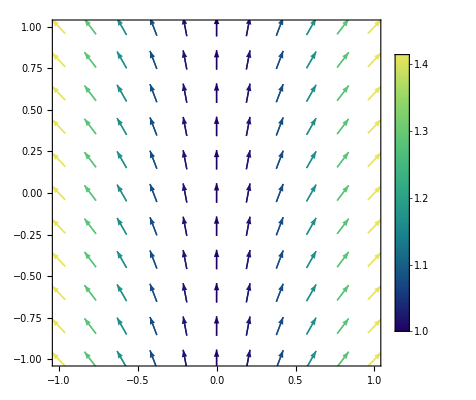

```mathematica
cartTestField[x_,y_,z_]:={x,1.0,0.0}
cartTestVectors=Table[{{x,y},cartTestField[x,y,z][[1;;2]]},{x,-1,1,0.2},{y,-1,1,0.2}];
ListVectorPlot[cartTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

```mathematica
garbageVariableUsedToDefineFunctions=rotateCartesianVector[cartTestField[#1,#2,#3],{ang1,ang2,ang3}]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{x0,y0,z0});
cartTestFieldRotated[x0_,y0_,z0_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

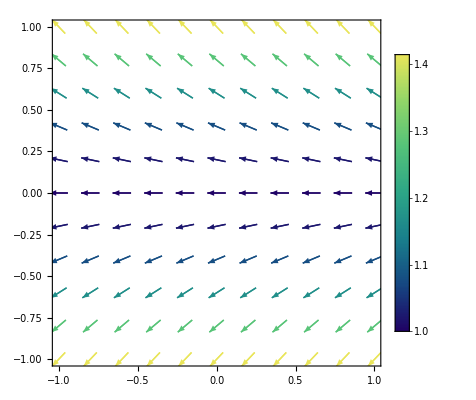

```mathematica
cartTestVectors=Table[{{x,y},cartTestFieldRotated[x,y,z,Pi/2.0,0.0,0.0][[1;;2]]},{x,-1,1,0.2},{y,-1,1,0.2}];
ListVectorPlot[cartTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

#### Test rotation functions with spherical vector field

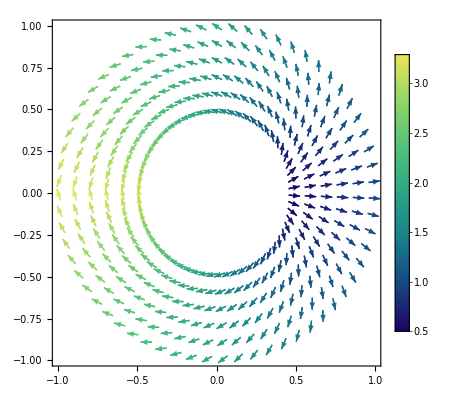

```mathematica
z=0.1;
myTestField[r_,θ_,ϕ_]:={r,0,ϕ}
myTestVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[myTestField[r,ArcTan[Sqrt[r^2-z^2]/z],phi],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,0.5,1.0,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",ColorFunctionScaling->False]
```

```mathematica
(* I think the following is finally correct *)
(* try and combine it all into one line *)
```

```mathematica
(* first convert the field to a cartesian field *)
(*cartesianTestField[x0_,y0_,z0_]:=Evaluate[spherevec2cartvec[myTestField[#1,#2,#3],ToSphericalCoordinates[{x0,y0,z0}]]&@@ToSphericalCoordinates[{x0,y0,z0}]]*)
```

```mathematica
(* rotate the cartesian vector field *)
(*garbageVariableUsedToDefineFunctions=rotateCartesianVector[cartesianTestField[#1,#2,#3],{ang1,ang2,ang3}]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{x0,y0,z0});
cartesianTestField[x0_,y0_,z0_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]*)
```

```mathematica
(* convert back to a spherical vector field *)
(*myTestFieldRotated[r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[rotate spherical vector field[myTestField[r,θ,ϕ]]]*)
```

```mathematica
(*garbageVariableUsedToDefineFunctions=rotateSphericalVector[myTestField[r,θ,ϕ],{r,θ,ϕ},{ang1,ang2,ang3}];*)
myTestFieldRotated[r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[Simplify[rotate spherical vector field[myTestField[r,θ,ϕ]]]]
(*Clear[garbageVariableUsedToDefineFunctions]*)
```

```mathematica
Simplify[myTestFieldRotated[r,θ,ϕ,a,b,c]]
```

{r,(4 r ArcTan[-r (Cos[a] (Cos[θ] Sin[b]-Cos[b] Cos[c-ϕ] Sin[θ])+Sin[a] Sin[θ] Sin[c-ϕ]),r (Cos[θ] Sin[a] Sin[b]-Sin[θ] (Cos[b] Cos[c-ϕ] Sin[a]+Cos[a] Sin[c-ϕ]))] Sin[b] Sin[c-ϕ])/(√(-r^2 (Cos[2 b] (2+6 Cos[2 θ]-2 Cos[2 (c-ϕ)]+Cos[2 (c-θ-ϕ)]+Cos[2 (c+θ-ϕ)])+2 (-5+Cos[2 c] Cos[2 ϕ]+4 Cos[c] Cos[ϕ] Sin[2 b] Sin[2 θ]+2 Cos[2 θ] Sin[c-ϕ]^2+4 Sin[2 b] Sin[c] Sin[2 θ] Sin[ϕ]+Sin[2 c] Sin[2 ϕ])))),-((4 r ArcTan[-r (Cos[a] (Cos[θ] Sin[b]-Cos[b] Cos[c-ϕ] Sin[θ])+Sin[a] Sin[θ] Sin[c-ϕ]),r (Cos[θ] Sin[a] Sin[b]-Sin[θ] (Cos[b] Cos[c-ϕ] Sin[a]+Cos[a] Sin[c-ϕ]))] (Cos[c] Cos[θ] Cos[ϕ] Sin[b]-Cos[b] Sin[θ]+Cos[θ] Sin[b] Sin[c] Sin[ϕ]))/(√(-r^2 (Cos[2 b] (2+6 Cos[2 θ]-2 Cos[2 (c-ϕ)]+Cos[2 (c-θ-ϕ)]+Cos[2 (c+θ-ϕ)])+2 (-5+Cos[2 c] Cos[2 ϕ]+4 Cos[c] Cos[ϕ] Sin[2 b] Sin[2 θ]+2 Cos[2 θ] Sin[c-ϕ]^2+4 Sin[2 b] Sin[c] Sin[2 θ] Sin[ϕ]+Sin[2 c] Sin[2 ϕ])))))}

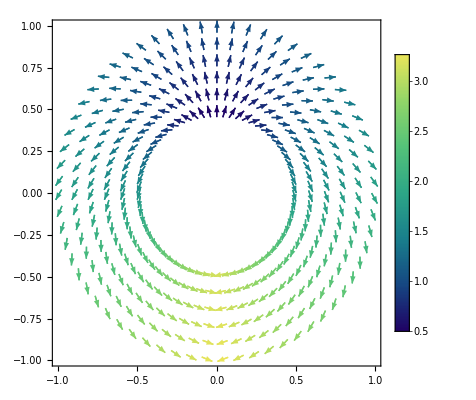

```mathematica
myTestVectorsRotated=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[myTestFieldRotated[r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,Pi/2.0],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,0.5,1.0,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myTestVectorsRotated,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",ColorFunctionScaling->False]
```

```mathematica
FullSimplify[myTestFieldRotated[r,theta,phi,a,b,c]]
```

{r,(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] Sin[b] Sin[c-phi])/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta]))),(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] (-Cos[c-phi] Cos[theta] Sin[b]+Cos[b] Sin[theta]))/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta])))}

```mathematica
FullSimplify[%]
```

{r,(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] Sin[b] Sin[c-phi])/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta]))),(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] (-Cos[c-phi] Cos[theta] Sin[b]+Cos[b] Sin[theta]))/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta])))}

```mathematica
myTestVectorsRotated=Table[{{r,theta,phi},myTestFieldRotated[r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,Pi/2.0,0.0]},{r,innerRadius,outerRadius,0.1},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
```

```mathematica
myTestVectorsRotated
```

{{{{{0.2,0.01,-3.13159},{0.2,-0.0624751,-3.12365}},{{0.2,0.01,-3.03159},{0.2,-0.637089,-2.88417}},{{0.2,0.01,-2.93159},{0.2,-1.09607,-2.57122}},{{0.2,0.01,-2.83159},{0.2,-1.4325,-2.23599}},56,{{0.2,0.01,2.86841},{0.2,-1.32208,2.35926}},{{0.2,0.01,2.96841},{0.2,-0.94171,2.69156}},{{0.2,0.01,3.06841},{0.2,-0.437509,2.98371}}},30,{1}}}
 |  |  |  |

#### Test on arbitrary field

```mathematica
rotate spherical vector field[{f1[r,θ,ϕ],f2[r,θ,ϕ],f3[r,θ,ϕ]}]
```

{1}
 |  |  |  |

Map Euler angles to points on a sphere

We want to take two Euler angles and use them to map to some point on a unit sphere. We should only need two, so it’s going to be useful to just use the first two: RollPitchYawMatrix[{α, β, 0}]. The issue here is just maintaining a consistency in the cross/plus polarization. I think it’s fine to just say that plus corresponds to γ = 0 and cross corresponds to γ = π/4. Let’s give this a shot.

α rotates about z axis
β rotates about y axis
γ rotates about z axis

```mathematica
(* α should range from 0 to π and β should range from 0 to 2π *)
eulerAngles={α,β,γ};

xhat={1,0,0};
yhat={0,1,0};
zhat={0,0,1};

xhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].xhat;
yhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].yhat;
zhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].zhat;

zInSpherical=Simplify[ToSphericalCoordinates[zhatp]];
θfnc[α_,β_,γ_]:=Evaluate[zInSpherical[[2]]];
ϕfnc[α_,β_,γ_]:=Evaluate[zInSpherical[[3]]];
euler2spherical[α_,β_,γ_]:={β,α}
euler2spherical3d[α_,β_,γ_]:={1.0,β,α}
```

Aitoff projection

```mathematica
(*aitoff[θ_,ϕ_]:={(2*Cos[θ+Pi/2]*Sin[ϕ/2])/Sinc[ArcCos[Cos[θ+Pi/2]*Cos[ϕ/2]]], Sin[θ+Pi/2]/Sinc[ArcCos[Cos[θ+Pi/2]*Cos[ϕ/2]]]}*)
Clear[aitoff]
aitoff[θ_,ϕ_]:={(2*Cos[θ-Pi/2]*Sin[ϕ/2])/Sinc[ArcCos[Cos[θ-Pi/2]*Cos[ϕ/2]]], Sin[θ-Pi/2]/Sinc[ArcCos[Cos[θ-Pi/2]*Cos[ϕ/2]]]}
```

# Single Spherical Shell Mechanical-EM Coupling

Import Resonant Frequencies

```mathematica
MODES1 =Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/NbCavity-r=0.2-0.005.txt"]]]];
MODES2=Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/NbCavity-r=0.2-0.005-real-high-n.txt"]]]];
MODES={Join[MODES1[[1]],MODES2[[1]]]};
waveNumbersK=Table[Quiet["wavenumberk"/.(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[If[m==2,2,0]]]/.MODES[[1]])],{m,0,10},{n,0,128}];
waveNumbersP=Table[Quiet["wavenumberp"/.(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[If[m==2,2,0]]]/.MODES[[1]])],{m,0,10},{n,0,128}];
```

```mathematica
"m2n12l2"/.MODES2[[1]]
```

{wavenumberk→5026.58,wavenumberp→2513.31,frequency→1.05147×10^7,C0→1.01514,C2→0.00158107,D0→0.0148835,D2→0.000818822}

```mathematica
MODES[[1]]
```

{m0n0l0→{wavenumberk→15.0644,wavenumberp→6.18401,frequency→31512.1,C0→0.238947,C2→0.0470891,D0→-0.509651,D2→0.663218},m0n1l0→{wavenumberk→628.396,wavenumberp→257.96,frequency→1.31449×10^6,C0→1.10148,C2→1.38106×10^12,D0→-0.260953,D2→4.34262×10^10},m0n2l0→{wavenumberk→1256.68,wavenumberp→515.872,frequency→2.62875×10^6,C0→0.880927,C2→5.12969×10^11,D0→-0.719972,D2→8.06467×10^9},m0n3l0→{wavenumberk→1530.66,wavenumberp→628.345,frequency→3.20188×10^6,C0→1.01513,C2→0.00522489,D0→0.0107581,D2→-0.00894184},m0n4l0→{wavenumberk→1884.98,wavenumberp→773.794,frequency→3.94305×10^6,C0→0.635576,C2→2.35744×10^10,D0→0.711882,D2→2.47083×10^8},m0n5l0→{wavenumberk→2513.29,wavenumberp→1031.72,frequency→5.25737×10^6,C0→0.935801,C2→-3.15751×10^11,D0→-0.0516008,D2→-2.48203×10^9},m0n6l0→{wavenumberk→3061.23,wavenumberp→1256.65,frequency→6.40355×10^6,C0→1.01519,C2→0.0138627,D0→0.00537913,D2→-0.00878627},m0n7l0→{wavenumberk→3141.61,wavenumberp→1289.65,frequency→6.57169×10^6,C0→0.923859,C2→-1.9087×10^11,D0→0.389259,D2→-1.2003×10^9},m0n8l0→{wavenumberk→3769.92,wavenumberp→1547.57,frequency→7.88602×10^6,C0→0.991705,C2→-2.89986×10^10,D0→-0.118061,D2→-1.51966×10^8},m0n9l0→{wavenumberk→4398.24,wavenumberp→1805.5,frequency→9.20035×10^6,C0→0.971587,C2→4.99191×10^8,D0→-0.36439,D2→2.24228×10^6},m0n10l0→{wavenumberk→4591.82,wavenumberp→1884.96,frequency→9.60528×10^6,C0→1.0152,C2→-0.00245803,D0→0.0035861,D2→0.000221173},m1n0l0→{wavenumberk→18.4456,wavenumberp→7.572,frequency→38584.9,C0→0.159801,C2→0.323946,D0→-0.281621,D2→0.321419},m1n0l1→{wavenumberk→18.4456,wavenumberp→7.572,frequency→38584.9,C0→0.159803,C2→0.323949,D0→-0.281623,D2→0.321421},m1n1l0→{wavenumberk→628.543,wavenumberp→258.02,frequency→1.3148×10^6,C0→0.0138513,C2→0.0494996,D0→0.00676147,D2→-0.715884},m1n1l1→{wavenumberk→628.543,wavenumberp→258.02,frequency→1.3148×10^6,C0→0.0138524,C2→0.0495035,D0→0.00676201,D2→-0.715941},m1n2l0→{wavenumberk→1256.63,wavenumberp→515.851,frequency→2.62864×10^6,C0→0.0116278,C2→-0.00672155,D0→0.0119658,D2→0.717761},m1n2l1→{wavenumberk→1256.63,wavenumberp→515.851,frequency→2.62864×10^6,C0→0.0116286,C2→-0.00672205,D0→0.0119667,D2→0.717813},m1n3l0→{wavenumberk→1530.8,wavenumberp→628.4,frequency→3.20216×10^6,C0→0.030144,C2→-0.00877221,D0→-1.01457,D2→-0.00549287},m1n3l1→{wavenumberk→1530.8,wavenumberp→628.4,frequency→3.20216×10^6,C0→0.0301445,C2→-0.00877234,D0→-1.01458,D2→-0.00549296},m1n4l0→{wavenumberk→1884.99,wavenumberp→773.798,frequency→3.94307×10^6,C0→0.00130951,C2→-0.0107879,D0→0.00303598,D2→0.717775},m1n4l1→{wavenumberk→1884.99,wavenumberp→773.798,frequency→3.94307×10^6,C0→0.0013095,C2→-0.0107878,D0→0.00303596,D2→0.717769},m1n5l0→{wavenumberk→2513.31,wavenumberp→1031.73,frequency→5.2574×10^6,C0→0.0000985928,C2→0.00892877,D0→-0.0027369,D2→-0.717802},m1n5l1→{wavenumberk→2513.31,wavenumberp→1031.73,frequency→5.2574×10^6,C0→0.0000986016,C2→0.00892958,D0→-0.00273714,D2→-0.717867},m1n6l0→{wavenumberk→3061.24,wavenumberp→1256.65,frequency→6.40357×10^6,C0→0.0099048,C2→-0.00874344,D0→-1.01489,D2→-0.0138843},m1n6l1→{wavenumberk→3061.24,wavenumberp→1256.65,frequency→6.40357×10^6,C0→0.0099042,C2→-0.00874291,D0→-1.01483,D2→-0.0138834},m1n7l0→{wavenumberk→3141.66,wavenumberp→1289.67,frequency→6.57179×10^6,C0→0.00901353,C2→0.0124768,D0→-0.0205983,D2→-0.717561},m1n7l1→{wavenumberk→3141.66,wavenumberp→1289.67,frequency→6.57179×10^6,C0→0.0090132,C2→0.0124763,D0→-0.0205975,D2→-0.717535},m1n8l0→{wavenumberk→3769.93,wavenumberp→1547.57,frequency→7.88603×10^6,C0→0.00139377,C2→-0.00509391,D0→-0.00138959,D2→0.68332},m1n8l1→{wavenumberk→3769.93,wavenumberp→1547.57,frequency→7.88603×10^6,C0→0.00146418,C2→-0.00535123,D0→-0.00145979,D2→0.717837},m1n9l0→{wavenumberk→4398.25,wavenumberp→1805.5,frequency→9.20036×10^6,C0→0.00128604,C2→-0.00488492,D0→-0.000419703,D2→0.717849},m1n9l1→{wavenumberk→4398.25,wavenumberp→1805.5,frequency→9.20036×10^6,C0→0.00128602,C2→-0.00488487,D0→-0.000419699,D2→0.717842},m1n10l0→{wavenumberk→4591.85,wavenumberp→1884.98,frequency→9.60534×10^6,C0→0.00874178,C2→0.000203796,D0→-1.01515,D2→0.00245955},m1n10l1→{wavenumberk→4591.85,wavenumberp→1884.98,frequency→9.60534×10^6,C0→0.00874191,C2→0.000203799,D0→-1.01517,D2→0.00245959},m2n0l0→{wavenumberk→5.93237,wavenumberp→2.43527,frequency→12409.5,C0→47.2665,C2→3.46597,D0→0.0191603,D2→-0.127017},m2n0l1→{wavenumberk→5.93237,wavenumberp→2.43527,frequency→12409.5,C0→47.2641,C2→3.46579,D0→0.0191593,D2→-0.12701},m2n0l2→{wavenumberk→5.93237,wavenumberp→2.43527,frequency→12409.5,C0→47.2684,C2→3.46611,D0→0.0191611,D2→-0.127022},m2n1l0→{wavenumberk→25.0844,wavenumberp→10.2973,frequency→52472.3,C0→0.358744,C2→0.19041,D0→-0.148297,D2→0.160171},m2n1l1→{wavenumberk→25.0844,wavenumberp→10.2973,frequency→52472.3,C0→0.35877,C2→0.190423,D0→-0.148307,D2→0.160182},m2n1l2→{wavenumberk→25.0844,wavenumberp→10.2973,frequency→52472.3,C0→0.358757,C2→0.190417,D0→-0.148302,D2→0.160176},m2n2l0→{wavenumberk→628.837,wavenumberp→258.141,frequency→1.31542×10^6,C0→0.0131795,C2→-0.409741,D0→-0.0231921,D2→-0.0594925},m2n2l1→{wavenumberk→628.837,wavenumberp→258.141,frequency→1.31542×10^6,C0→0.0131806,C2→-0.409777,D0→-0.0231941,D2→-0.0594977},m2n2l2→{wavenumberk→628.837,wavenumberp→258.141,frequency→1.31542×10^6,C0→0.0131789,C2→-0.409722,D0→-0.023191,D2→-0.0594898},m2n3l0→{wavenumberk→1256.52,wavenumberp→515.809,frequency→2.62843×10^6,C0→0.0209129,C2→0.414325,D0→-0.0198907,D2→-0.00136697},m2n3l1→{wavenumberk→1256.52,wavenumberp→515.809,frequency→2.62843×10^6,C0→0.0209153,C2→0.414372,D0→-0.019893,D2→-0.00136712},m2n3l2→{wavenumberk→1256.52,wavenumberp→515.809,frequency→2.62843×10^6,C0→0.0209128,C2→0.414323,D0→-0.0198906,D2→-0.00136696},m2n4l0→{wavenumberk→1531.07,wavenumberp→628.511,frequency→3.20273×10^6,C0→1.01236,C2→0.00601194,D0→0.0688355,D2→-0.00840962},m2n4l1→{wavenumberk→1531.07,wavenumberp→628.511,frequency→3.20273×10^6,C0→1.0123,C2→0.00601159,D0→0.0688316,D2→-0.00840914},m2n4l2→{wavenumberk→1531.07,wavenumberp→628.511,frequency→3.20273×10^6,C0→1.01242,C2→0.00601229,D0→0.0688396,D2→-0.00841012},m2n5l0→{wavenumberk→1885.01,wavenumberp→773.806,frequency→3.94311×10^6,C0→0.00528945,C2→0.414278,D0→-0.00219212,D2→0.0099965},m2n5l1→{wavenumberk→1885.01,wavenumberp→773.806,frequency→3.94311×10^6,C0→0.00529032,C2→0.414346,D0→-0.00219247,D2→0.00999814},m2n5l2→{wavenumberk→1885.01,wavenumberp→773.806,frequency→3.94311×10^6,C0→0.00528982,C2→0.414307,D0→-0.00219227,D2→0.00999719},m2n6l0→{wavenumberk→2513.33,wavenumberp→1031.74,frequency→5.25745×10^6,C0→0.004738,C2→0.414327,D0→0.000226286,D2→0.00894851},m2n6l1→{wavenumberk→2513.33,wavenumberp→1031.74,frequency→5.25745×10^6,C0→0.00473861,C2→0.41438,D0→0.000226315,D2→0.00894966},m2n6l2→{wavenumberk→2513.33,wavenumberp→1031.74,frequency→5.25745×10^6,C0→0.0047381,C2→0.414336,D0→0.000226291,D2→0.00894872},m2n7l0→{wavenumberk→3061.25,wavenumberp→1256.66,frequency→6.40359×10^6,C0→1.01428,C2→0.0139277,D0→0.0189499,D2→-0.0086581},m2n7l1→{wavenumberk→3061.25,wavenumberp→1256.66,frequency→6.40359×10^6,C0→1.01419,C2→0.0139266,D0→0.0189483,D2→-0.0086574},m2n7l2→{wavenumberk→3061.25,wavenumberp→1256.66,frequency→6.40359×10^6,C0→1.01431,C2→0.0139281,D0→0.0189505,D2→-0.00865839},m2n8l0→{wavenumberk→3141.75,wavenumberp→1289.7,frequency→6.57199×10^6,C0→0.0354107,C2→0.413803,D0→0.0161528,D2→0.0163864},m2n8l1→{wavenumberk→3141.75,wavenumberp→1289.7,frequency→6.57199×10^6,C0→0.03541,C2→0.413795,D0→0.0161525,D2→0.0163861},m2n8l2→{wavenumberk→3141.75,wavenumberp→1289.7,frequency→6.57199×10^6,C0→0.0354091,C2→0.413784,D0→0.0161521,D2→0.0163857},m2n9l0→{wavenumberk→3769.94,wavenumberp→1547.58,frequency→7.88605×10^6,C0→0.00246841,C2→-0.407537,D0→0.00251136,D2→-0.00484293},m2n9l1→{wavenumberk→3769.94,wavenumberp→1547.58,frequency→7.88605×10^6,C0→0.0018248,C2→-0.301276,D0→0.00185655,D2→-0.00358019},m2n9l2→{wavenumberk→3769.94,wavenumberp→1547.58,frequency→7.88605×10^6,C0→0.00251002,C2→-0.414406,D0→0.00255369,D2→-0.00492456},m2n10l0→{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000712607,C2→-0.414429,D0→0.00223211,D2→-0.00473753},m2n10l1→{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000712575,C2→-0.414411,D0→0.00223201,D2→-0.00473731},m2n10l2→{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000712574,C2→-0.41441,D0→0.00223201,D2→-0.00473731},m3n0l0→{wavenumberk→33.1703,wavenumberp→13.6166,frequency→69386.5,C0→0.468805,C2→0.0930767,D0→-0.106233,D2→0.115468},m3n0l1→{wavenumberk→33.1703,wavenumberp→13.6166,frequency→69386.5,C0→0.468794,C2→0.0930746,D0→-0.106231,D2→0.115465},m3n0l2→{wavenumberk→33.1703,wavenumberp→13.6166,frequency→69386.5,C0→0.468818,C2→0.0930793,D0→-0.106236,D2→0.115471},m3n0l3→{wavenumberk→33.1703,wavenumberp→13.6166,frequency→69386.5,C0→0.470959,C2→0.0935043,D0→-0.106721,D2→0.115998},m3n1l0→{wavenumberk→629.276,wavenumberp→258.321,frequency→1.31634×10^6,C0→0.0308701,C2→0.0742886,D0→0.0216055,D2→-0.282905},m3n1l1→{wavenumberk→629.276,wavenumberp→258.321,frequency→1.31634×10^6,C0→0.0316317,C2→0.0761215,D0→0.0221385,D2→-0.289885},m3n1l2→{wavenumberk→629.276,wavenumberp→258.321,frequency→1.31634×10^6,C0→0.0308679,C2→0.0742834,D0→0.0216039,D2→-0.282885},m3n1l3→{wavenumberk→629.276,wavenumberp→258.321,frequency→1.31634×10^6,C0→0.031104,C2→0.0748516,D0→0.0217692,D2→-0.285049},m3n2l0→{wavenumberk→1256.37,wavenumberp→515.747,frequency→2.62811×10^6,C0→0.0275986,C2→0.00649471,D0→0.029971,D2→0.292844},m3n2l1→{wavenumberk→1256.37,wavenumberp→515.747,frequency→2.62811×10^6,C0→0.0282763,C2→0.00665418,D0→0.0307069,D2→0.300034},m3n2l2→{wavenumberk→1256.37,wavenumberp→515.747,frequency→2.62811×10^6,C0→0.027597,C2→0.00649433,D0→0.0299692,D2→0.292826},m3n2l3→{wavenumberk→1256.37,wavenumberp→515.747,frequency→2.62811×10^6,C0→0.0290405,C2→0.00683402,D0→0.0315368,D2→0.308143},m3n3l0→{wavenumberk→1531.47,wavenumberp→628.677,frequency→3.20357×10^6,C0→0.126561,C2→-0.00780933,D0→-1.00625,D2→-0.00674428},m3n3l1→{wavenumberk→1531.47,wavenumberp→628.677,frequency→3.20357×10^6,C0→0.126567,C2→-0.00780972,D0→-1.0063,D2→-0.00674462},m3n3l2→{wavenumberk→1531.47,wavenumberp→628.677,frequency→3.20357×10^6,C0→0.126588,C2→-0.00781098,D0→-1.00646,D2→-0.0067457},m3n3l3→{wavenumberk→1531.47,wavenumberp→628.677,frequency→3.20357×10^6,C0→0.113593,C2→-0.00700917,D0→-0.903149,D2→-0.00605324},m3n4l0→{wavenumberk→1885.04,wavenumberp→773.818,frequency→3.94317×10^6,C0→0.00293867,C2→-0.0110668,D0→0.00754558,D2→0.292849},m3n4l1→{wavenumberk→1885.04,wavenumberp→773.818,frequency→3.94317×10^6,C0→0.00301126,C2→-0.0113402,D0→0.00773196,D2→0.300082},m3n4l2→{wavenumberk→1885.04,wavenumberp→773.818,frequency→3.94317×10^6,C0→0.0029384,C2→-0.0110658,D0→0.0075449,D2→0.292822},m3n4l3→{wavenumberk→1885.04,wavenumberp→773.818,frequency→3.94317×10^6,C0→0.00296097,C2→-0.0111508,D0→0.00760284,D2→0.295071},m3n5l0→{wavenumberk→2513.37,wavenumberp→1031.75,frequency→5.25753×10^6,C0→0.000437772,C2→0.0103513,D0→-0.00669479,D2→-0.292876},m3n5l1→{wavenumberk→2513.37,wavenumberp→1031.75,frequency→5.25753×10^6,C0→0.00044858,C2→0.0106069,D0→-0.00686008,D2→-0.300107},m3n5l2→{wavenumberk→2513.37,wavenumberp→1031.75,frequency→5.25753×10^6,C0→0.000437749,C2→0.0103508,D0→-0.00669443,D2→-0.29286},m3n5l3→{wavenumberk→2513.37,wavenumberp→1031.75,frequency→5.25753×10^6,C0→0.000460874,C2→0.0108976,D0→-0.00704809,D2→-0.308331},m3n6l0→{wavenumberk→3061.27,wavenumberp→1256.67,frequency→6.40363×10^6,C0→0.0324964,C2→-0.00852876,D0→-1.0131,D2→-0.0139904},m3n6l1→{wavenumberk→3061.27,wavenumberp→1256.67,frequency→6.40363×10^6,C0→0.0324979,C2→-0.00852917,D0→-1.01315,D2→-0.0139911},m3n6l2→{wavenumberk→3061.27,wavenumberp→1256.67,frequency→6.40363×10^6,C0→0.0325044,C2→-0.00853087,D0→-1.01335,D2→-0.0139939},m3n6l3→{wavenumberk→3061.27,wavenumberp→1256.67,frequency→6.40363×10^6,C0→0.0291718,C2→-0.00765621,D0→-0.909455,D2→-0.0125591},m3n7l0→{wavenumberk→3141.89,wavenumberp→1289.76,frequency→6.57228×10^6,C0→0.0239784,C2→0.0213004,D0→-0.0494905,D2→-0.291818},m3n7l1→{wavenumberk→3141.89,wavenumberp→1289.76,frequency→6.57228×10^6,C0→0.0245728,C2→0.0218284,D0→-0.0507174,D2→-0.299052},m3n7l2→{wavenumberk→3141.89,wavenumberp→1289.76,frequency→6.57228×10^6,C0→0.0239778,C2→0.0212998,D0→-0.0494892,D2→-0.29181},m3n7l3→{wavenumberk→3141.89,wavenumberp→1289.76,frequency→6.57228×10^6,C0→0.0241604,C2→0.021462,D0→-0.0498661,D2→-0.294033},m3n8l0→{wavenumberk→3769.95,wavenumberp→1547.58,frequency→7.88608×10^6,C0→0.00354491,C2→-0.00527402,D0→-0.00341058,D2→0.284653},m3n8l1→{wavenumberk→3769.95,wavenumberp→1547.58,frequency→7.88608×10^6,C0→0.00347867,C2→-0.00517547,D0→-0.00334685,D2→0.279334},m3n8l2→{wavenumberk→3769.95,wavenumberp→1547.58,frequency→7.88608×10^6,C0→0.00346324,C2→-0.00515252,D0→-0.00333201,D2→0.278095},m3n8l3→{wavenumberk→3769.95,wavenumberp→1547.58,frequency→7.88608×10^6,C0→0.00358663,C2→-0.00533609,D0→-0.00345072,D2→0.288003},m3n9l0→{wavenumberk→4398.28,wavenumberp→1805.51,frequency→9.20042×10^6,C0→0.00316635,C2→-0.00538347,D0→-0.000977311,D2→0.293021},m3n9l1→{wavenumberk→4398.28,wavenumberp→1805.51,frequency→9.20042×10^6,C0→0.00324453,C2→-0.00551639,D0→-0.00100144,D2→0.300256},m3n9l2→{wavenumberk→4398.28,wavenumberp→1805.51,frequency→9.20042×10^6,C0→0.00316611,C2→-0.00538305,D0→-0.000977235,D2→0.292998},m3n9l3→{wavenumberk→4398.28,wavenumberp→1805.51,frequency→9.20042×10^6,C0→0.00319038,C2→-0.00542431,D0→-0.000984727,D2→0.295244},m3n10l0→{wavenumberk→4591.99,wavenumberp→1885.04,frequency→9.60565×10^6,C0→0.0345108,C2→0.000116781,D0→-1.01453,D2→0.00246537},m3n10l1→{wavenumberk→4591.99,wavenumberp→1885.04,frequency→9.60565×10^6,C0→0.0345127,C2→0.000116787,D0→-1.01459,D2→0.0024655},m3n10l2→{wavenumberk→4591.99,wavenumberp→1885.04,frequency→9.60565×10^6,C0→0.0345194,C2→0.00011681,D0→-1.01478,D2→0.00246598},m3n10l3→{wavenumberk→4591.99,wavenumberp→1885.04,frequency→9.60565×10^6,C0→0.0309719,C2→0.000104805,D0→-0.910497,D2→0.00221255},m4n0l0→{wavenumberk→7.63333,wavenumberp→3.13352,frequency→15967.6,C0→7498.24,C2→49.3032,D0→0.000930824,D2→-0.0182259},m4n0l1→{wavenumberk→7.63333,wavenumberp→3.13352,frequency→15967.6,C0→7497.6,C2→49.299,D0→0.000930745,D2→-0.0182243},m4n0l2→{wavenumberk→7.63333,wavenumberp→3.13352,frequency→15967.6,C0→7498.26,C2→49.3034,D0→0.000930827,D2→-0.0182259},m4n0l3→{wavenumberk→7.63333,wavenumberp→3.13352,frequency→15967.6,C0→7185.11,C2→47.2443,D0→0.000891953,D2→-0.0174647},m4n0l4→{wavenumberk→7.63333,wavenumberp→3.13352,frequency→15967.6,C0→7488.88,C2→49.2417,D0→0.000929664,D2→-0.0182031},m4n1l0→{wavenumberk→41.7298,wavenumberp→17.1303,frequency→87291.3,C0→0.549079,C2→0.0365542,D0→-0.0862858,D2→0.0939711},m4n1l1→{wavenumberk→41.7298,wavenumberp→17.1303,frequency→87291.3,C0→0.549127,C2→0.0365574,D0→-0.0862933,D2→0.0939793},m4n1l2→{wavenumberk→41.7298,wavenumberp→17.1303,frequency→87291.3,C0→0.549073,C2→0.0365538,D0→-0.0862849,D2→0.0939702},m4n1l3→{wavenumberk→41.7298,wavenumberp→17.1303,frequency→87291.3,C0→0.565902,C2→0.0376742,D0→-0.0889295,D2→0.0968503},m4n1l4→{wavenumberk→41.7298,wavenumberp→17.1303,frequency→87291.3,C0→0.549115,C2→0.0365566,D0→-0.0862915,D2→0.0939774},m4n2l0→{wavenumberk→629.862,wavenumberp→258.561,frequency→1.31756×10^6,C0→0.0325893,C2→-0.207809,D0→-0.0360039,D2→-0.0895081},m4n2l1→{wavenumberk→629.862,wavenumberp→258.561,frequency→1.31756×10^6,C0→0.0325925,C2→-0.207829,D0→-0.0360075,D2→-0.089517},m4n2l2→{wavenumberk→629.862,wavenumberp→258.561,frequency→1.31756×10^6,C0→0.032589,C2→-0.207807,D0→-0.0360036,D2→-0.0895073},m4n2l3→{wavenumberk→629.862,wavenumberp→258.561,frequency→1.31756×10^6,C0→0.0339049,C2→-0.216198,D0→-0.0374574,D2→-0.0931214},m4n2l4→{wavenumberk→629.862,wavenumberp→258.561,frequency→1.31756×10^6,C0→0.032592,C2→-0.207826,D0→-0.0360069,D2→-0.0895155},m4n3l0→{wavenumberk→1256.17,wavenumberp→515.665,frequency→2.62769×10^6,C0→0.039353,C2→0.226547,D0→-0.034696,D2→-0.0106825},m4n3l1→{wavenumberk→1256.17,wavenumberp→515.665,frequency→2.62769×10^6,C0→0.039357,C2→0.226571,D0→-0.0346995,D2→-0.0106835},m4n3l2→{wavenumberk→1256.17,wavenumberp→515.665,frequency→2.62769×10^6,C0→0.0393526,C2→0.226545,D0→-0.0346956,D2→-0.0106823},m4n3l3→{wavenumberk→1256.17,wavenumberp→515.665,frequency→2.62769×10^6,C0→0.0406925,C2→0.234259,D0→-0.035877,D2→-0.0110461},m4n3l4→{wavenumberk→1256.17,wavenumberp→515.665,frequency→2.62769×10^6,C0→0.0393609,C2→0.226593,D0→-0.0347029,D2→-0.0106846},m4n4l0→{wavenumberk→1532.01,wavenumberp→628.899,frequency→3.2047×10^6,C0→0.993146,C2→0.00762706,D0→0.202684,D2→-0.006914},m4n4l1→{wavenumberk→1532.01,wavenumberp→628.899,frequency→3.2047×10^6,C0→0.993047,C2→0.0076263,D0→0.202664,D2→-0.00691331},m4n4l2→{wavenumberk→1532.01,wavenumberp→628.899,frequency→3.2047×10^6,C0→0.99314,C2→0.00762701,D0→0.202683,D2→-0.00691396},m4n4l3→{wavenumberk→1532.01,wavenumberp→628.899,frequency→3.2047×10^6,C0→0.944679,C2→0.00725484,D0→0.192793,D2→-0.00657658},m4n4l4→{wavenumberk→1532.01,wavenumberp→628.899,frequency→3.2047×10^6,C0→0.991659,C2→0.00761564,D0→0.202381,D2→-0.00690364},m4n5l0→{wavenumberk→1885.08,wavenumberp→773.834,frequency→3.94325×10^6,C0→0.00984312,C2→0.226603,D0→-0.00351194,D2→0.0126967},m4n5l1→{wavenumberk→1885.08,wavenumberp→773.834,frequency→3.94325×10^6,C0→0.00984503,C2→0.226647,D0→-0.00351263,D2→0.0126992},m4n5l2→{wavenumberk→1885.08,wavenumberp→773.834,frequency→3.94325×10^6,C0→0.0098439,C2→0.226621,D0→-0.00351222,D2→0.0126977},m4n5l3→{wavenumberk→1885.08,wavenumberp→773.834,frequency→3.94325×10^6,C0→0.0102375,C2→0.235683,D0→-0.00365267,D2→0.0132054},m4n5l4→{wavenumberk→1885.08,wavenumberp→773.834,frequency→3.94325×10^6,C0→0.00984457,C2→0.226637,D0→-0.00351246,D2→0.0126986},m4n6l0→{wavenumberk→2513.42,wavenumberp→1031.77,frequency→5.25764×10^6,C0→0.00862741,C2→0.226655,D0→0.000767515,D2→0.0121701},m4n6l1→{wavenumberk→2513.42,wavenumberp→1031.77,frequency→5.25764×10^6,C0→0.00862827,C2→0.226677,D0→0.000767592,D2→0.0121714},m4n6l2→{wavenumberk→2513.42,wavenumberp→1031.77,frequency→5.25764×10^6,C0→0.00862734,C2→0.226653,D0→0.000767509,D2→0.01217},m4n6l3→{wavenumberk→2513.42,wavenumberp→1031.77,frequency→5.25764×10^6,C0→0.00892393,C2→0.234445,D0→0.000793894,D2→0.0125884},m4n6l4→{wavenumberk→2513.42,wavenumberp→1031.77,frequency→5.25764×10^6,C0→0.00862961,C2→0.226713,D0→0.000767711,D2→0.0121733},m4n7l0→{wavenumberk→3061.29,wavenumberp→1256.68,frequency→6.40369×10^6,C0→1.01141,C2→0.0140744,D0→0.0505248,D2→-0.00835681},m4n7l1→{wavenumberk→3061.29,wavenumberp→1256.68,frequency→6.40369×10^6,C0→1.01131,C2→0.0140729,D0→0.0505197,D2→-0.00835597},m4n7l2→{wavenumberk→3061.29,wavenumberp→1256.68,frequency→6.40369×10^6,C0→1.01141,C2→0.0140743,D0→0.0505247,D2→-0.00835679},m4n7l3→{wavenumberk→3061.29,wavenumberp→1256.68,frequency→6.40369×10^6,C0→0.961987,C2→0.0133866,D0→0.0480559,D2→-0.00794846},m4n7l4→{wavenumberk→3061.29,wavenumberp→1256.68,frequency→6.40369×10^6,C0→1.00987,C2→0.0140529,D0→0.0504479,D2→-0.00834409},m4n8l0→{wavenumberk→3142.08,wavenumberp→1289.84,frequency→6.57268×10^6,C0→0.0628147,C2→0.224792,D0→0.0328716,D2→0.0264741},m4n8l1→{wavenumberk→3142.08,wavenumberp→1289.84,frequency→6.57268×10^6,C0→0.0628298,C2→0.224846,D0→0.0328795,D2→0.0264804},m4n8l2→{wavenumberk→3142.08,wavenumberp→1289.84,frequency→6.57268×10^6,C0→0.0628179,C2→0.224803,D0→0.0328732,D2→0.0264754},m4n8l3→{wavenumberk→3142.08,wavenumberp→1289.84,frequency→6.57268×10^6,C0→0.061646,C2→0.220609,D0→0.03226,D2→0.0259815},m4n8l4→{wavenumberk→3142.08,wavenumberp→1289.84,frequency→6.57268×10^6,C0→0.0628029,C2→0.22475,D0→0.0328654,D2→0.0264691},m4n9l0→{wavenumberk→3769.97,wavenumberp→1547.59,frequency→7.88611×10^6,C0→0.00426886,C2→-0.21699,D0→0.00456542,D2→-0.0059435},m4n9l1→{wavenumberk→3769.97,wavenumberp→1547.59,frequency→7.88611×10^6,C0→0.00352239,C2→-0.179047,D0→0.00376709,D2→-0.00490419},m4n9l2→{wavenumberk→3769.97,wavenumberp→1547.59,frequency→7.88611×10^6,C0→0.00426005,C2→-0.216543,D0→0.004556,D2→-0.00593123},m4n9l3→{wavenumberk→3769.97,wavenumberp→1547.59,frequency→7.88611×10^6,C0→0.00459897,C2→-0.23377,D0→0.00491846,D2→-0.0064031},m4n9l4→{wavenumberk→3769.97,wavenumberp→1547.59,frequency→7.88611×10^6,C0→0.00434482,C2→-0.220851,D0→0.00464665,D2→-0.00604925},m4n10l0→{wavenumberk→4398.3,wavenumberp→1805.52,frequency→9.20047×10^6,C0→0.00120885,C2→-0.226887,D0→0.00410303,D2→-0.00626886},m4n10l1→{wavenumberk→4398.3,wavenumberp→1805.52,frequency→9.20047×10^6,C0→0.00120905,C2→-0.226926,D0→0.00410374,D2→-0.00626994},m4n10l2→{wavenumberk→4398.3,wavenumberp→1805.52,frequency→9.20047×10^6,C0→0.00120888,C2→-0.226893,D0→0.00410313,D2→-0.00626902},m4n10l3→{wavenumberk→4398.3,wavenumberp→1805.52,frequency→9.20047×10^6,C0→0.00120539,C2→-0.226239,D0→0.0040913,D2→-0.00625095},m4n10l4→{wavenumberk→4398.3,wavenumberp→1805.52,frequency→9.20047×10^6,C0→0.00120905,C2→-0.226926,D0→0.00410373,D2→-0.00626993},m5n0l0→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→121651.,C2→267.351,D0→0.000104659,D2→-0.00402199},m5n0l1→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→121660.,C2→267.369,D0→0.000104666,D2→-0.00402226},m5n0l2→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→120372.,C2→264.539,D0→0.000103558,D2→-0.00397969},m5n0l3→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→95929.4,C2→210.822,D0→0.0000825298,D2→-0.00317158},m5n0l4→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→121661.,C2→267.373,D0→0.000104667,D2→-0.00402232},m5n0l5→{wavenumberk→7.97624,wavenumberp→3.27429,frequency→16684.9,C0→121630.,C2→267.303,D0→0.00010464,D2→-0.00402127},m5n1l0→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.629921,C2→0.00016713,D0→-0.0731025,D2→0.0752812},m5n1l1→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.629883,C2→0.00016712,D0→-0.073098,D2→0.0752766},m5n1l2→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.629962,C2→0.000167141,D0→-0.0731071,D2→0.075286},m5n1l3→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.637323,C2→0.000169094,D0→-0.0739615,D2→0.0761658},m5n1l4→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.629637,C2→0.000167055,D0→-0.0730694,D2→0.0752472},m5n1l5→{wavenumberk→50.4721,wavenumberp→20.719,frequency→105579.,C0→0.624471,C2→0.000165684,D0→-0.0724699,D2→0.0746298},m5n2l0→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.0372882,C2→0.103207,D0→0.0461922,D2→-0.152903},m5n2l1→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.0372827,C2→0.103191,D0→0.0461853,D2→-0.15288},m5n2l2→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.0372887,C2→0.103208,D0→0.0461929,D2→-0.152905},m5n2l3→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.0382983,C2→0.106003,D0→0.0474436,D2→-0.157045},m5n2l4→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.037266,C2→0.103145,D0→0.0461647,D2→-0.152812},m5n2l5→{wavenumberk→630.592,wavenumberp→258.861,frequency→1.31909×10^6,C0→0.0370298,C2→0.102491,D0→0.045872,D2→-0.151843},m5n3l0→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0410445,C2→0.0144143,D0→0.0491877,D2→0.18456},m5n3l1→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0410387,C2→0.0144123,D0→0.0491809,D2→0.184534},m5n3l2→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0410451,C2→0.0144145,D0→0.0491885,D2→0.184563},m5n3l3→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0467727,C2→0.016426,D0→0.0560525,D2→0.210318},m5n3l4→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0410198,C2→0.0144056,D0→0.0491581,D2→0.184449},m5n3l5→{wavenumberk→1255.92,wavenumberp→515.562,frequency→2.62717×10^6,C0→0.0406835,C2→0.0142875,D0→0.0487552,D2→0.182937},m5n4l0→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.295797,C2→-0.00565993,D0→-0.968547,D2→-0.00856061},m5n4l1→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.29583,C2→-0.00566056,D0→-0.968654,D2→-0.00856156},m5n4l2→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.294164,C2→-0.00562869,D0→-0.963202,D2→-0.00851337},m5n4l3→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.201788,C2→-0.00386111,D0→-0.660727,D2→-0.00583991},m5n4l4→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.295791,C2→-0.00565982,D0→-0.968528,D2→-0.00856045},m5n4l5→{wavenumberk→1532.68,wavenumberp→629.175,frequency→3.20611×10^6,C0→0.295753,C2→-0.00565908,D0→-0.968402,D2→-0.00855933},m5n5l0→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.0038666,C2→-0.0145764,D0→0.0122021,D2→0.184768},m5n5l1→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.00386615,C2→-0.0145748,D0→0.0122007,D2→0.184747},m5n5l2→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.00386666,C2→-0.0145767,D0→0.0122023,D2→0.184771},m5n5l3→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.00397256,C2→-0.0149759,D0→0.0125364,D2→0.189831},m5n5l4→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.00386432,C2→-0.0145679,D0→0.0121949,D2→0.184659},m5n5l5→{wavenumberk→1885.12,wavenumberp→773.853,frequency→3.94335×10^6,C0→0.00383639,C2→-0.0144626,D0→0.0121067,D2→0.183324},m5n6l0→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00124932,C2→0.0141721,D0→-0.0105365,D2→-0.184802},m5n6l1→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00124914,C2→0.01417,D0→-0.010535,D2→-0.184775},m5n6l2→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00124932,C2→0.0141721,D0→-0.0105365,D2→-0.184802},m5n6l3→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00142813,C2→0.0162004,D0→-0.0120446,D2→-0.211252},m5n6l4→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00124821,C2→0.0141595,D0→-0.0105272,D2→-0.184638},m5n6l5→{wavenumberk→2513.49,wavenumberp→1031.8,frequency→5.25777×10^6,C0→0.00123699,C2→0.0140322,D0→-0.0104326,D2→-0.182978},m5n7l0→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0729793,C2→-0.00813901,D0→-1.00864,D2→-0.0141737},m5n7l1→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0729885,C2→-0.00814004,D0→-1.00877,D2→-0.0141755},m5n7l2→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0726076,C2→-0.00809756,D0→-1.00351,D2→-0.0141015},m5n7l3→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0497765,C2→-0.00555132,D0→-0.687959,D2→-0.00966733},m5n7l4→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0729857,C2→-0.00813973,D0→-1.00873,D2→-0.0141749},m5n7l5→{wavenumberk→3061.33,wavenumberp→1256.69,frequency→6.40375×10^6,C0→0.0729686,C2→-0.00813782,D0→-1.0085,D2→-0.0141716},m5n8l0→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.0431536,C2→0.0317211,D0→-0.0752304,D2→-0.181873},m5n8l1→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.0431554,C2→0.0317225,D0→-0.0752336,D2→-0.181881},m5n8l2→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.0431482,C2→0.0317172,D0→-0.075221,D2→-0.181851},m5n8l3→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.0433093,C2→0.0318356,D0→-0.0755018,D2→-0.182529},m5n8l4→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.043131,C2→0.0317045,D0→-0.0751909,D2→-0.181778},m5n8l5→{wavenumberk→3142.31,wavenumberp→1289.94,frequency→6.57317×10^6,C0→0.0428787,C2→0.0315191,D0→-0.0747512,D2→-0.180715},m5n9l0→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.0057597,C2→-0.00690666,D0→-0.00519644,D2→0.179504},m5n9l1→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.00567692,C2→-0.00680739,D0→-0.00512175,D2→0.176924},m5n9l2→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.00459234,C2→-0.00550684,D0→-0.00414324,D2→0.143123},m5n9l3→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.00565009,C2→-0.00677522,D0→-0.00509755,D2→0.176088},m5n9l4→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.00563735,C2→-0.00675994,D0→-0.00508605,D2→0.175691},m5n9l5→{wavenumberk→3769.99,wavenumberp→1547.6,frequency→7.88616×10^6,C0→0.00587025,C2→-0.00703923,D0→-0.00529618,D2→0.182949},m5n10l0→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.00504908,C2→-0.0072617,D0→-0.00139976,D2→0.185205},m5n10l1→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.00504852,C2→-0.0072609,D0→-0.0013996,D2→0.185184},m5n10l2→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.00504861,C2→-0.00726103,D0→-0.00139963,D2→0.185188},m5n10l3→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.00502395,C2→-0.00722556,D0→-0.00139279,D2→0.184283},m5n10l4→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.0050464,C2→-0.00725785,D0→-0.00139901,D2→0.185107},m5n10l5→{wavenumberk→4398.33,wavenumberp→1805.54,frequency→9.20053×10^6,C0→0.0050221,C2→-0.0072229,D0→-0.00139228,D2→0.184215},m6n0l0→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→2.08736×10^6,C2→1590.58,D0→9.59053×10^-6,D2→-0.000752144},m6n0l1→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→2.0875×10^6,C2→1590.69,D0→9.59118×10^-6,D2→-0.000752195},m6n0l2→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→2.08716×10^6,C2→1590.43,D0→9.58964×10^-6,D2→-0.000752074},m6n0l3→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→1.71787×10^6,C2→1309.03,D0→7.89288×10^-6,D2→-0.000619005},m6n0l4→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→2.08729×10^6,C2→1590.53,D0→9.59021×10^-6,D2→-0.000752119},m6n0l5→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→2.37346×10^6,C2→1808.59,D0→0.0000109051,D2→-0.000855236},m6n0l6→{wavenumberk→8.29974,wavenumberp→3.40708,frequency→17361.6,C0→1.9768×10^6,C2→1506.34,D0→9.08258×10^-6,D2→-0.000712308},m6n1l0→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.720674,C2→-0.0235779,D0→-0.0628968,D2→0.0549947},m6n1l1→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.720635,C2→-0.0235766,D0→-0.0628933,D2→0.0549916},m6n1l2→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.720739,C2→-0.02358,D0→-0.0629025,D2→0.0549996},m6n1l3→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.685927,C2→-0.0224411,D0→-0.0598643,D2→0.0523431},m6n1l4→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.720643,C2→-0.0235768,D0→-0.062894,D2→0.0549923},m6n1l5→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.714372,C2→-0.0233717,D0→-0.0623467,D2→0.0545137},m6n1l6→{wavenumberk→59.2996,wavenumberp→24.3428,frequency→124044.,C0→0.720422,C2→-0.0235696,D0→-0.0628748,D2→0.0549754},m6n2l0→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.061747,C2→-0.106428,D0→-0.03312,D2→-0.113521},m6n2l1→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0617426,C2→-0.10642,D0→-0.0331177,D2→-0.113513},m6n2l2→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0617531,C2→-0.106438,D0→-0.0331233,D2→-0.113532},m6n2l3→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0597891,C2→-0.103053,D0→-0.0320698,D2→-0.109921},m6n2l4→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0617437,C2→-0.106422,D0→-0.0331182,D2→-0.113515},m6n2l5→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0610932,C2→-0.105301,D0→-0.0327694,D2→-0.112319},m6n2l6→{wavenumberk→631.467,wavenumberp→259.22,frequency→1.32092×10^6,C0→0.0617846,C2→-0.106492,D0→-0.0331402,D2→-0.11359},m6n3l0→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.0595455,C2→0.15536,D0→-0.0464542,D2→-0.0178534},m6n3l1→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.059536,C2→0.155335,D0→-0.0464468,D2→-0.0178506},m6n3l2→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.059547,C2→0.155363,D0→-0.0464554,D2→-0.0178539},m6n3l3→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.0575336,C2→0.15011,D0→-0.0448846,D2→-0.0172502},m6n3l4→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.0595383,C2→0.155341,D0→-0.0464485,D2→-0.0178513},m6n3l5→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.0589198,C2→0.153727,D0→-0.045966,D2→-0.0176658},m6n3l6→{wavenumberk→1255.63,wavenumberp→515.441,frequency→2.62655×10^6,C0→0.0609415,C2→0.159002,D0→-0.0475433,D2→-0.018272},m6n4l0→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.927839,C2→0.00941106,D0→0.403571,D2→-0.0040013},m6n4l1→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.927881,C2→0.00941149,D0→0.403589,D2→-0.00400148},m6n4l2→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.927759,C2→0.00941026,D0→0.403536,D2→-0.00400096},m6n4l3→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.752836,C2→0.00763601,D0→0.327452,D2→-0.0032466},m6n4l4→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.927799,C2→0.00941066,D0→0.403553,D2→-0.00400113},m6n4l5→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→1.12509,C2→0.0114118,D0→0.489367,D2→-0.00485195},m6n4l6→{wavenumberk→1533.49,wavenumberp→629.505,frequency→3.20779×10^6,C0→0.881054,C2→0.00893652,D0→0.383221,D2→-0.00379954},m6n5l0→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0146172,C2→0.155747,D0→-0.00394891,D2→0.0165781},m6n5l1→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0146162,C2→0.155736,D0→-0.00394864,D2→0.0165769},m6n5l2→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0146183,C2→0.155759,D0→-0.00394921,D2→0.0165793},m6n5l3→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0141634,C2→0.150911,D0→-0.0038263,D2→0.0160633},m6n5l4→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0146164,C2→0.155739,D0→-0.0039487,D2→0.0165772},m6n5l5→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0144045,C2→0.15348,D0→-0.00389144,D2→0.0163368},m6n5l6→{wavenumberk→1885.18,wavenumberp→773.877,frequency→3.94347×10^6,C0→0.0146295,C2→0.155878,D0→-0.00395223,D2→0.016592},m6n6l0→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.0124084,C2→0.155787,D0→0.00191559,D2→0.0162629},m6n6l1→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.00951844,C2→0.119504,D0→0.00146944,D2→0.0124752},m6n6l2→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.0124091,C2→0.155796,D0→0.0019157,D2→0.0162638},m6n6l3→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.0120241,C2→0.150963,D0→0.00185626,D2→0.0157592},m6n6l4→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.0124073,C2→0.155774,D0→0.00191542,D2→0.0162615},m6n6l5→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.012274,C2→0.1541,D0→0.00189484,D2→0.0160867},m6n6l6→{wavenumberk→2513.56,wavenumberp→1031.83,frequency→5.25794×10^6,C0→0.012712,C2→0.159599,D0→0.00196245,D2→0.0166608},m6n7l0→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→1.00485,C2→0.0142911,D0→0.0998184,D2→-0.00787741},m6n7l1→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→1.00493,C2→0.0142923,D0→0.0998267,D2→-0.00787807},m6n7l2→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→1.00474,C2→0.0142896,D0→0.0998076,D2→-0.00787656},m6n7l3→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→0.812835,C2→0.0115602,D0→0.0807443,D2→-0.00637213},m6n7l4→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→1.00482,C2→0.0142907,D0→0.0998154,D2→-0.00787717},m6n7l5→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→1.16906,C2→0.0166266,D0→0.116131,D2→-0.00916475},m6n7l6→{wavenumberk→3061.36,wavenumberp→1256.71,frequency→6.40384×10^6,C0→0.954329,C2→0.0135726,D0→0.0947998,D2→-0.00748136},m6n8l0→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0863834,C2→0.151321,D0→0.0550277,D2→0.0369004},m6n8l1→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0863984,C2→0.151347,D0→0.0550372,D2→0.0369068},m6n8l2→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0864022,C2→0.151354,D0→0.0550396,D2→0.0369084},m6n8l3→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0833933,C2→0.146083,D0→0.0531229,D2→0.0356231},m6n8l4→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0864024,C2→0.151354,D0→0.0550397,D2→0.0369085},m6n8l5→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0853205,C2→0.149459,D0→0.0543505,D2→0.0364463},m6n8l6→{wavenumberk→3142.6,wavenumberp→1290.05,frequency→6.57376×10^6,C0→0.0864682,C2→0.151469,D0→0.0550817,D2→0.0369366},m6n9l0→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00555751,C2→-0.140428,D0→0.00643107,D2→-0.00727331},m6n9l1→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00587639,C2→-0.148486,D0→0.00680008,D2→-0.00769064},m6n9l2→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.0058654,C2→-0.148208,D0→0.00678735,D2→-0.00767625},m6n9l3→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00585338,C2→-0.147904,D0→0.00677344,D2→-0.00766051},m6n9l4→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00562539,C2→-0.142143,D0→0.00650961,D2→-0.00736214},m6n9l5→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00591076,C2→-0.149354,D0→0.00683985,D2→-0.00773562},m6n9l6→{wavenumberk→3770.02,wavenumberp→1547.61,frequency→7.88622×10^6,C0→0.00587098,C2→-0.148349,D0→0.00679382,D2→-0.00768356},m6n10l0→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00154068,C2→-0.156426,D0→0.00600513,D2→-0.00830912},m6n10l1→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.0015406,C2→-0.156417,D0→0.00600479,D2→-0.00830866},m6n10l2→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00154076,C2→-0.156434,D0→0.00600543,D2→-0.00830954},m6n10l3→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00149314,C2→-0.151599,D0→0.00581982,D2→-0.00805271},m6n10l4→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00154068,C2→-0.156426,D0→0.00600512,D2→-0.00830911},m6n10l5→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00153241,C2→-0.155585,D0→0.00597287,D2→-0.00826448},m6n10l6→{wavenumberk→4398.36,wavenumberp→1805.55,frequency→9.20061×10^6,C0→0.00154198,C2→-0.156557,D0→0.00601018,D2→-0.00831611},m7n0l0→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.52116×10^7,C2→9557.06,D0→7.95056×10^-7,D2→-0.00013056},m7n0l1→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.52135×10^7,C2→9557.58,D0→7.95099×10^-7,D2→-0.000130567},m7n0l2→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.52114×10^7,C2→9556.99,D0→7.9505×10^-7,D2→-0.000130559},m7n0l3→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.35962×10^7,C2→9118.6,D0→7.5858×10^-7,D2→-0.00012457},m7n0l4→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.51939×10^7,C2→9552.26,D0→7.94656×10^-7,D2→-0.000130494},m7n0l5→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.52128×10^7,C2→9557.38,D0→7.95082×10^-7,D2→-0.000130564},m7n0l6→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.50178×10^7,C2→9504.46,D0→7.9068×10^-7,D2→-0.000129841},m7n0l7→{wavenumberk→8.68111,wavenumberp→3.56364,frequency→18159.4,C0→3.52135×10^7,C2→9557.56,D0→7.95097×10^-7,D2→-0.000130566},m7n1l0→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.825342,C2→-0.0369147,D0→-0.0544569,D2→0.033197},m7n1l1→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.825297,C2→-0.0369127,D0→-0.0544539,D2→0.0331952},m7n1l2→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.825129,C2→-0.0369052,D0→-0.0544428,D2→0.0331885},m7n1l3→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.830653,C2→-0.0371522,D0→-0.0548073,D2→0.0334106},m7n1l4→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.825384,C2→-0.0369166,D0→-0.0544596,D2→0.0331987},m7n1l5→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.834777,C2→-0.0373367,D0→-0.0550794,D2→0.0335765},m7n1l6→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.845296,C2→-0.0378072,D0→-0.0557734,D2→0.0339996},m7n1l7→{wavenumberk→68.172,wavenumberp→27.985,frequency→142604.,C0→0.83765,C2→-0.0374652,D0→-0.055269,D2→0.0336921},m7n2l0→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0219032,C2→0.11848,D0→0.0776568,D2→-0.0636025},m7n2l1→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0219017,C2→0.118472,D0→0.0776517,D2→-0.0635983},m7n2l2→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0218977,C2→0.11845,D0→0.0776373,D2→-0.0635865},m7n2l3→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0224332,C2→0.121347,D0→0.0795362,D2→-0.0651417},m7n2l4→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0219047,C2→0.118488,D0→0.0776622,D2→-0.0636069},m7n2l5→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0220736,C2→0.119402,D0→0.0782611,D2→-0.0640974},m7n2l6→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0222478,C2→0.120344,D0→0.0788788,D2→-0.0646033},m7n2l7→{wavenumberk→632.484,wavenumberp→259.638,frequency→1.32305×10^6,C0→0.0222692,C2→0.12046,D0→0.0789546,D2→-0.0646654},m7n3l0→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0507216,C2→0.0210637,D0→0.0704753,D2→0.133698},m7n3l1→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0507207,C2→0.0210633,D0→0.0704739,D2→0.133696},m7n3l2→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0507072,C2→0.0210577,D0→0.0704553,D2→0.13366},m7n3l3→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0516411,C2→0.0214455,D0→0.0717528,D2→0.136122},m7n3l4→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0507249,C2→0.0210651,D0→0.0704798,D2→0.133707},m7n3l5→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0511316,C2→0.021234,D0→0.071045,D2→0.134779},m7n3l6→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0517764,C2→0.0215017,D0→0.0719408,D2→0.136479},m7n3l7→{wavenumberk→1255.28,wavenumberp→515.3,frequency→2.62583×10^6,C0→0.0515297,C2→0.0213993,D0→0.071598,D2→0.135828},m7n4l0→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.522051,C2→-0.00192497,D0→-0.865411,D2→-0.0100002},m7n4l1→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.522089,C2→-0.00192511,D0→-0.865475,D2→-0.010001},m7n4l2→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.522051,C2→-0.00192497,D0→-0.865411,D2→-0.0100002},m7n4l3→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.462422,C2→-0.0017051,D0→-0.766565,D2→-0.008858},m7n4l4→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.521784,C2→-0.00192399,D0→-0.864969,D2→-0.00999511},m7n4l5→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.522073,C2→-0.00192505,D0→-0.865447,D2→-0.0100006},m7n4l6→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.519038,C2→-0.00191386,D0→-0.860417,D2→-0.00994251},m7n4l7→{wavenumberk→1534.42,wavenumberp→629.888,frequency→3.20974×10^6,C0→0.522082,C2→-0.00192509,D0→-0.865464,D2→-0.0100008},m7n5l0→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00370654,C2→-0.0186488,D0→0.0170825,D2→0.134353},m7n5l1→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00370628,C2→-0.0186475,D0→0.0170813,D2→0.134344},m7n5l2→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00370561,C2→-0.0186441,D0→0.0170782,D2→0.134319},m7n5l3→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00381262,C2→-0.0191825,D0→0.0175714,D2→0.138198},m7n5l4→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00370676,C2→-0.0186499,D0→0.0170835,D2→0.134361},m7n5l5→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00373959,C2→-0.0188151,D0→0.0172348,D2→0.135551},m7n5l6→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00376601,C2→-0.018948,D0→0.0173566,D2→0.136509},m7n5l7→{wavenumberk→1885.25,wavenumberp→773.904,frequency→3.94361×10^6,C0→0.00379667,C2→-0.0191023,D0→0.0174979,D2→0.13762},m7n6l0→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00279785,C2→0.0184006,D0→-0.0142271,D2→-0.134388},m7n6l1→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00279767,C2→0.0183994,D0→-0.0142262,D2→-0.134379},m7n6l2→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.002797,C2→0.018395,D0→-0.0142228,D2→-0.134347},m7n6l3→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00302466,C2→0.0198923,D0→-0.0153804,D2→-0.145282},m7n6l4→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00279801,C2→0.0184017,D0→-0.0142279,D2→-0.134396},m7n6l5→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00281456,C2→0.0185105,D0→-0.014312,D2→-0.13519},m7n6l6→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00298662,C2→0.0196421,D0→-0.015187,D2→-0.143455},m7n6l7→{wavenumberk→2513.66,wavenumberp→1031.87,frequency→5.25812×10^6,C0→0.00283506,C2→0.0186453,D0→-0.0144163,D2→-0.136175},m7n7l0→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130937,C2→-0.0075693,D0→-0.999444,D2→-0.0144211},m7n7l1→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130942,C2→-0.00756959,D0→-0.999481,D2→-0.0144216},m7n7l2→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130936,C2→-0.00756925,D0→-0.999438,D2→-0.014421},m7n7l3→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.119851,C2→-0.00692842,D0→-0.914822,D2→-0.0132001},m7n7l4→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130871,C2→-0.00756547,D0→-0.998937,D2→-0.0144138},m7n7l5→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130943,C2→-0.00756965,D0→-0.999489,D2→-0.0144218},m7n7l6→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.124593,C2→-0.00720253,D0→-0.951015,D2→-0.0137223},m7n7l7→{wavenumberk→3061.41,wavenumberp→1256.72,frequency→6.40393×10^6,C0→0.130938,C2→-0.00756934,D0→-0.999449,D2→-0.0144212},m7n8l0→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0687047,C2→0.0419382,D0→-0.0959717,D2→-0.127943},m7n8l1→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0687149,C2→0.0419445,D0→-0.0959859,D2→-0.127962},m7n8l2→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0686947,C2→0.0419322,D0→-0.0959578,D2→-0.127925},m7n8l3→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0687014,C2→0.0419362,D0→-0.0959671,D2→-0.127937},m7n8l4→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0687118,C2→0.0419426,D0→-0.0959816,D2→-0.127957},m7n8l5→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0677832,C2→0.0413757,D0→-0.0946845,D2→-0.126227},m7n8l6→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0691901,C2→0.0422346,D0→-0.0966498,D2→-0.128847},m7n8l7→{wavenumberk→3142.92,wavenumberp→1290.19,frequency→6.57444×10^6,C0→0.0709806,C2→0.0433275,D0→-0.0991508,D2→-0.132182},m7n9l0→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00696617,C2→-0.00751928,D0→-0.00572285,D2→0.111633},m7n9l1→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00802114,C2→-0.008658,D0→-0.00658953,D2→0.128539},m7n9l2→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00748682,C2→-0.00808126,D0→-0.00615057,D2→0.119977},m7n9l3→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00842196,C2→-0.00909065,D0→-0.00691881,D2→0.134962},m7n9l4→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00805525,C2→-0.00869482,D0→-0.00661755,D2→0.129086},m7n9l5→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00721397,C2→-0.00778675,D0→-0.00592642,D2→0.115604},m7n9l6→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00800333,C2→-0.00863878,D0→-0.00657489,D2→0.128254},m7n9l7→{wavenumberk→3770.05,wavenumberp→1547.62,frequency→7.88628×10^6,C0→0.00807712,C2→-0.00871843,D0→-0.00663552,D2→0.129436},m7n10l0→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00697354,C2→-0.00938986,D0→-0.00162277,D2→0.135352},m7n10l1→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00697224,C2→-0.00938811,D0→-0.00162247,D2→0.135327},m7n10l2→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00697107,C2→-0.00938653,D0→-0.00162219,D2→0.135304},m7n10l3→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00714228,C2→-0.00961706,D0→-0.00166203,D2→0.138627},m7n10l4→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00697247,C2→-0.00938842,D0→-0.00162252,D2→0.135331},m7n10l5→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00704409,C2→-0.00948485,D0→-0.00163918,D2→0.136722},m7n10l6→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.00700818,C2→-0.00943649,D0→-0.00163083,D2→0.136024},m7n10l7→{wavenumberk→4398.41,wavenumberp→1805.57,frequency→9.20069×10^6,C0→0.0070872,C2→-0.0095429,D0→-0.00164922,D2→0.137558},m8n0l0→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.50055×10^8,C2→54284.2,D0→6.52901×10^-8,D2→-0.0000228583},m8n0l1→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46534×10^8,C2→53936.7,D0→6.48721×10^-8,D2→-0.000022712},m8n0l2→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46569×10^8,C2→53940.1,D0→6.48763×10^-8,D2→-0.0000227134},m8n0l3→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.21674×10^8,C2→51483.2,D0→6.19212×10^-8,D2→-0.0000216789},m8n0l4→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46559×10^8,C2→53939.1,D0→6.4875×10^-8,D2→-0.000022713},m8n0l5→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.54343×10^8,C2→54707.4,D0→6.5799×10^-8,D2→-0.0000230365},m8n0l6→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.19142×10^8,C2→51233.4,D0→6.16208×10^-8,D2→-0.0000215737},m8n0l7→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.45291×10^8,C2→53814.,D0→6.47245×10^-8,D2→-0.0000226603},m8n0l8→{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46201×10^8,C2→53903.8,D0→6.48326×10^-8,D2→-0.0000226982},m8n1l0→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.946494,C2→-0.0408041,D0→-0.0472699,D2→0.0117608},m8n1l1→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.946556,C2→-0.0408067,D0→-0.047273,D2→0.0117616},m8n1l2→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.946486,C2→-0.0408037,D0→-0.0472695,D2→0.0117607},m8n1l3→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.93734,C2→-0.0404094,D0→-0.0468127,D2→0.0116471},m8n1l4→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.946401,C2→-0.0408,D0→-0.0472652,D2→0.0117597},m8n1l5→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.939384,C2→-0.0404975,D0→-0.0469148,D2→0.0116725},m8n1l6→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.992314,C2→-0.0427794,D0→-0.0495582,D2→0.0123302},m8n1l7→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.945962,C2→-0.0407811,D0→-0.0472433,D2→0.0117542},m8n1l8→{wavenumberk→77.0696,wavenumberp→31.6375,frequency→161216.,C0→0.946154,C2→-0.0407894,D0→-0.0472529,D2→0.0117566},m8n2l0→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911615,C2→-0.0230275,D0→-0.00247292,D2→-0.116029},m8n2l1→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911696,C2→-0.0230296,D0→-0.00247314,D2→-0.116039},m8n2l2→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911608,C2→-0.0230273,D0→-0.0024729,D2→-0.116028},m8n2l3→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0885391,C2→-0.0223651,D0→-0.00240179,D2→-0.112691},m8n2l4→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911521,C2→-0.0230251,D0→-0.00247267,D2→-0.116017},m8n2l5→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0902731,C2→-0.0228031,D0→-0.00244882,D2→-0.114898},m8n2l6→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0953524,C2→-0.0240861,D0→-0.00258661,D2→-0.121363},m8n2l7→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911067,C2→-0.0230136,D0→-0.00247144,D2→-0.115959},m8n2l8→{wavenumberk→633.643,wavenumberp→260.114,frequency→1.32547×10^6,C0→0.0911351,C2→-0.0230208,D0→-0.00247221,D2→-0.115995},m8n3l0→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0819929,C2→0.116825,D0→-0.0536241,D2→-0.0240675},m8n3l1→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0820011,C2→0.116837,D0→-0.0536294,D2→-0.0240699},m8n3l2→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0819925,C2→0.116825,D0→-0.0536238,D2→-0.0240674},m8n3l3→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0777756,C2→0.110816,D0→-0.0508659,D2→-0.0228296},m8n3l4→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0819856,C2→0.116815,D0→-0.0536193,D2→-0.0240654},m8n3l5→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0812621,C2→0.115784,D0→-0.0531462,D2→-0.023853},m8n3l6→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0819996,C2→0.116835,D0→-0.0536284,D2→-0.0240695},m8n3l7→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0820129,C2→0.116854,D0→-0.0536372,D2→-0.0240734},m8n3l8→{wavenumberk→1254.9,wavenumberp→515.141,frequency→2.62502×10^6,C0→0.0819639,C2→0.116784,D0→-0.0536051,D2→-0.024059},m8n4l0→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.776119,C2→0.0101237,D0→0.645578,D2→0.000517398},m8n4l1→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.776055,C2→0.0101229,D0→0.645525,D2→0.000517356},m8n4l2→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.776122,C2→0.0101238,D0→0.64558,D2→0.0005174},m8n4l3→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.748586,C2→0.0097646,D0→0.622676,D2→0.000499044},m8n4l4→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.776124,C2→0.0101238,D0→0.645581,D2→0.000517402},m8n4l5→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.793051,C2→0.0103446,D0→0.659661,D2→0.000528686},m8n4l6→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.736846,C2→0.00961146,D0→0.61291,D2→0.000491217},m8n4l7→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.775857,C2→0.0101203,D0→0.64536,D2→0.000517224},m8n4l8→{wavenumberk→1535.49,wavenumberp→630.325,frequency→3.21197×10^6,C0→0.775931,C2→0.0101213,D0→0.645421,D2→0.000517273},m8n5l0→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195708,C2→0.117788,D0→-0.00308406,D2→0.0207498},m8n5l1→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195746,C2→0.11781,D0→-0.00308464,D2→0.0207537},m8n5l2→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195712,C2→0.11779,D0→-0.00308411,D2→0.0207501},m8n5l3→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0181873,C2→0.109461,D0→-0.00286603,D2→0.0192828},m8n5l4→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195696,C2→0.11778,D0→-0.00308385,D2→0.0207484},m8n5l5→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.019394,C2→0.116724,D0→-0.00305619,D2→0.0205623},m8n5l6→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195726,C2→0.117798,D0→-0.00308433,D2→0.0207516},m8n5l7→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195596,C2→0.11772,D0→-0.00308229,D2→0.0207379},m8n5l8→{wavenumberk→1885.32,wavenumberp→773.935,frequency→3.94377×10^6,C0→0.0195685,C2→0.117774,D0→-0.00308369,D2→0.0207473},m8n6l0→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159667,C2→0.117828,D0→0.00392507,D2→0.0205563},m8n6l1→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159682,C2→0.11784,D0→0.00392545,D2→0.0205583},m8n6l2→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159667,C2→0.117828,D0→0.00392508,D2→0.0205564},m8n6l3→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0139663,C2→0.103066,D0→0.00343331,D2→0.0179809},m8n6l4→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159652,C2→0.117817,D0→0.00392471,D2→0.0205544},m8n6l5→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0158078,C2→0.116656,D0→0.00388601,D2→0.0203517},m8n6l6→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159679,C2→0.117837,D0→0.00392537,D2→0.0205579},m8n6l7→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159708,C2→0.117858,D0→0.00392608,D2→0.0205616},m8n6l8→{wavenumberk→2513.76,wavenumberp→1031.91,frequency→5.25834×10^6,C0→0.0159549,C2→0.117741,D0→0.00392218,D2→0.0205412},m8n7l0→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.99222,C2→0.0145637,D0→0.166239,D2→-0.00721531},m8n7l1→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.99212,C2→0.0145623,D0→0.166223,D2→-0.00721459},m8n7l2→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.992217,C2→0.0145637,D0→0.166239,D2→-0.0072153},m8n7l3→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.946577,C2→0.0138938,D0→0.158592,D2→-0.0068834},m8n7l4→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.992175,C2→0.0145631,D0→0.166232,D2→-0.00721499},m8n7l5→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→1.0179,C2→0.0149406,D0→0.170541,D2→-0.00740204},m8n7l6→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.942129,C2→0.0138285,D0→0.157847,D2→-0.00685106},m8n7l7→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.985901,C2→0.014471,D0→0.165181,D2→-0.00716936},m8n7l8→{wavenumberk→3061.46,wavenumberp→1256.75,frequency→6.40404×10^6,C0→0.992308,C2→0.014565,D0→0.166254,D2→-0.00721595},m8n8l0→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.103584,C2→0.108914,D0→0.0843019,D2→0.0467369},m8n8l1→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.103561,C2→0.10889,D0→0.0842835,D2→0.0467267},m8n8l2→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.103588,C2→0.108918,D0→0.084305,D2→0.0467387},m8n8l3→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.0993444,C2→0.104456,D0→0.0808516,D2→0.0448241},m8n8l4→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.103567,C2→0.108896,D0→0.0842882,D2→0.0467294},m8n8l5→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.102509,C2→0.107783,D0→0.0834267,D2→0.0462517},m8n8l6→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.10358,C2→0.10891,D0→0.0842991,D2→0.0467354},m8n8l7→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.104076,C2→0.109431,D0→0.0847025,D2→0.046959},m8n8l8→{wavenumberk→3143.3,wavenumberp→1290.34,frequency→6.57523×10^6,C0→0.103564,C2→0.108893,D0→0.0842857,D2→0.0467279},m8n9l0→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00724486,C2→-0.113789,D0→0.00934981,D2→-0.00969336},m8n9l1→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00571786,C2→-0.0898061,D0→0.00737915,D2→-0.0076503},m8n9l2→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00722352,C2→-0.113454,D0→0.00932227,D2→-0.00966482},m8n9l3→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.0048466,C2→-0.0761219,D0→0.00625475,D2→-0.00648458},m8n9l4→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00728801,C2→-0.114467,D0→0.00940549,D2→-0.0097511},m8n9l5→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00685432,C2→-0.107655,D0→0.00884579,D2→-0.00917083},m8n9l6→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00692599,C2→-0.108781,D0→0.0089383,D2→-0.00926674},m8n9l7→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00733431,C2→-0.115194,D0→0.00946525,D2→-0.00981305},m8n9l8→{wavenumberk→3770.08,wavenumberp→1547.64,frequency→7.88636×10^6,C0→0.00566629,C2→-0.088996,D0→0.00731259,D2→-0.00758129},m8n10l0→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163527,C2→-0.119136,D0→0.00794825,D2→-0.0104836},m8n10l1→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163585,C2→-0.119178,D0→0.00795105,D2→-0.0104873},m8n10l2→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163536,C2→-0.119142,D0→0.00794868,D2→-0.0104841},m8n10l3→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00164402,C2→-0.119773,D0→0.00799077,D2→-0.0105396},m8n10l4→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163555,C2→-0.119156,D0→0.00794962,D2→-0.0104854},m8n10l5→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00162325,C2→-0.11826,D0→0.00788983,D2→-0.0104065},m8n10l6→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.0016358,C2→-0.119174,D0→0.0079508,D2→-0.0104869},m8n10l7→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163445,C2→-0.119076,D0→0.00794425,D2→-0.0104783},m8n10l8→{wavenumberk→4398.45,wavenumberp→1805.59,frequency→9.20079×10^6,C0→0.00163594,C2→-0.119184,D0→0.00795148,D2→-0.0104878},m9n0l0→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.07918×10^8,C2→6.02446×10^-15,D0→-6.44154×10^-9,D2→4.83934×10^-6},m9n0l1→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.0979×10^8,C2→6.12896×10^-15,D0→-6.55328×10^-9,D2→4.92328×10^-6},m9n0l2→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.16391×10^8,C2→6.49746×10^-15,D0→-6.94728×10^-9,D2→5.21929×10^-6},m9n0l3→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.06063×10^8,C2→5.92089×10^-15,D0→-6.3308×10^-9,D2→4.75614×10^-6},m9n0l4→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.09795×10^8,C2→6.12924×10^-15,D0→-6.55357×10^-9,D2→4.92351×10^-6},m9n0l5→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.1059×10^8,C2→6.1736×10^-15,D0→-6.60101×10^-9,D2→4.95914×10^-6},m9n0l6→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.04433×10^8,C2→5.82992×10^-15,D0→-6.23353×10^-9,D2→4.68307×10^-6},m9n0l7→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.09812×10^8,C2→6.13018×10^-15,D0→-6.55458×10^-9,D2→4.92426×10^-6},m9n0l8→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.0978×10^8,C2→6.12838×10^-15,D0→-6.55265×10^-9,D2→4.92281×10^-6},m9n0l9→{wavenumberk→9.78912,wavenumberp→4.01848,frequency→20477.1,C0→1.09621×10^8,C2→6.11953×10^-15,D0→-6.54319×10^-9,D2→4.9157×10^-6},m9n1l0→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08676,C2→-0.0365212,D0→-0.0410762,D2→-0.00681781},m9n1l1→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08685,C2→-0.0365241,D0→-0.0410794,D2→-0.00681835},m9n1l2→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08675,C2→-0.0365206,D0→-0.0410756,D2→-0.00681771},m9n1l3→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.10625,C2→-0.037176,D0→-0.0418127,D2→-0.00694006},m9n1l4→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08801,C2→-0.0365631,D0→-0.0411233,D2→-0.00682563},m9n1l5→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.09744,C2→-0.03688,D0→-0.0414798,D2→-0.0068848},m9n1l6→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.06263,C2→-0.0357102,D0→-0.0401641,D2→-0.00666642},m9n1l7→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08692,C2→-0.0365264,D0→-0.041082,D2→-0.00681878},m9n1l8→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.10853,C2→-0.0372526,D0→-0.0418988,D2→-0.00695435},m9n1l9→{wavenumberk→85.9815,wavenumberp→35.2959,frequency→179858.,C0→1.08676,C2→-0.0365209,D0→-0.0410759,D2→-0.00681776},m9n2l0→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0252122,C2→-0.104527,D0→-0.0984222,D2→-0.0143813},m9n2l1→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0252149,C2→-0.104538,D0→-0.0984327,D2→-0.0143828},m9n2l2→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0252121,C2→-0.104526,D0→-0.0984218,D2→-0.0143812},m9n2l3→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0246367,C2→-0.10214,D0→-0.0961752,D2→-0.014053},m9n2l4→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.025243,C2→-0.104654,D0→-0.0985422,D2→-0.0143988},m9n2l5→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0254469,C2→-0.105499,D0→-0.0993381,D2→-0.0145151},m9n2l6→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0247225,C2→-0.102496,D0→-0.0965105,D2→-0.0141019},m9n2l7→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0252168,C2→-0.104546,D0→-0.0984399,D2→-0.0143839},m9n2l8→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0257381,C2→-0.106707,D0→-0.100475,D2→-0.0146812},m9n2l9→{wavenumberk→634.942,wavenumberp→260.647,frequency→1.32819×10^6,C0→0.0252155,C2→-0.10454,D0→-0.0984348,D2→-0.0143831},m9n3l0→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549266,C2→0.0268703,D0→0.094084,D2→0.103168},m9n3l1→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549335,C2→0.0268737,D0→0.0940958,D2→0.103181},m9n3l2→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549264,C2→0.0268703,D0→0.0940837,D2→0.103167},m9n3l3→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0547691,C2→0.0267933,D0→0.0938143,D2→0.102872},m9n3l4→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549916,C2→0.0269021,D0→0.0941953,D2→0.10329},m9n3l5→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0554823,C2→0.0271422,D0→0.095036,D2→0.104212},m9n3l6→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0535151,C2→0.0261799,D0→0.0916663,D2→0.100517},m9n3l7→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549382,C2→0.026876,D0→0.0941039,D2→0.10319},m9n3l8→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0560436,C2→0.0274168,D0→0.0959974,D2→0.105266},m9n3l9→{wavenumberk→1254.47,wavenumberp→514.964,frequency→2.62412×10^6,C0→0.0549276,C2→0.0268708,D0→0.0940857,D2→0.10317},m9n4l0→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.766136,C2→0.00318497,D0→-0.655292,D2→-0.00956803},m9n4l1→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.766065,C2→0.00318468,D0→-0.655232,D2→-0.00956714},m9n4l2→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.76614,C2→0.00318499,D0→-0.655296,D2→-0.00956808},m9n4l3→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.6735,C2→0.00279987,D0→-0.576059,D2→-0.00841113},m9n4l4→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.764973,C2→0.00318013,D0→-0.654298,D2→-0.0095535},m9n4l5→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.769734,C2→0.00319992,D0→-0.658369,D2→-0.00961296},m9n4l6→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.728578,C2→0.00302883,D0→-0.623168,D2→-0.00909898},m9n4l7→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.766119,C2→0.0031849,D0→-0.655278,D2→-0.00956782},m9n4l8→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.766034,C2→0.00318454,D0→-0.655205,D2→-0.00956675},m9n4l9→{wavenumberk→1536.68,wavenumberp→630.815,frequency→3.21446×10^6,C0→0.766081,C2→0.00318474,D0→-0.655245,D2→-0.00956734},m9n5l0→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00202888,C2→-0.0228634,D0→0.0220512,D2→0.104497},m9n5l1→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00202916,C2→-0.0228665,D0→0.0220542,D2→0.104512},m9n5l2→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00202896,C2→-0.0228643,D0→0.022052,D2→0.104501},m9n5l3→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00194566,C2→-0.0219255,D0→0.0211466,D2→0.100211},m9n5l4→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00203146,C2→-0.0228924,D0→0.0220791,D2→0.10463},m9n5l5→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.0020434,C2→-0.0230269,D0→0.0222089,D2→0.105245},m9n5l6→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00199009,C2→-0.0224263,D0→0.0216295,D2→0.102499},m9n5l7→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00202927,C2→-0.0228677,D0→0.0220553,D2→0.104517},m9n5l8→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00207157,C2→-0.0233444,D0→0.0225151,D2→0.106696},m9n5l9→{wavenumberk→1885.41,wavenumberp→773.971,frequency→3.94395×10^6,C0→0.00202921,C2→-0.022867,D0→0.0220547,D2→0.104514},m9n6l0→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00532401,C2→0.0227133,D0→-0.0175981,D2→-0.104534},m9n6l1→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00532465,C2→0.022716,D0→-0.0176002,D2→-0.104546},m9n6l2→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00532401,C2→0.0227133,D0→-0.0175981,D2→-0.104534},m9n6l3→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00520718,C2→0.0222149,D0→-0.0172119,D2→-0.10224},m9n6l4→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00533055,C2→0.0227412,D0→-0.0176197,D2→-0.104662},m9n6l5→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00537787,C2→0.022943,D0→-0.0177761,D2→-0.105591},m9n6l6→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00521004,C2→0.0222271,D0→-0.0172213,D2→-0.102296},m9n6l7→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00532507,C2→0.0227178,D0→-0.0176016,D2→-0.104555},m9n6l8→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.0054361,C2→0.0231915,D0→-0.0179686,D2→-0.106735},m9n6l9→{wavenumberk→2513.87,wavenumberp→1031.96,frequency→5.25858×10^6,C0→0.00532276,C2→0.022708,D0→-0.0175939,D2→-0.104509},m9n7l0→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205524,C2→-0.00681277,D0→-0.982484,D2→-0.0147124},m9n7l1→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205521,C2→-0.00681266,D0→-0.982469,D2→-0.0147121},m9n7l2→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205531,C2→-0.00681299,D0→-0.982517,D2→-0.0147128},m9n7l3→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.178729,C2→-0.00592456,D0→-0.854394,D2→-0.0127943},m9n7l4→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205217,C2→-0.00680258,D0→-0.981015,D2→-0.0146904},m9n7l5→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.20607,C2→-0.00683084,D0→-0.985091,D2→-0.0147514},m9n7l6→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.195476,C2→-0.00647969,D0→-0.93445,D2→-0.0139931},m9n7l7→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205516,C2→-0.00681249,D0→-0.982445,D2→-0.0147118},m9n7l8→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205514,C2→-0.00681241,D0→-0.982433,D2→-0.0147116},m9n7l9→{wavenumberk→3061.52,wavenumberp→1256.77,frequency→6.40416×10^6,C0→0.205495,C2→-0.0068118,D0→-0.982344,D2→-0.0147103},m9n8l0→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101804,C2→0.0511625,D0→-0.108699,D2→-0.0925539},m9n8l1→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101816,C2→0.0511683,D0→-0.108712,D2→-0.0925644},m9n8l2→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101807,C2→0.0511639,D0→-0.108703,D2→-0.0925566},m9n8l3→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.0971976,C2→0.0488474,D0→-0.103781,D2→-0.088366},m9n8l4→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.10192,C2→0.0512209,D0→-0.108824,D2→-0.0926596},m9n8l5→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.102815,C2→0.0516705,D0→-0.109779,D2→-0.093473},m9n8l6→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.0999506,C2→0.050231,D0→-0.10672,D2→-0.0908688},m9n8l7→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101807,C2→0.0511641,D0→-0.108703,D2→-0.0925569},m9n8l8→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101826,C2→0.0511737,D0→-0.108723,D2→-0.0925742},m9n8l9→{wavenumberk→3143.72,wavenumberp→1290.51,frequency→6.57611×10^6,C0→0.101758,C2→0.0511394,D0→-0.108651,D2→-0.0925123},m9n9l0→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0106567,C2→-0.0106502,D0→-0.00772374,D2→0.101127},m9n9l1→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.00958604,C2→-0.00958024,D0→-0.00694777,D2→0.0909677},m9n9l2→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.00896997,C2→-0.00896453,D0→-0.00650125,D2→0.0851213},m9n9l3→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0106085,C2→-0.0106021,D0→-0.00768885,D2→0.100671},m9n9l4→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0105037,C2→-0.0104973,D0→-0.00761288,D2→0.0996759},m9n9l5→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0112746,C2→-0.0112678,D0→-0.00817164,D2→0.106992},m9n9l6→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0109582,C2→-0.0109516,D0→-0.00794228,D2→0.103989},m9n9l7→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0108578,C2→-0.0108512,D0→-0.00786951,D2→0.103036},m9n9l8→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.0105634,C2→-0.010557,D0→-0.00765617,D2→0.100243},m9n9l9→{wavenumberk→3770.13,wavenumberp→1547.66,frequency→7.88644×10^6,C0→0.010696,C2→-0.0106895,D0→-0.00775224,D2→0.101501},m9n10l0→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00893739,C2→-0.0115953,D0→-0.00157068,D2→0.106357},m9n10l1→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.0089392,C2→-0.0115976,D0→-0.001571,D2→0.106379},m9n10l2→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00893784,C2→-0.0115959,D0→-0.00157076,D2→0.106362},m9n10l3→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00869195,C2→-0.0112769,D0→-0.00152754,D2→0.103436},m9n10l4→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00894927,C2→-0.0116107,D0→-0.00157276,D2→0.106498},m9n10l5→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00898271,C2→-0.0116541,D0→-0.00157864,D2→0.106896},m9n10l6→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00885878,C2→-0.0114933,D0→-0.00155686,D2→0.105422},m9n10l7→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00893953,C2→-0.0115981,D0→-0.00157105,D2→0.106383},m9n10l8→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00912442,C2→-0.0118379,D0→-0.00160355,D2→0.108583},m9n10l9→{wavenumberk→4398.51,wavenumberp→1805.61,frequency→9.2009×10^6,C0→0.00893861,C2→-0.0115969,D0→-0.00157089,D2→0.106372},m10n0l0→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.21782×10^9,C2→6.74067×10^-17,D0→-6.42264×10^-10,D2→1.05299×10^-6},m10n0l1→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.19058×10^9,C2→6.5899×10^-17,D0→-6.27899×10^-10,D2→1.02944×10^-6},m10n0l2→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.26488×10^9,C2→7.00115×10^-17,D0→-6.67083×10^-10,D2→1.09369×10^-6},m10n0l3→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.12116×10^9,C2→6.20563×10^-17,D0→-5.91284×10^-10,D2→9.69412×10^-7},m10n0l4→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.19054×10^9,C2→6.58966×10^-17,D0→-6.27876×10^-10,D2→1.0294×10^-6},m10n0l5→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.21259×10^9,C2→6.71173×10^-17,D0→-6.39506×10^-10,D2→1.04847×10^-6},m10n0l6→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.14714×10^9,C2→6.34945×10^-17,D0→-6.04988×10^-10,D2→9.9188×10^-7},m10n0l7→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.18966×10^9,C2→6.58476×10^-17,D0→-6.27409×10^-10,D2→1.02864×10^-6},m10n0l8→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.19041×10^9,C2→6.58894×10^-17,D0→-6.27807×10^-10,D2→1.02929×10^-6},m10n0l9→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.1905×10^9,C2→6.58943×10^-17,D0→-6.27853×10^-10,D2→1.02937×10^-6},m10n0l10→{wavenumberk→10.5655,wavenumberp→4.33717,frequency→22101.1,C0→1.1928×10^9,C2→6.60218×10^-17,D0→-6.29069×10^-10,D2→1.03136×10^-6},m10n1l0→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.24891,C2→-0.0261311,D0→-0.0357039,D2→-0.0202631},m10n1l1→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.249,C2→-0.0261331,D0→-0.0357066,D2→-0.0202646},m10n1l2→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.2489,C2→-0.026131,D0→-0.0357038,D2→-0.020263},m10n1l3→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.18894,C2→-0.0248764,D0→-0.0339897,D2→-0.0192902},m10n1l4→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.24897,C2→-0.0261325,D0→-0.0357059,D2→-0.0202642},m10n1l5→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.25097,C2→-0.0261744,D0→-0.0357631,D2→-0.0202967},m10n1l6→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.30231,C2→-0.0272484,D0→-0.0372306,D2→-0.0211295},m10n1l7→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.24922,C2→-0.0261377,D0→-0.035713,D2→-0.0202682},m10n1l8→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.25908,C2→-0.026344,D0→-0.0359949,D2→-0.0204282},m10n1l9→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.24785,C2→-0.0261091,D0→-0.0356739,D2→-0.0202461},m10n1l10→{wavenumberk→94.9011,wavenumberp→38.9574,frequency→198517.,C0→1.24003,C2→-0.0259454,D0→-0.0354502,D2→-0.0201191},m10n2l0→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0948888,C2→0.0460222,D0→0.0592887,D2→-0.0832792},m10n2l1→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0949013,C2→0.0460283,D0→0.0592964,D2→-0.0832901},m10n2l2→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0948906,C2→0.0460231,D0→0.0592898,D2→-0.0832808},m10n2l3→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0989376,C2→0.047986,D0→0.0618185,D2→-0.0868326},m10n2l4→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0948978,C2→0.0460266,D0→0.0592943,D2→-0.0832871},m10n2l5→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0950802,C2→0.0461151,D0→0.0594083,D2→-0.0834472},m10n2l6→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.103125,C2→0.0500167,D0→0.0644346,D2→-0.0905073},m10n2l7→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0949206,C2→0.0460376,D0→0.0593085,D2→-0.0833071},m10n2l8→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0956199,C2→0.0463768,D0→0.0597454,D2→-0.0839208},m10n2l9→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0948069,C2→0.0459825,D0→0.0592375,D2→-0.0832073},m10n2l10→{wavenumberk→636.38,wavenumberp→261.237,frequency→1.3312×10^6,C0→0.0942012,C2→0.0456887,D0→0.058859,D2→-0.0826757},m10n3l0→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106669,C2→0.0917411,D0→-0.0543672,D2→-0.0294625},m10n3l1→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106687,C2→0.0917562,D0→-0.0543761,D2→-0.0294673},m10n3l2→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106674,C2→0.0917454,D0→-0.0543697,D2→-0.0294638},m10n3l3→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106263,C2→0.0913915,D0→-0.05416,D2→-0.0293502},m10n3l4→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106684,C2→0.0917535,D0→-0.0543745,D2→-0.0294664},m10n3l5→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106891,C2→0.0919315,D0→-0.05448,D2→-0.0295236},m10n3l6→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.111482,C2→0.0958806,D0→-0.0568203,D2→-0.0307919},m10n3l7→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106715,C2→0.0917803,D0→-0.0543904,D2→-0.029475},m10n3l8→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.107469,C2→0.0924293,D0→-0.054775,D2→-0.0296835},m10n3l9→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.106583,C2→0.0916672,D0→-0.0543234,D2→-0.0294387},m10n3l10→{wavenumberk→1253.99,wavenumberp→514.771,frequency→2.62314×10^6,C0→0.105919,C2→0.0910956,D0→-0.0539846,D2→-0.0292552},m10n4l0→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500204,C2→0.00815876,D0→0.873599,D2→0.00582824},m10n4l1→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.448432,C2→0.00731431,D0→0.78318,D2→0.00522501},m10n4l2→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500169,C2→0.00815818,D0→0.873538,D2→0.00582783},m10n4l3→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.466865,C2→0.00761497,D0→0.815373,D2→0.00543979},m10n4l4→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500155,C2→0.00815797,D0→0.873514,D2→0.00582767},m10n4l5→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500083,C2→0.0081568,D0→0.873389,D2→0.00582684},m10n4l6→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.433821,C2→0.00707599,D0→0.757662,D2→0.00505476},m10n4l7→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.50016,C2→0.00815805,D0→0.873523,D2→0.00582773},m10n4l8→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500079,C2→0.00815673,D0→0.873382,D2→0.00582679},m10n4l9→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500076,C2→0.00815668,D0→0.873377,D2→0.00582675},m10n4l10→{wavenumberk→1538.,wavenumberp→631.356,frequency→3.21722×10^6,C0→0.500163,C2→0.0081581,D0→0.873529,D2→0.00582777},m10n5l0→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.024469,C2→0.0934768,D0→-0.000489825,D2→0.0249679},m10n5l1→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244719,C2→0.0934881,D0→-0.000489885,D2→0.024971},m10n5l2→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244697,C2→0.0934796,D0→-0.00048984,D2→0.0249687},m10n5l3→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0252771,C2→0.096564,D0→-0.000506002,D2→0.0257925},m10n5l4→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244715,C2→0.0934866,D0→-0.000489876,D2→0.0249705},m10n5l5→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244661,C2→0.0934658,D0→-0.000489768,D2→0.024965},m10n5l6→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0252013,C2→0.0962746,D0→-0.000504486,D2→0.0257152},m10n5l7→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244729,C2→0.0934916,D0→-0.000489903,D2→0.0249719},m10n5l8→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0246586,C2→0.0942011,D0→-0.000493621,D2→0.0251614},m10n5l9→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0244469,C2→0.0933925,D0→-0.000489384,D2→0.0249454},m10n5l10→{wavenumberk→1885.51,wavenumberp→774.01,frequency→3.94415×10^6,C0→0.0242904,C2→0.0927946,D0→-0.00048625,D2→0.0247857},m10n6l0→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190807,C2→0.0935063,D0→0.00701636,D2→0.0248527},m10n6l1→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190836,C2→0.0935204,D0→0.00701742,D2→0.0248565},m10n6l2→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190815,C2→0.0935104,D0→0.00701667,D2→0.0248538},m10n6l3→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0199181,C2→0.0976099,D0→0.00732428,D2→0.0259434},m10n6l4→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190831,C2→0.0935181,D0→0.00701725,D2→0.0248559},m10n6l5→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0191162,C2→0.0936802,D0→0.00702941,D2→0.024899},m10n6l6→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0198786,C2→0.0974163,D0→0.00730976,D2→0.025892},m10n6l7→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0191153,C2→0.093676,D0→0.0070291,D2→0.0248979},m10n6l8→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190852,C2→0.0935285,D0→0.00701803,D2→0.0248587},m10n6l9→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0190646,C2→0.0934272,D0→0.00701043,D2→0.0248317},m10n6l10→{wavenumberk→2514.,wavenumberp→1032.01,frequency→5.25885×10^6,C0→0.0189036,C2→0.0926385,D0→0.00695124,D2→0.0246221},m10n7l0→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969946,C2→0.0148663,D0→0.248612,D2→-0.00636229},m10n7l1→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969819,C2→0.0148644,D0→0.24858,D2→-0.00636145},m10n7l2→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969911,C2→0.0148658,D0→0.248603,D2→-0.00636205},m10n7l3→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.818652,C2→0.0125475,D0→0.209833,D2→-0.00536988},m10n7l4→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969837,C2→0.0148647,D0→0.248584,D2→-0.00636157},m10n7l5→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969706,C2→0.0148627,D0→0.248551,D2→-0.00636071},m10n7l6→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.87864,C2→0.0134669,D0→0.225209,D2→-0.00576337},m10n7l7→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.97002,C2→0.0148675,D0→0.248631,D2→-0.00636277},m10n7l8→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.968686,C2→0.014847,D0→0.248289,D2→-0.00635402},m10n7l9→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.968411,C2→0.0148428,D0→0.248219,D2→-0.00635221},m10n7l10→{wavenumberk→3061.58,wavenumberp→1256.8,frequency→6.4043×10^6,C0→0.969831,C2→0.0148646,D0→0.248583,D2→-0.00636153},m10n8l0→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110822,C2→0.0778979,D0→0.121144,D2→0.0550973},m10n8l1→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110832,C2→0.0779051,D0→0.121155,D2→0.0551023},m10n8l2→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.104462,C2→0.0734277,D0→0.114192,D2→0.0519355},m10n8l3→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.107212,C2→0.0753608,D0→0.117198,D2→0.0533028},m10n8l4→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110813,C2→0.0778918,D0→0.121134,D2→0.0550929},m10n8l5→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110568,C2→0.0777196,D0→0.120866,D2→0.0549711},m10n8l6→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.109548,C2→0.0770028,D0→0.119752,D2→0.0544642},m10n8l7→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110818,C2→0.0778954,D0→0.12114,D2→0.0550955},m10n8l8→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.110803,C2→0.0778847,D0→0.121123,D2→0.0550879},m10n8l9→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.111,C2→0.0780231,D0→0.121338,D2→0.0551858},m10n8l10→{wavenumberk→3144.19,wavenumberp→1290.71,frequency→6.57709×10^6,C0→0.109815,C2→0.0771904,D0→0.120043,D2→0.0545968},m10n9l0→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00797664,C2→-0.0897224,D0→0.0118738,D2→-0.0114651},m10n9l1→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00784829,C2→-0.0882787,D0→0.0116828,D2→-0.0112806},m10n9l2→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00556892,C2→-0.0626401,D0→0.00828977,D2→-0.00800442},m10n9l3→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00814923,C2→-0.0916638,D0→0.0121308,D2→-0.0117132},m10n9l4→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00812939,C2→-0.0914406,D0→0.0121012,D2→-0.0116847},m10n9l5→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00848223,C2→-0.0954093,D0→0.0126265,D2→-0.0121918},m10n9l6→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.0085775,C2→-0.096481,D0→0.0127683,D2→-0.0123288},m10n9l7→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00786028,C2→-0.0884137,D0→0.0117006,D2→-0.0112979},m10n9l8→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00804655,C2→-0.0905088,D0→0.0119779,D2→-0.0115656},m10n9l9→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00816753,C2→-0.0918695,D0→0.012158,D2→-0.0117395},m10n9l10→{wavenumberk→3770.17,wavenumberp→1547.67,frequency→7.88653×10^6,C0→0.00805217,C2→-0.090572,D0→0.0119863,D2→-0.0115737},m10n10l0→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141798,C2→-0.0959399,D0→0.00993231,D2→-0.0127119},m10n10l1→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141808,C2→-0.0959466,D0→0.00993301,D2→-0.0127128},m10n10l2→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141807,C2→-0.0959459,D0→0.00993294,D2→-0.0127127},m10n10l3→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00145061,C2→-0.0981473,D0→0.0101608,D2→-0.0130044},m10n10l4→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141818,C2→-0.0959532,D0→0.00993369,D2→-0.0127137},m10n10l5→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141503,C2→-0.0957397,D0→0.00991159,D2→-0.0126854},m10n10l6→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.0014485,C2→-0.0980045,D0→0.0101461,D2→-0.0129855},m10n10l7→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141837,C2→-0.095966,D0→0.00993502,D2→-0.0127154},m10n10l8→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00142293,C2→-0.0962744,D0→0.00996695,D2→-0.0127562},m10n10l9→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141638,C2→-0.0958314,D0→0.00992108,D2→-0.0126975},m10n10l10→{wavenumberk→4398.56,wavenumberp→1805.63,frequency→9.20102×10^6,C0→0.00141044,C2→-0.0954294,D0→0.00987947,D2→-0.0126443},m2n0l2→{wavenumberk→628.837,wavenumberp→258.141,frequency→1.31542×10^6,C0→0.0131789,C2→-0.409722,D0→-0.023191,D2→-0.0594898},m2n1l2→{wavenumberk→1256.52,wavenumberp→515.809,frequency→2.62843×10^6,C0→0.0209128,C2→0.414323,D0→-0.0198906,D2→-0.00136696},m2n2l2→{wavenumberk→1531.07,wavenumberp→628.511,frequency→3.20273×10^6,C0→1.01242,C2→0.00601229,D0→0.0688396,D2→-0.00841012},m2n3l2→{wavenumberk→1885.01,wavenumberp→773.806,frequency→3.94311×10^6,C0→0.00528982,C2→0.414307,D0→-0.00219227,D2→0.00999719},m2n4l2→{wavenumberk→2513.33,wavenumberp→1031.74,frequency→5.25745×10^6,C0→0.0047381,C2→0.414336,D0→0.000226291,D2→0.00894872},m2n5l2→{wavenumberk→3061.25,wavenumberp→1256.66,frequency→6.40359×10^6,C0→1.01431,C2→0.0139281,D0→0.0189505,D2→-0.00865839},m2n6l2→{wavenumberk→3141.75,wavenumberp→1289.7,frequency→6.57199×10^6,C0→0.0354091,C2→0.413784,D0→0.0161521,D2→0.0163857},m2n7l2→{wavenumberk→3769.94,wavenumberp→1547.58,frequency→7.88605×10^6,C0→0.00251002,C2→-0.414406,D0→0.00255369,D2→-0.00492456},m2n8l2→{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000712574,C2→-0.41441,D0→0.00223201,D2→-0.00473731},m2n9l2→{wavenumberk→4591.91,wavenumberp→1885.,frequency→9.60546×10^6,C0→1.01506,C2→-0.00246244,D0→0.0190532,D2→0.000169028},m2n10l2→{wavenumberk→5026.58,wavenumberp→2063.44,frequency→1.05147×10^7,C0→0.000133984,C2→0.414412,D0→-0.00464765,D2→0.00473991},m2n11l2→{wavenumberk→5654.88,wavenumberp→2321.36,frequency→1.1829×10^7,C0→0.00153345,C2→-0.414426,D0→-0.00354485,D2→-0.00313497},m2n12l2→{wavenumberk→6122.48,wavenumberp→2513.31,frequency→1.28072×10^7,C0→1.01514,C2→0.00158107,D0→0.0148835,D2→0.000818822},m2n13l2→{wavenumberk→6283.2,wavenumberp→2579.29,frequency→1.31434×10^7,C0→0.00109313,C2→-0.414438,D0→-0.001211,D2→-0.00322422},m2n14l2→{wavenumberk→6911.52,wavenumberp→2837.22,frequency→1.44577×10^7,C0→0.00188856,C2→-0.414429,D0→-0.000702205,D2→-0.00312245},m2n15l2→{wavenumberk→7539.82,wavenumberp→3095.14,frequency→1.5772×10^7,C0→0.0113758,C2→0.408866,D0→0.000247208,D2→0.00147883},m2n16l2→{wavenumberk→7653.08,wavenumberp→3141.63,frequency→1.60089×10^7,C0→1.01502,C2→-0.00272964,D0→0.0128861,D2→-0.00381456},m2n17l2→{wavenumberk→8168.15,wavenumberp→3353.07,frequency→1.70863×10^7,C0→0.00131885,C2→0.41443,D0→0.000552544,D2→0.0024354},m2n18l2→{wavenumberk→8796.47,wavenumberp→3611.,frequency→1.84007×10^7,C0→0.000829153,C2→0.414443,D0→0.000926996,D2→0.00237073},m2n19l2→{wavenumberk→9183.65,wavenumberp→3769.93,frequency→1.92106×10^7,C0→0.905078,C2→-0.000240147,D0→0.00840978,D2→-0.00170021},m2n20l2→{wavenumberk→9424.8,wavenumberp→3868.93,frequency→1.9715×10^7,C0→0.00154672,C2→0.414424,D0→0.0040844,D2→0.00253134},m2n21l2→{wavenumberk→10053.1,wavenumberp→4126.85,frequency→2.10293×10^7,C0→0.0000291497,C2→0.414392,D0→-0.00159774,D2→0.0019369},m2n22l2→{wavenumberk→10681.4,wavenumberp→4384.78,frequency→2.23437×10^7,C0→0.000702714,C2→0.414432,D0→-0.000719822,D2→0.00191807},m2n23l2→{wavenumberk→10714.2,wavenumberp→4398.25,frequency→2.24123×10^7,C0→1.01519,C2→-0.000204677,D0→0.00836362,D2→0.000927364},m2n24l2→{wavenumberk→11309.7,wavenumberp→4642.71,frequency→2.3658×10^7,C0→0.00114102,C2→0.414434,D0→-0.0010547,D2→0.0018999},m2n25l2→{wavenumberk→11938.1,wavenumberp→4900.63,frequency→2.49723×10^7,C0→0.00254782,C2→-0.414434,D0→-0.000974047,D2→-0.00154076},m2n26l2→{wavenumberk→12244.8,wavenumberp→5026.57,frequency→2.5614×10^7,C0→1.01524,C2→0.000906991,D0→0.00746704,D2→-0.000755386},m2n27l2→{wavenumberk→12566.4,wavenumberp→5158.56,frequency→2.62867×10^7,C0→0.000848733,C2→-0.414447,D0→-2.64133×10^-6,D2→-0.00161148},m2n28l2→{wavenumberk→13194.7,wavenumberp→5416.49,frequency→2.7601×10^7,C0→0.000833559,C2→-0.414435,D0→0.000397617,D2→-0.00158273},m2n29l2→{wavenumberk→13775.4,wavenumberp→5654.88,frequency→2.88158×10^7,C0→1.01519,C2→0.00599462,D0→0.00564433,D2→-0.00129077},m2n30l2→{wavenumberk→13823.,wavenumberp→5674.42,frequency→2.89153×10^7,C0→0.0103955,C2→-0.423763,D0→0.0111916,D2→-0.00239737},m2n31l2→{wavenumberk→14451.3,wavenumberp→5932.35,frequency→3.02297×10^7,C0→0.000328956,C2→0.414437,D0→0.000845825,D2→0.00138432},m2n32l2→{wavenumberk→15079.7,wavenumberp→6190.27,frequency→3.1544×10^7,C0→0.0000606658,C2→-0.406201,D0→-0.000671655,D2→-0.00133862},m2n33l2→{wavenumberk→15306.,wavenumberp→6283.2,frequency→3.20175×10^7,C0→1.01523,C2→-0.00074818,D0→0.0058106,D2→-0.000207326},m2n34l2→{wavenumberk→15708.,wavenumberp→6448.2,frequency→3.28583×10^7,C0→0.000678237,C2→-0.414436,D0→-0.00145045,D2→-0.00137784},m2n35l2→{wavenumberk→16336.3,wavenumberp→6706.13,frequency→3.41726×10^7,C0→0.000917817,C2→0.414437,D0→-0.000858289,D2→0.00119938},m2n36l2→{wavenumberk→16836.6,wavenumberp→6911.52,frequency→3.52192×10^7,C0→1.01525,C2→0.000425745,D0→0.00535419,D2→0.000461575},m2n37l2→{wavenumberk→16964.6,wavenumberp→6964.06,frequency→3.5487×10^7,C0→0.000543749,C2→0.414436,D0→-0.000258685,D2→0.00120294},m2n38l2→{wavenumberk→17592.9,wavenumberp→7221.99,frequency→3.68013×10^7,C0→0.00081696,C2→0.414447,D0→0.0000452138,D2→0.00119007},m2n39l2→{wavenumberk→18221.2,wavenumberp→7479.91,frequency→3.81156×10^7,C0→0.00336228,C2→-0.414432,D0→0.00156299,D2→-0.000962343},m2n40l2→{wavenumberk→18367.2,wavenumberp→7539.83,frequency→3.8421×10^7,C0→0.997527,C2→-0.000413333,D0→0.00495226,D2→-0.00144533},m2n41l2→{wavenumberk→18849.6,wavenumberp→7737.84,frequency→3.943×10^7,C0→0.00042,C2→-0.414437,D0→0.000439708,D2→-0.00107368},m2n42l2→{wavenumberk→19477.9,wavenumberp→7995.77,frequency→4.07443×10^7,C0→0.000178599,C2→-0.414438,D0→0.000541277,D2→-0.00106066},m2n43l2→{wavenumberk→19897.8,wavenumberp→8168.15,frequency→4.16227×10^7,C0→1.01526,C2→0.000209008,D0→0.00442401,D2→-0.000990865},m2n44l2→{wavenumberk→20106.2,wavenumberp→8253.7,frequency→4.20586×10^7,C0→0.000121038,C2→0.414406,D0→-0.00235966,D2→0.00110987},m2n45l2→{wavenumberk→20734.5,wavenumberp→8511.62,frequency→4.3373×10^7,C0→0.000311513,C2→-0.414437,D0→-0.00067594,D2→-0.000965467},m2n46l2→{wavenumberk→21362.8,wavenumberp→8769.55,frequency→4.46873×10^7,C0→0.00041469,C2→-0.419948,D0→-0.000255988,D2→-0.000972036},m2n47l2→{wavenumberk→21428.4,wavenumberp→8796.47,frequency→4.48245×10^7,C0→1.01524,C2→-0.000283909,D0→0.00418168,D2→0.000381675},m2n48l2→{wavenumberk→21991.2,wavenumberp→9027.48,frequency→4.60016×10^7,C0→0.000793982,C2→-0.414439,D0→-0.000273816,D2→-0.000956398},m2n49l2→{wavenumberk→22619.5,wavenumberp→9285.41,frequency→4.7316×10^7,C0→0.00130402,C2→0.414442,D0→0.0000644334,D2→0.000861535},m2n50l2→{wavenumberk→22959.,wavenumberp→9424.79,frequency→4.80262×10^7,C0→1.01527,C2→0.000548049,D0→0.00394256,D2→-0.000196137},m2n51l2→{wavenumberk→23247.8,wavenumberp→9543.34,frequency→4.86303×10^7,C0→0.000416698,C2→0.414438,D0→0.000179898,D2→0.000875937},m2n52l2→{wavenumberk→23876.1,wavenumberp→9801.26,frequency→4.99446×10^7,C0→0.000341349,C2→0.414438,D0→0.000395684,D2→0.000867616},m2n53l2→{wavenumberk→25132.7,wavenumberp→10317.1,frequency→5.25733×10^7,C0→0.0000220715,C2→0.414448,D0→-0.000507465,D2→0.000804555},m2n54l2→{wavenumberk→25761.1,wavenumberp→10575.,frequency→5.38876×10^7,C0→0.000194247,C2→0.414438,D0→-0.000356622,D2→0.000797878},m2n55l2→{wavenumberk→26020.2,wavenumberp→10681.4,frequency→5.44297×10^7,C0→1.01525,C2→-0.000392342,D0→0.00342746,D2→-0.000282416},m2n56l2→{wavenumberk→26389.4,wavenumberp→10833.,frequency→5.5202×10^7,C0→0.000777788,C2→0.414438,D0→-0.000679859,D2→0.000804764},m2n57l2→{wavenumberk→27017.7,wavenumberp→11090.9,frequency→5.65163×10^7,C0→0.000677155,C2→-0.414439,D0→-0.000237035,D2→-0.000739478},m2n58l2→{wavenumberk→27550.8,wavenumberp→11309.7,frequency→5.76314×10^7,C0→1.01526,C2→0.000139327,D0→0.00326423,D2→0.000348223},m2n59l2→{wavenumberk→27646.,wavenumberp→11348.8,frequency→5.78306×10^7,C0→0.00038143,C2→-0.42875,D0→-0.0000230529,D2→-0.000764936},m2n60l2→{wavenumberk→28274.3,wavenumberp→11606.8,frequency→5.9145×10^7,C0→0.000470181,C2→-0.414438,D0→0.000239033,D2→-0.000734945},m2n61l2→{wavenumberk→28902.7,wavenumberp→11864.7,frequency→6.04593×10^7,C0→0.00126123,C2→0.414438,D0→0.00143784,D2→0.000656146},m2n62l2→{wavenumberk→29081.4,wavenumberp→11938.1,frequency→6.08332×10^7,C0→1.01526,C2→0.0000587597,D0→0.00313524,D2→-0.000795895},m2n63l2→{wavenumberk→29531.,wavenumberp→12122.6,frequency→6.17736×10^7,C0→0.000130242,C2→0.414439,D0→0.000358514,D2→0.000688551},m2n64l2→{wavenumberk→30159.3,wavenumberp→12380.5,frequency→6.30879×10^7,C0→0.0000355202,C2→-0.41443,D0→-0.000372389,D2→-0.000683132},m2n65l2→{wavenumberk→30612.,wavenumberp→12566.4,frequency→6.40349×10^7,C0→1.01525,C2→0.000409972,D0→0.00288721,D2→-0.000652622},m2n66l2→{wavenumberk→30787.6,wavenumberp→12638.5,frequency→6.44023×10^7,C0→0.000822304,C2→-0.414438,D0→-0.00163151,D2→-0.000711571},m2n67l2→{wavenumberk→31415.9,wavenumberp→12896.4,frequency→6.57166×10^7,C0→0.000354539,C2→0.414438,D0→-0.000313193,D2→0.000642707},m2n68l2→{wavenumberk→32044.2,wavenumberp→13154.3,frequency→6.70309×10^7,C0→0.000312472,C2→0.414438,D0→-0.00006228,D2→0.000639553},m2n69l2→{wavenumberk→32142.6,wavenumberp→13194.7,frequency→6.72367×10^7,C0→1.01526,C2→-0.000273897,D0→0.00278774,D2→0.000169444},m2n70l2→{wavenumberk→32672.6,wavenumberp→13412.3,frequency→6.83453×10^7,C0→0.000594332,C2→0.414443,D0→0.0000497577,D2→0.000639001},m2n71l2→{wavenumberk→33300.9,wavenumberp→13670.2,frequency→6.96596×10^7,C0→0.000725822,C2→-0.414438,D0→0.00036429,D2→-0.000596568},m2n72l2→{wavenumberk→33673.2,wavenumberp→13823.,frequency→7.04384×10^7,C0→1.02976,C2→0.000376658,D0→0.00271682,D2→4.12171×10^-6},m2n73l2→{wavenumberk→33929.2,wavenumberp→13928.1,frequency→7.09739×10^7,C0→0.000210539,C2→-0.414438,D0→0.000224903,D2→-0.000601415},m2n74l2→{wavenumberk→34557.5,wavenumberp→14186.,frequency→7.22883×10^7,C0→0.000108252,C2→-0.414439,D0→0.000354152,D2→-0.000597601},m2n75l2→{wavenumberk→35814.2,wavenumberp→14701.9,frequency→7.49169×10^7,C0→0.000153897,C2→-0.414438,D0→-0.000311648,D2→-0.00056699},m2n76l2→{wavenumberk→36442.5,wavenumberp→14959.8,frequency→7.62313×10^7,C0→0.000228779,C2→-0.414438,D0→-0.000177919,D2→-0.000563557},m2n77l2→{wavenumberk→36734.4,wavenumberp→15079.7,frequency→7.68419×10^7,C0→0.997704,C2→-0.000200853,D0→0.00238833,D2→-0.000298751},m2n78l2→{wavenumberk→37070.8,wavenumberp→15217.8,frequency→7.75456×10^7,C0→0.000767256,C2→-0.414439,D0→-0.000239342,D2→-0.000568492},m2n79l2→{wavenumberk→37699.1,wavenumberp→15475.7,frequency→7.88599×10^7,C0→0.00048601,C2→0.414443,D0→0.0000385529,D2→0.000534318},m2n80l2→{wavenumberk→38265.,wavenumberp→15708.,frequency→8.00436×10^7,C0→1.01527,C2→1.5256×10^-7,D0→0.00234783,D2→0.000266132},m2n81l2→{wavenumberk→38327.4,wavenumberp→15733.6,frequency→8.01743×10^7,C0→0.000257144,C2→0.414439,D0→0.0000771095,D2→0.000533736},m2n82l2→{wavenumberk→38955.8,wavenumberp→15991.5,frequency→8.14886×10^7,C0→0.000250888,C2→0.413468,D0→0.000307273,D2→0.000530402},m2n83l2→{wavenumberk→39584.1,wavenumberp→16249.5,frequency→8.28029×10^7,C0→0.000354004,C2→-0.414438,D0→0.00112858,D2→-0.000493758},m2n84l2→{wavenumberk→39795.6,wavenumberp→16336.3,frequency→8.32454×10^7,C0→1.01527,C2→0.000207183,D0→0.00227687,D2→-0.000454573},m2n85l2→{wavenumberk→40212.4,wavenumberp→16507.4,frequency→8.41173×10^7,C0→0.0000181326,C2→0.414407,D0→-0.000275064,D2→0.000506718},m2n86l2→{wavenumberk→40840.7,wavenumberp→16765.3,frequency→8.54316×10^7,C0→0.00013717,C2→0.414438,D0→-0.000245397,D2→0.000503826},m2n87l2→{wavenumberk→41326.2,wavenumberp→16964.6,frequency→8.64471×10^7,C0→1.01526,C2→0.000550173,D0→0.00214094,D2→-0.000423351},m2n88l2→{wavenumberk→41469.,wavenumberp→17023.2,frequency→8.67459×10^7,C0→0.00145621,C2→0.469258,D0→-0.00119654,D2→0.000594874},m2n89l2→{wavenumberk→42097.3,wavenumberp→17281.2,frequency→8.80603×10^7,C0→0.000324806,C2→-0.414439,D0→-0.000103246,D2→-0.000481629},m2n90l2→{wavenumberk→42725.7,wavenumberp→17539.1,frequency→8.93746×10^7,C0→0.000237984,C2→-0.419949,D0→0.0000456428,D2→-0.000486052},m2n91l2→{wavenumberk→42856.8,wavenumberp→17592.9,frequency→8.96488×10^7,C0→1.01123,C2→-0.000241996,D0→0.00208243,D2→0.0000460955},m2n92l2→{wavenumberk→43354.,wavenumberp→17797.,frequency→9.06889×10^7,C0→0.000418013,C2→-0.414438,D0→0.000228129,D2→-0.000479811},m2n93l2→{wavenumberk→43982.3,wavenumberp→18055.,frequency→9.20032×10^7,C0→0.000361138,C2→0.414439,D0→0.00043802,D2→0.000455949},m2n94l2→{wavenumberk→44387.4,wavenumberp→18221.2,frequency→9.28506×10^7,C0→1.01526,C2→0.000248656,D0→0.00202843,D2→0.0000956204},m2n95l2→{wavenumberk→44610.6,wavenumberp→18312.9,frequency→9.33176×10^7,C0→0.0000781238,C2→0.414439,D0→0.000218895,D2→0.000457902},m2n96l2→{wavenumberk→45238.9,wavenumberp→18570.8,frequency→9.46319×10^7,C0→0.0000344949,C2→-0.414439,D0→-0.000288631,D2→-0.000455768},m2n97l2→{wavenumberk→45867.3,wavenumberp→18828.7,frequency→9.59462×10^7,C0→0.00201684,C2→0.414438,D0→-0.00371302,D2→0.00037265},m2n98l2→{wavenumberk→45918.,wavenumberp→18849.6,frequency→9.60523×10^7,C0→1.01526,C2→-0.00114203,D0→0.0020283,D2→-0.00129567},m2n99l2→{wavenumberk→46495.6,wavenumberp→19086.7,frequency→9.72606×10^7,C0→0.000200574,C2→0.414439,D0→-0.000167814,D2→0.000437728},m2n100l2→{wavenumberk→47123.9,wavenumberp→19344.6,frequency→9.85749×10^7,C0→0.000219606,C2→0.414439,D0→-0.0000557485,D2→0.000435625},m2n101l2→{wavenumberk→47448.6,wavenumberp→19477.9,frequency→9.92541×10^7,C0→1.01527,C2→-0.0000720081,D0→0.00188247,D2→-0.000298554},m2n102l2→{wavenumberk→47752.2,wavenumberp→19602.5,frequency→9.98892×10^7,C0→0.000684274,C2→0.414443,D0→0.0000782366,D2→0.000439646},m2n103l2→{wavenumberk→48380.5,wavenumberp→19860.5,frequency→1.01204×10^8,C0→0.000318128,C2→-0.414439,D0→0.000171839,D2→-0.000418202},m2n104l2→{wavenumberk→48979.2,wavenumberp→20106.2,frequency→1.02456×10^8,C0→1.01435,C2→-0.0000883713,D0→0.00183152,D2→0.000188236},m2n105l2→{wavenumberk→49008.8,wavenumberp→20118.4,frequency→1.02518×10^8,C0→0.000188905,C2→-0.404603,D0→0.000106434,D2→-0.000407685},m2n106l2→{wavenumberk→49637.2,wavenumberp→20376.3,frequency→1.03832×10^8,C0→0.0000862771,C2→-0.414439,D0→0.000313318,D2→-0.000416466},m2n107l2→{wavenumberk→50265.5,wavenumberp→20634.2,frequency→1.05147×10^8,C0→0.0000906524,C2→-0.41444,D0→-0.000803517,D2→-0.000394753},m2n108l2→{wavenumberk→50509.8,wavenumberp→20734.5,frequency→1.05658×10^8,C0→1.01526,C2→0.000244078,D0→0.00178813,D2→-0.000245601},m2n109l2→{wavenumberk→50893.8,wavenumberp→20892.2,frequency→1.06461×10^8,C0→0.0000991212,C2→-0.414438,D0→-0.000190414,D2→-0.000400902},m2n110l2→{wavenumberk→53407.1,wavenumberp→21923.9,frequency→1.11718×10^8,C0→0.000159773,C2→0.414439,D0→0.000106489,D2→0.000383744},m2n111l2→{wavenumberk→53571.,wavenumberp→21991.2,frequency→1.12061×10^8,C0→1.01527,C2→-0.000201135,D0→0.00167253,D2→-0.0000351423},m2n112l2→{wavenumberk→54035.4,wavenumberp→22181.8,frequency→1.13033×10^8,C0→0.00024777,C2→0.414439,D0→0.00032257,D2→0.000384164},m2n113l2→{wavenumberk→55292.,wavenumberp→22697.7,frequency→1.15661×10^8,C0→0.0000124381,C2→0.42875,D0→-0.000192296,D2→0.00038245},m2n114l2→{wavenumberk→55920.4,wavenumberp→22955.6,frequency→1.16976×10^8,C0→0.000123388,C2→0.414439,D0→-0.000208308,D2→0.000368353},m2n115l2→{wavenumberk→56548.7,wavenumberp→23213.5,frequency→1.1829×10^8,C0→0.00165009,C2→-0.414438,D0→-0.00127217,D2→-0.000332598},m2n116l2→{wavenumberk→56632.2,wavenumberp→23247.8,frequency→1.18465×10^8,C0→1.01527,C2→-0.000307538,D0→0.00161405,D2→-0.000797346},m2n117l2→{wavenumberk→57177.,wavenumberp→23471.4,frequency→1.19604×10^8,C0→0.000199894,C2→-0.414439,D0→-0.000057763,D2→-0.000356455},m2n118l2→{wavenumberk→60946.9,wavenumberp→25019.,frequency→1.2749×10^8,C0→0.000297508,C2→0.414439,D0→-0.000509246,D2→0.000328421},m2n119l2→{wavenumberk→62203.5,wavenumberp→25534.9,frequency→1.30119×10^8,C0→0.000186936,C2→0.414439,D0→-0.000043919,D2→0.000330391},m2n120l2→{wavenumberk→66601.8,wavenumberp→27340.4,frequency→1.39319×10^8,C0→0.000170673,C2→-0.414439,D0→-0.000121863,D2→-0.000309081},m2n121l2→{wavenumberk→69743.4,wavenumberp→28630.,frequency→1.45891×10^8,C0→0.0000552505,C2→-0.414439,D0→0.000222726,D2→-0.00029145},m2n122l2→{wavenumberk→72256.6,wavenumberp→29661.7,frequency→1.51148×10^8,C0→0.000142344,C2→-0.414439,D0→-0.0000384533,D2→-0.000282763},m2n123l2→{wavenumberk→77911.5,wavenumberp→31983.1,frequency→1.62977×10^8,C0→0.000834081,C2→-0.413346,D0→0.000148474,D2→-0.000253431},m2n124l2→{wavenumberk→78060.5,wavenumberp→32044.2,frequency→1.63289×10^8,C0→1.01527,C2→0.000118122,D0→0.00115816,D2→-0.000332562},m2n125l2→{wavenumberk→96761.1,wavenumberp→39720.9,frequency→2.02407×10^8,C0→0.000263178,C2→-0.414439,D0→-0.000165053,D2→-0.000213964},m2n126l2→{wavenumberk→99274.3,wavenumberp→40752.6,frequency→2.07664×10^8,C0→0.000247609,C2→-0.414439,D0→0.000393537,D2→-0.000202531},m2n127l2→{wavenumberk→99488.9,wavenumberp→40840.7,frequency→2.08113×10^8,C0→1.01527,C2→0.00017121,D0→0.000905562,D2→-0.0000979098},m2n128l2→{wavenumberk→99902.6,wavenumberp→41010.5,frequency→2.08979×10^8,C0→0.000021146,C2→-0.414439,D0→0.000108771,D2→-0.000204527}}

Get Bessel function zeros sorted

```mathematica
garbageVariableUsedToDefineFunctions=FullSimplify[D[x*SphericalBesselJ[n,x],x]];
sphericalBesselDerivative[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=x*SphericalBesselJ[n,x];
sphericalBessel[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

sphericalBesselJZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_zeros.txt", "CSV"];
sphericalBesselJDerivZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_derivatives_zeros.txt", "CSV"];

SphericalBesselJZero[n_,p_]:=sphericalBesselJZero[[n+1]][[p]]
SphericalBesselJDerivZero[n_,p_]:=sphericalBesselJDerivZero[[n+1]][[p]]
```

Define Functions

#### Write down the mechanical modes for a spherical shell

```mathematica
wavek[m_,n_,l_,a_]:=Inactivate[waveNumbersK[[m+1,n+1]]]
wavep[m_,n_,l_,a_]:=Inactivate[waveNumbersP[[m+1,n+1]]]
omegaMech[m_,n_,l_,a_]:=vt*Sqrt[wavek[m,n,l,a]]

Nnm=Simplify[Grad[SphericalBesselJ[m,wavep[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-2*c2ratio*Grad[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-c2ratio*r*D[Grad[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"],r]+c2ratio*{r,0,0}*Laplacian[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-c2ratio*{r,0,0}*SphericalBesselJ[m,wavek[m,n,l,a]*r]*m*(m+1)/r^2 +d0ratio*Grad[SphericalBesselY[m,wavep[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-2*d2ratio*Grad[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-d2ratio*r*D[Grad[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"],r]+d2ratio*{r,0,0}*Laplacian[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-d2ratio*{r,0,0}*SphericalBesselY[m,wavek[m,n,l,a]*r]*m*(m+1)/r^2,Assumptions->{m>=0,l>=0,l<=m}];
Enm=Simplify[SphericalBesselJ[m,wavep[m,n,l,a]*r]-1*c2ratio*SphericalBesselJ[m,wavek[m,n,l,a]*r]-c2ratio*r*D[SphericalBesselJ[m,wavek[m,n,l,a]*r],r]+d0ratio*SphericalBesselY[m,wavep[m,n,l,a]*r]-1*d2ratio*SphericalBesselY[m,wavek[m,n,l,a]*r]-d2ratio*r*D[SphericalBesselY[m,wavek[m,n,l,a]*r],r],Assumptions->{m>=0,l>=0,l<=m}];

garbageVariableUsedToDefineFunctions=Simplify[Nnm*SphericalHarmonicY[m,l,θ,ϕ] + Enm*Grad[SphericalHarmonicY[m,l,θ,ϕ],{r,θ,ϕ},"Spherical"],Assumptions->{m>=0,l>=0,l<=m}];
displacementVecQnorm[m_,n_,l_,a_,d0ratio_,c2ratio_,d2ratio_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

displacementVecQnotRotated[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[c0*displacementVecQnorm[m,n,l,a,d0/c0,c2/c0,d2/c0,r,θ,ϕ]]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]];
displacementVecQ[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

#### EM modes from a vector potential

This section draws from chapter (4) of Hill. There, the magnetic displacement field is given instead of B, but if you set c = 1 and use B instead of H, then you should get that the amplitudes of the TM and TE vector potentials are in the same units (both in units of V/m).

```mathematica
(* TE frequencies *)
wavenumberTE[m_,n_,p_,a_]:=Inactivate[SphericalBesselJZero[n,p]]/a
omegaTE[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTE[m,n,p,a]
(* TM frequencies *)
wavenumberTM[m_,n_,p_,a_]:=Inactivate[SphericalBesselJDerivZero[n,p]]/a
omegaTM[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTM[m,n,p,a]
(* all frequencies *)
wavenumberEM[m_,n_,p_,a_,tmorte_]:=If[tmorte==1,wavenumberTM[m,n,p,a],wavenumberTE[m,n,p,a]]
omegaEM[m_,n_,p_,a_,tmorte_]:=If[tmorte==1,omegaTM[m,n,p,a],omegaTE[m,n,p,a]]

(* Transverse electric vector potential *)
vectorPotentialTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,k*r]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}
(* Transverse magnetic vector potential *)
vectorPotentialTM[amplitude_,parity_,m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,k*r]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}

(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Simplify[Evaluate[-Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]];
electricFieldTEnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r0,θ0,ϕ0],{r0,θ0,ϕ0},"Spherical"],{r0,θ0,ϕ0},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
garbageVariableUsedToDefineFunctions=Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r0,θ0,ϕ0],{r0,θ0,ϕ0},"Spherical"];
garbageVariableUsedToDefineFunctions=(1/k)*Curl[garbageVariableUsedToDefineFunctions,{r0,θ0,ϕ0},"Spherical"]/.{r0->r,θ0->θ,ϕ0->ϕ};
magneticFieldTEnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
electricFieldTMnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
magneticFieldTMnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* calculate the rotated versions of these fields using the same method as for the mechanical mode rotations *)
garbageVariableUsedToDefineFunctions=rotate spherical vector field[electricFieldTEnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
electricFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[magneticFieldTEnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
magneticFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[electricFieldTMnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
electricFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[magneticFieldTMnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
magneticFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* define functions for total electric and magnetic fields *)
electricField[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=If[TMorTE==1,electricFieldTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],electricFieldTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]
magneticField[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=If[TMorTE==1,magneticFieldTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],magneticFieldTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]

(* create compiled functions for EM fields 
electricFieldC=Compile[{{amplitude,_Real},{parity,_Integer},{TMorTE,_Integer}, {m,_Integer},{n,_Integer},{p,_Integer},{a,_Real},{k,_Real},{r,_Real},{θ,_Real},{ϕ,_Real},{ang1,_Real},{ang2,_Real},{ang3,_Real}},electricField[amplitude,parity,TMorTE, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]*)
```

#### Get EM normalization

```mathematica
(* for now we're ignoring the normalization because it makes everything way longer to calculate. we can add it back in if/when necessary *)
getNormalizationFactor[parity_,mem_,nem_,pem_,a_,tmorte_,k_]:=(*Sqrt[((4/3)*Pi*a^2)/NIntegrate[Norm[electricField[1.0,parity,tmorte,mem,nem,pem,a,k,r,theta,phi,0.0,0.0,0.0]]^2*r^2*Sin[theta],{r,0.0,a},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]]*)1.0
```

#### Get energy associated with an electric field configuration

```mathematica
(* using the definition from Sebastian's notes *)
calculateEMFieldEnergy[TMorTE_,amplitude_,parity_,m_,n_,p_,a_,k_]:=(1/2)*NIntegrate[r^2*Sin[θ]*Norm[electricField[amplitude,parity,TMorTE,m,n,p,a,k,r,θ,ϕ,0.0,0.0,0.0]]^2*getNormalizationFactor[parity,m,n,p,a,TMorTE,k]^2,{r,0.0,a},{θ,0.0,Pi},{ϕ,0.0,2.0*Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

#### Calculate the overlap factor (η^m)_ij

```mathematica
(* mVec = {inclination, radial, azimuth} numbers for mechanical modes
iVec = {azimuth, inclination, radial} numbers for EM mode i 1
jVec= ----------------''------------------------
a  = innder radius of sphere
modeCoefs = {c0, d0, c1, d1, c2, d2} for mechanical modes
EMamplitude = amplitude of electric field for both fields, should be set to 1
TMorTEField = 1 for TM field and 0 for TE field
parityOfField = 1 for even parity 0 for odd (I get the stupidity here)
ki, kj, wi, wj = wave numbers and frequencies for the waves
theta, phi = overall integration variables
offsets = three sets of three Euler angles to define coordinate rotations for each of the EM fields and the mechanical mode *)
overlapIntegrand[mVec_,iVec_,jVec_,a_,modeCoefs_,EMamplitude_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,θ_,ϕ_,offsets_,align_]:=(a^2*Sin[θ] * (displacementVecQ[mVec[[1]],mVec[[2]],mVec[[3]],a,modeCoefs[[1]],modeCoefs[[2]],modeCoefs[[3]],modeCoefs[[4]],modeCoefs[[5]],modeCoefs[[6]],a,θ,ϕ,offsets[[1]],offsets[[2]],offsets[[3]]].{1,0,0}) * ((wi/wj) * magneticField[EMamplitude,parityOfFieldj,TMorTEFeildj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].magneticField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]*align- electricField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].electricField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]*align))

overlapfunction[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->{"AdaptiveMonteCarlo"},MaxPoints->10^5,PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionGlobalAdaptive[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->"MultidimensionalRule",PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionTrap[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->"Trapezoidal",PrecisionGoal->1]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionParallel[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,0.0,0.0}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->{"AdaptiveMonteCarlo"},MaxPoints->10^4,PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlap1Sphere2Modes[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,offsets_]:=overlapfunction[modes,a,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,Activate[wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi]],Activate[wavenumberEM[modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj]],Activate[wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi]],Activate[wavenumberEM[modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj]],offsets,1]
```

#### Calculate angular momentum of configuration

```mathematica
angularMomentumEM[m_,n_,p_,a_,tmorte_,parity_,k_,ang1_,ang2_,ang3_]:=NIntegrate[Cross[{r,0,0},Cross[electricField[1.0,parity,tmorte,m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],magneticField[1.0,parity,tmorte,m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]]*r^2*Sin[θ],{r,0.0,a},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->2]
```

```mathematica
garbageVariableUsedToDefineFunctions=Cross[{r,0,0},({r,0,0}+displacementVecQ[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,ang1,ang2,ang3]*wavek[m,n,l,a]^(1/2))]*r^2*Sin[θ];
```

```mathematica
angularMomentumMechint[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
angularMomentumMech[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,ang1_,ang2_,ang3_]:=NIntegrate[angularMomentumMechint[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,ang1,ang2,ang3],{r,0.0,a},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

Sanity Tests of Functions

#### Make animation of mechanical mode

```mathematica
(* make unperturbed sphere *)
(*unperturbedSphere=Table[spherical2cartesian[{1.0,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(* make perturbations to the sphere *)
perturbationsToSphere=Table[spherical2cartesian[Re[displacementVecQ[1,1,0,1.0,1.0,1.0,0.0,0.0,0.0,0.0,1.0,θ,ϕ]]],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(*ListPlot3D[unperturbedSphere+perturbationsToSphere,ColorFunction->GrayLevel,Interpolati*)onOrder->3,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{0, -2, 0}]*)
```

```mathematica
(*ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 2}]*)
```

```mathematica
(* make plots and animations *)
(*animationPlots=Table[ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1]*0.2*Cos[Pi*t],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 1.5}],{t,0.0,4.0,0.1}];
Export["/Users/wentmich/Documents/uiuc/research/GWs/mechanical-modes/mech-mode-animations/sphere-mode.gif",animationPlots,"GIF"]*)
```

The mechanical mode function appears to be working well.

#### Density plot of mechanical modes

```mathematica
(* test wrapping density plot on sphere *)
data=Flatten[Table[{{x,y},Cos[4 x]+Sin[2 y]+.1 RandomReal[]},{x,0,Pi+.1,.01},{y,0,2 Pi+.1,.01}],1];
f=Interpolation[data];
SphericalPlot3D[1,{u,0,Pi}, {v, 0, 2*Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["Rainbow"][Rescale[f[u,v],{-2,2}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3]]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
BarLegend[{"Rainbow",{-1,1}}]
```

```mathematica
mvec={2,0,2};
SphericalPlot3D[1,{theta,0,Pi}, {phi, -Pi, Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["BlueGreenYellow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,r,theta,phi},Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PerformanceGoal->"Speed",MaxRecursion->0,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
SphericalPlot3D[1,{theta,0,Pi}, {phi, -Pi, Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["BlueGreenYellow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,r,theta,phi},Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PerformanceGoal->"Speed",MaxRecursion->0,PlotTheme->"Scientific"]
```

-Graphics3D-

#### Make plots of mechanical modes

We want to plot sections of the mechanical mode to see if it looks like a quadrupole. Just plot everything at a fixed radius a = innerRadius.

```mathematica
mvec={2,0,0};
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]];
displacements=Flatten[Table[{theta,phi,Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi]]]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}],1];
```

```mathematica
displacementsR={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsR,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[1]]}]];
displacementsTheta={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsTheta,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[2]]}]];
displacementsPhi={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsPhi,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[3]]}]];
```

```mathematica
ListContourPlot[displacementsR,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
ListContourPlot[displacementsTheta,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
ListContourPlot[displacementsPhi,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
```

-Graphics-

-Graphics-

-Graphics-

#### Circle plots of mechanical modes

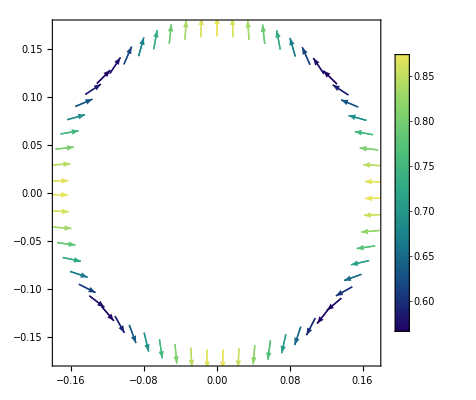

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,0.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

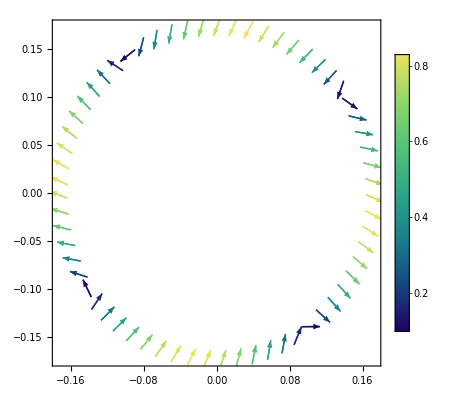

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,Pi/2.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,Pi/2.0,0.0,0.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

-Graphics-

#### Sphere plots of mechanical modes

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,5,0};
Clear[r0];
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r0,theta,phi}][[1]],FromSphericalCoordinates[{r0,theta,phi}][[2]],FromSphericalCoordinates[{r0,theta,phi}][[3]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r0,theta,phi,0.0,0.0,0.0]]],{r0,theta,phi}]},{r0,innerRadius,outerRadius,0.001},{theta,0.01,Pi,0.2},{phi,-Pi+0.01,Pi,0.3}];
```

```mathematica
ListVectorPlot3D[myModeVectors]
```

ListVectorPlot3D[{{{{{-0.00199987,-0.0000199993,0.19999},{0.0389944,0.000389957,0.00608922}},{{-0.00190464,-0.000610107,0.19999},{0.0371375,0.0118962,0.00608922}},17,{{-0.00168033,0.0010846,0.19999},{0.0327639,-0.0211481,0.00608922}},{{-0.0019258,0.000539591,0.19999},{0.0375502,-0.0105212,0.00608922}}},14,{1}},4,{{1},14,{1}}}]
 |  |  |  |

```mathematica
vectors=Table[{{x,y,z},{y,x-x^3,z}},{x,-1.5,1.5,0.2},{y,-2,2,0.2},{z,-1,1,0.1}];
vectors
ListVectorPlot3D[vectors]
```

{{{{{-1.5,-2.,-1.},{-2.,1.875,-1.}},{{-1.5,-2.,-0.9},{-2.,1.875,-0.9}},{{-1.5,-2.,-0.8},{-2.,1.875,-0.8}},{{-1.5,-2.,-0.7},{-2.,1.875,-0.7}},{{-1.5,-2.,-0.6},{-2.,1.875,-0.6}},{{-1.5,-2.,-0.5},{-2.,1.875,-0.5}},{{-1.5,-2.,-0.4},{-2.,1.875,-0.4}},{{-1.5,-2.,-0.3},{-2.,1.875,-0.3}},{{-1.5,-2.,-0.2},{-2.,1.875,-0.2}},{{-1.5,-2.,-0.1},{-2.,1.875,-0.1}},{{-1.5,-2.,0.},{-2.,1.875,0.}},{{-1.5,-2.,0.1},{-2.,1.875,0.1}},{{-1.5,-2.,0.2},{-2.,1.875,0.2}},{{-1.5,-2.,0.3},{-2.,1.875,0.3}},{{-1.5,-2.,0.4},{-2.,1.875,0.4}},{{-1.5,-2.,0.5},{-2.,1.875,0.5}},{{-1.5,-2.,0.6},{-2.,1.875,0.6}},{{-1.5,-2.,0.7},{-2.,1.875,0.7}},{{-1.5,-2.,0.8},{-2.,1.875,0.8}},{{-1.5,-2.,0.9},{-2.,1.875,0.9}},{{-1.5,-2.,1.},{-2.,1.875,1.}}},19,{{{-1.5,2.,-1.},{2.,1.875,-1.}},{{-1.5,2.,-0.9},{2.,1.875,-0.9}},18,{{-1.5,2.,1.},{2.,1.875,1.}}}},{1},12,{{1},20},{1}}
 |  |  |  |

-Graphics3D-

#### Wrap displacement map on a sphere

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1.9,1.0}}]]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,Pi/4.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1.9,1.0}}]]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1.9,1.0}}]]
```

-Graphics3D-

#### Bubble plots of mechanical modes

```mathematica
bubbleplots={};
```

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->Function[{theta},ColorData["BlueGreenYellow"][theta]],PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed",AspectRatio->1]
```

-Graphics3D-

```mathematica
mvec={2,10,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->Function[{theta,phi},ColorData["BlueGreenYellow"][Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]]/Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/4.0+0.0001,0.0,0.0,Pi/4.0,0.0][[1]]]]]],PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->0,PerformanceGoal->"Speed",AspectRatio->1]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[0.4*displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi][[1]]]]+1.0,{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,PlotLegends->Automatic,MaxRecursion->4,PerformanceGoal->"Quality",Mesh->Full,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech-oblate.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech-oblate.png

```mathematica
mvec={2,0,1};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
auxfnc[θ_,ϕ_]:=Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,0.0]]]
```

```mathematica
Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,0.1,0.2,0.0,0.0,0.0]]]
```

{-0.0103494,-0.0598033,0.0254114}

```mathematica
SphericalPlot3D[auxfnc[theta,phi][[1]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

#### Plot modes along radial direction at fixed theta and phi

```mathematica
myModesr={};
Module[{n},For[n=0,n<=3,n++,
mvec={2,n,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModer=Table[{r,Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,Pi/2,0.0,0.0,0.0,0.0][[1]]]]},{r,innerRadius,outerRadius,0.0002}];
AppendTo[myModesr,myModer]]]
```

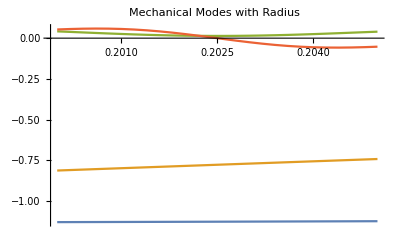

```mathematica
myplot=ListPlot[myModesr,Joined->True,PlotLabel->"Mechanical Modes with Radius",FrameLabel->{"r","displacement q"},PlotRange->All]
(*Export[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-increases/modesm2n",ToString[mvec[[2]]],"l2.png"],myplot,"PNG"]*)
```

```mathematica
myModesr
```

{{{0.2,-1.12983},{0.2002,-1.12963},{0.2004,-1.12943},{0.2006,-1.12923},{0.2008,-1.12903},{0.201,-1.12882},{0.2012,-1.12861},{0.2014,-1.1284},10,{0.2036,-1.12588},{0.2038,-1.12563},{0.204,-1.12539},{0.2042,-1.12514},{0.2044,-1.12489},{0.2046,-1.12463},{0.2048,-1.12438},{0.205,-1.12412}},99,{1}}
 |  |  |  |

#### Make more plots of mechanical modes

```mathematica
unperturbedSphere=Table[FromSphericalCoordinates[{innerRadius,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
mvec={2,0,0};
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]];
perturbationsToSphere=Table[spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ]]],{innerRadius,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
```

```mathematica
unperturbedSphere
perturbationsToSphere
```

{{{0.00199987,0.0000199993,0.19999},{0.0219546,0.000219553,0.198791},{0.0416899,0.000416913,0.195606},{0.0610087,0.000610107,0.190467},{0.0797179,0.000797205,0.183424},23,{0.0651066,0.000651088,-0.189105},{0.0459033,0.000459048,-0.19466},{0.0262413,0.000262422,-0.198271},{0.00631716,0.0000631737,-0.1999}},61,{1}}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
ListPlot3D[unperturbedSphere+perturbationsToSphere,ColorFunction->"BlueGreenYellow",InterpolationOrder->3,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{0, -2, 0}]
```

-Graphics3D-

#### Plot electric and magnetic fields over the z=constant plane

```mathematica
m0 = 0;
n0 = 1;
p0 = 2;
par=1;
A=1.0;
radius=1.0;
theta0=Pi/4.0;
alpha =0.0;
beta = 0.0;
gamma = 0.0;
epsilon=0.00001;
transverse=0;
```

```mathematica
(* get TE electric fields *)
EfieldTEr=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[1]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi*1.0+epsilon,Pi*1.0,0.1}];
EfieldTEr=ArrayFlatten[EfieldTEr,1];
p1=ListDensityPlot[EfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
EfieldTEθ=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[2]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEθ=ArrayFlatten[EfieldTEθ,1];
p2=ListDensityPlot[EfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
EfieldTEϕ=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEϕ=ArrayFlatten[EfieldTEϕ,1];
p3=ListDensityPlot[EfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
EfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Activate[electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[1]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEr=ArrayFlatten[EfieldTEr,1];
p1=ListDensityPlot[EfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
EfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[2]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEθ=ArrayFlatten[EfieldTEθ,1];
p2=ListDensityPlot[EfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
EfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEϕ=ArrayFlatten[EfieldTEϕ,1];
p3=ListDensityPlot[EfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
BfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[1]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEr=ArrayFlatten[BfieldTEr,1];
p1=ListDensityPlot[BfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
BfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[2]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEθ=ArrayFlatten[BfieldTEθ,1];
p2=ListDensityPlot[BfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
BfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEϕ=ArrayFlatten[BfieldTEϕ,1];
p3=ListDensityPlot[BfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
InputForm[FromSphericalCoordinates[{r,theta,phi}]]
```

{r*Cos[phi]*Sin[theta], r*Sin[phi]*Sin[theta], r*Cos[theta]}

#### Plot vector potential in 3d

```mathematica
r=0.8;
emdata = ParallelTable[{r*Cos[phi]*Sin[theta],r*Sin[phi]*Sin[theta],r*Cos[theta],Abs[vectorPotentialTE[1.0,1,0,1,2,1.0,Activate[wavenumberEM[0,1,2,1.0,0]],r,theta,phi][[1]]]},{theta,0.01,Pi,0.1},{phi,-Pi,Pi,0.1}]
```

{{{-0.00799987,-9.79701×10^-19,0.79996,0.130906},{-0.0079599,-0.000798654,0.79996,0.130906},{-0.0078404,-0.00158933,0.79996,0.130906},57,{-0.00768123,0.00223529,0.79996,0.130906},{-0.00786602,0.00145728,0.79996,0.130906},{-0.0079722,0.000664704,0.79996,0.130906}},30,{1}}
 |  |  |  |

```mathematica
emdata=Flatten[emdata,1]
```

{{-0.00799987,-9.79701×10^-19,0.79996,0.130906},{-0.0079599,-0.000798654,0.79996,0.130906},{-0.0078404,-0.00158933,0.79996,0.130906},2010,{-0.0242634,0.00706081,-0.799601,0.130848},{-0.0248471,0.00460323,-0.799601,0.130848},{-0.0251825,0.00209966,-0.799601,0.130848}}
 |  |  |  |

```mathematica
Dimensions[emdata]
```

{2016,4}

```mathematica
m = 2;
n = 2;
p = 2;
SphericalPlot3D[{Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.7,theta,phi][[1]]],Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.8,theta,phi][[1]]],Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.9,theta,phi][[1]]]},{theta,0.01,Pi},{phi,0,3*Pi/2},PlotTheme->"Scientific",PlotRange->All,AspectRatio->1]
```

-Graphics3D-

#### Plot EM vector field in 3d

```mathematica
points=Table[{x,y,z,Norm[spherevec2cartvec[magneticFieldTEnotrotated[1.0,1, 0,1,2,1.0,Activate[wavenumberTE[0,1,2,0.1]],#1,#2,#3]&@@ToSphericalCoordinates[{x,y,z}], ToSphericalCoordinates[{x,y,z}]]]^2},{x,-1,1,0.2},{y,-1,1,0.2},{z,-1,1,0.2}]
```

{{{{-1.,-1.,-1.,0.0000340853},{-1.,-1.,-0.8,8.78058×10^-7},{-1.,-1.,-0.6,0.0000246473},{-1.,-1.,-0.4,0.0000135351},{-1.,-1.,-0.2,0.0000117519},{-1.,-1.,0.,0.0000343576},{-1.,-1.,0.2,0.0000117519},{-1.,-1.,0.4,0.0000135351},{-1.,-1.,0.6,0.0000246473},{-1.,-1.,0.8,8.78058×10^-7},{-1.,-1.,1.,0.0000340853}},{1},7,{1},{1}},9,{1}}
 |  |  |  |

```mathematica
ListDensityPlot3D[Flatten[points,2],PlotTheme->"Scientific"]
```

-Graphics3D-

#### Check normalization of EM modes

```mathematica
mem = 0;
nem = 1;
pem = 2;
NIntegrate[Norm[electricFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
NIntegrate[Norm[magneticFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
(4/3)*Pi*innerRadius^2
```

0.0693441

0.0680184

4.18879

```mathematica
Activate[getNormalizationFactor[1,0,1,2,1.0,0]]
```

0.068499

#### Test the EM energy function by plotting for various modes

```mathematica
TEEnergies=Table[{m,n,p,calculateEMFieldEnergy[0,1.0,0,m,n,p,1.0,wavenumberTE[m,n,p,1.0]]},{m,0,2},{n,0,2},{p,1,2}]
```

{{{{0,0,1,0.},{0,0,2,0.}},{{0,1,1,0.},{0,1,2,0.}},{{0,2,1,0.},{0,2,2,0.}}},{{{1,0,1,0.},{1,0,2,0.}},{{1,1,1,0.},{1,1,2,0.0349354}},{{1,2,1,0.},{1,2,2,0.311903}}},{{{2,0,1,0.},{2,0,2,0.}},{{2,1,1,0.},{2,1,2,0.}},{{2,2,1,0.},{2,2,2,1.22983}}}}

```mathematica
TEEnergies=Table[{m,n,p,Activate[calculateEMFieldEnergy[0,1.0,0,m,n,p,1.0,wavenumberTE[m,n,p,1.0]]]},{m,0,2},{n,0,2},{p,1,2}]
```

{{{{0,0,1,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,0,1,1.,1. SphericalBesselJZero[0,1],r,θ,ϕ]]^2 getNormalizationFactor[0,0,0,1,1.,0,1. SphericalBesselJZero[0,1]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]},{0,0,2,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,0,2,1.,1. SphericalBesselJZero[0,2],r,θ,ϕ]]^2 getNormalizationFactor[0,0,0,2,1.,0,1. SphericalBesselJZero[0,2]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]}},{{0,1,1,1/2 NIntegrate[r^2 Sin[θ] 1^2 (22[1])^2,5,PrecisionGoal→2]},{1}},{{0,2,1,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,2,1,1.,1. SphericalBesselJZero[2,1],r,θ,ϕ]]^2 getNormalizationFactor[0,0,2,1,1.,0,1. SphericalBesselJZero[2,1]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]},{0,2,2,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,2,2,1.,1. SphericalBesselJZero[2,2],r,θ,ϕ]]^2 getNormalizationFactor[0,0,2,2,1.,0,1. SphericalBesselJZero[2,2]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]}}},{1},{1}}
 |  |  |  |

I think my indices may be off somewhere because there should be more modes with non-zero energies. Something is definitely off with the m,n indices

```mathematica
calculateEMFieldEnergy[0,1.0,1,0,1,3,1.0]
```

0.0174679

```mathematica
TMEnergies=Table[{m,n,p,calculateEMFieldEnergy[1,1.0,1,m,n,p,1.0]},{m,0,2},{n,0,2},{p,1,2}]
```

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,1.},{0.,3.14159},{0.,6.28319}}.

$Aborted

#### Test the overlap function

```mathematica
mmech = 2;
nmech = 1;
lmech = 0;
c0mech="C0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
c1mech=0.0;
c2mech="C2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);
d0mech="D0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
d1mech=0.0;
d2mech="D2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
Re[NIntegrate[Activate[overlapIntegrand[{mmech,nmech,lmech},{0,1,2},{0,1,3},1.0,{c0mech,d0mech,c1mech,d1mech,c2mech,d2mech},1.0,0,0,1,1,θ,ϕ]], {θ,0.001,Pi},{ϕ,0.0,2.0*Pi}, Method->"GlobalAdaptive"]]
```

0.0128473

#### Check normalization of Mechanical Modes

```mathematica
checkNormFunction[mindices_]:=Module[{mvec=mindices,coefs},
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]]);
NIntegrate[r^2*Sin[θ]*Norm[Quiet[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,θ,ϕ]]]]^2,{r,innerRadius,outerRadius},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"MultidimensionalRule",PrecisionGoal->2]/((4/3)*Pi*(outerRadius^3-innerRadius^3))]
```

```mathematica
checkNormFunction[{2,0,2}]
```

{47.2684,0.0191611,0.,0.,3.46611,-0.127022}

0.985152

```mathematica
normChecks={};
Module[{n},For[n=0,n<=128,n++,If[Mod[n,5]==0,Print[n],Clear[x]];AppendTo[normChecks,checkNormFunction[{2,n,2}]]]]
```

0

5

10

15

20

25

30

35

40

45

50

55

60

65

70

75

80

85

90

95

100

105

110

115

120

125

```mathematica
normChecks
```

{1.,1.00002,1.,1.,1.00003,1.,1.00002,1.00002,1.,1.,1.,0.961183,1.,1.00006,1.01522,0.973424,0.999971,0.999993,0.985507,0.830637,0.999987,1.01906,0.999999,1.00004,1.,1.00171,1.,1.00005,1.00264,1.00013,1.04576,0.997033,0.960642,1.00003,1.,0.984792,1.00004,0.999999,1.00027,1.,1.00259,0.999999,0.993733,1.00004,0.999852,1.00768,1.02691,1.00001,1.00001,1.01631,1.00003,1.,1.00612,1.00005,0.999998,1.00005,1.,1.00794,1.00002,1.07026,0.998015,1.,1.00005,1.,0.994278,1.00001,1.00001,1.00508,0.999998,1.00004,1.00002,0.999726,1.0065,1.,1.00624,0.999999,0.999998,1.00032,1.,1.00189,1.00003,1.,0.993414,0.999999,1.00002,0.999849,0.997039,1.00004,1.28205,0.999304,1.02677,0.99897,0.999999,1.00646,1.00005,0.999999,1.00304,1.,1.00001,1.,1.00077,1.00003,1.00002,0.979017,1.,0.953098,1.00642,1.01077,1.00004,0.96533,1.00118,1.00004,1.,0.998372,0.999999,0.999999,1.00003,1.,0.999225,1.,1.,1.,1.,0.994733,1.00004,1.00114,0.998498,1.00004,1.}

#### Check angular momentum of modes

```mathematica
angularMomentumEM[0,1,2,innerRadius,0,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],0.0,0.0,0.0]
```

{0.,7.66665×10^-21,-1.34499×10^-6}

```mathematica
"m2n0l0"/.MODES[[1]]
```

{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→2.18785,C2→0.0000728853,D0→0.140649,D2→-0.00167631}

```mathematica
angularMomentumMech[2,0,0,innerRadius,2.1878,0.14064,0.0,0.0,0.000072885,-0.0016763,0.0,0.0,0.0]
```

{0.,1.02023×10^-16,-369.572+1.71563×10^-14 ⅈ}

```mathematica
angularMomentumMech[2,0,0,innerRadius,2.1878,0.14064,0.0,0.0,0.000072885,-0.0016763,0.0,Pi,0.0]
```

{0.,-1.36546+7.41478×10^-17 ⅈ,14.3296}

#### Check that EM fields satisfy Maxwell’s Eqns.

```mathematica
Curl[electricFieldTE[A,p, m,n,p,a,k,r,θ,ϕ,0,0,0],{r,θ,ϕ},"Spherical"]+k*SPEEDOFLIGHT*magneticFieldTE[A,p, m,n,p,a,k,r,θ,ϕ,0,0,0]
```

{-(Csc[θ] (-(A 4 SphericalBesselJ[n,k √(r^2 Cos[θ]^2+r^2 1^2 1^2+r^2 Sin[θ]^2 Sin[ϕ]^2)])/(√(r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2))+7))/r+(Cos[ϕ] (-(A Cos[θ] 3 (1) SphericalBesselJ[n,k √1])/(2 1 √(r^2 Cos[θ]^2+r^2 1^2 1^2+r^2 Sin[θ]^2 Sin[ϕ]^2))+17)+Sin[ϕ] (1))/r+1. k (1),5+1. k (1-1+Cos[θ] 1 ((A 4 SphericalBesselJ[n,1])/(k (1+1))+1-1/1)),1}
 |  |  |  |

```mathematica
Simplify[%]
```

$Aborted

#### Just check on the index stuff

```mathematica
Simplify[electricField[Subscript[E, 0],1,0, m,n,p,a,k,r,θ,ϕ,0,0,0][[3]]]//TraditionalForm
```

-(ⅇ_0 nk √(r^2) ((n+1) r cos(θ) nm(r cos(θ))/(√(r^2))+√(r^2) (m-n-1) n+1m(r cos(θ))/(√(r^2))) cos(m tan^-1(r sin(θ) cos(ϕ),r sin(θ) sin(ϕ))))/(√(r^2 sin^2(θ)))

```mathematica
Simplify[D[LegendreP[n,m,Cos[θ]],θ]]//TraditionalForm
```

-csc(θ) ((n+1) cos(θ) nmcos(θ)+(m-n-1) n+1mcos(θ))

#### Check vector coordinate conversions

```mathematica
myVectorField=Table[{{x,y,z},{x,y,z}},{x,-1,1,0.1},{y,-1,1,0.1},{z,-1,1,0.1}];
ListVectorPlot3D[myVectorField]
```

-Graphics3D-

```mathematica
myVectorFieldSpherical=Table[{ToSphericalCoordinates[{x,y,z}],cartvec2spherevec[{x,y,z},ToSphericalCoordinates[{x,y,z}]]},{x,-1,1,0.1},{y,-1,1,0.1},{z,-1,1,0.1}];
```

```mathematica
myVectorFieldSpherical
```

{{{{{1.73205,2.18628,-2.35619},{1.73205,0.,-1.11022×10^-16}},{{1.67631,2.13755,-2.35619},{1.67631,2.22045×10^-16,-1.11022×10^-16}},17,{{1.67631,1.00404,-2.35619},{1.67631,1.11022×10^-16,-1.11022×10^-16}},{{1.73205,0.955317,-2.35619},{1.73205,0.,-1.11022×10^-16}}},{{{1},{1}},20},17,{1},{1}},20}
 |  |  |  |

```mathematica
myvec={1,0,0};
p={1,Pi/2,Pi/2};
cartvec2spherevec[myvec,p]
```

{0,0,-1}

Limited testing, but it seems like it works.

#### Plot inner displacement with n

```mathematica
rdisplacements={};
Module[{n},For[n=0,n<=10,n++,mvec={2,n,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]]];
```

```mathematica
rdisplacements=Delete[rdisplacements,8]
```

{0.920987,0.66523,-0.0339671,-0.0437955,{{0.+1. (0.+1. (0.+0.00418444 (2.13522+Re[0.0387283 LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]]-0.00319726 Flatten[LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]],{{1,2}}]⟦3⟧]))),0.+1. (0.+1. (0.+0.00418444 (2.27385+Re[0.0387283 LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]]-0.00319726 Flatten[LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]],{{1,2}}]⟦3⟧])))}},-0.00284991,0.00389576,0.0614708,0.00373115,-0.000524587}

#### Plot spherical vector field

```mathematica
(* write a function that plots a spherical vector field in cartesian coordinates *)
```

```mathematica
(* make a table of the spherical vectors in a spherical coordinate spacing *)
r0=0.2;
vectorsAndPoints=Table[{FromSphericalCoordinates[{r,θ,ϕ}],spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,θ,ϕ]]],{r,θ,ϕ}]},{r,innerRadius,outerRadius,0.003},{θ,0.01,Pi,0.7},{ϕ,-Pi+0.01,Pi,0.7}];
```

```mathematica
(* convert all points to cartesian and all vectors to cartesian *)
cartTable={};
Module[{i},For[i=1,i<=Length[vectorsAndPoints],i++,AppendTo[cartTable,{FromSphericalCoordinates[vectorsAndPoints[[i,1]]],spherevec2cartvec[vectorsAndPoints[[i,2]],vectorsAndPoints[[i,1]]]}]]]
```

```mathematica
cartTable
```

{{{-0.00199987,-0.0000199993,0.19999},{0.00239938,0.0000239946,-1.84177}},{{-0.00198788,-0.000219553,0.19999},{0.002385,0.000263413,-1.84177}},2012,{{-0.00622298,0.00108863,-0.1999},{0.00743372,-0.00130044,1.8399}},{{-0.00630057,0.000461934,-0.1999},{0.00752641,-0.000551808,1.8399}}}
 |  |  |  |

```mathematica
(* plot these vectors *)
ListVectorPlot3D[vectorsAndPoints]
```

ListVectorPlot3D[{{{{{-0.00199987,-0.0000199993,0.19999},{0.00239938,0.0000239946,-1.84177}},{{-0.0015167,-0.00130365,0.19999},{0.00181969,0.00156408,-1.84177}},{{-0.000320203,-0.00197417,0.19999},{0.000384171,0.00236855,-1.84177}},{{0.00102689,-0.00171621,0.19999},{-0.00123203,0.00205906,-1.84177}},{{0.00189102,-0.000651088,0.19999},{-0.00226879,0.000781157,-1.84177}},{{0.00186577,0.000720248,0.19999},{-0.0022385,-0.000864133,-1.84177}},{{0.000963025,0.00175284,0.19999},{-0.00115541,-0.00210301,-1.84177}},{{-0.000392648,0.00196104,0.19999},{0.000471088,-0.00235281,-1.84177}},{{-0.00156365,0.00124694,0.19999},{0.00187603,-0.00149604,-1.84177}}},{{{-0.13036,-0.00130365,0.151672},{-0.165067,-0.00165073,-1.02277}},{{-0.0988652,-0.0849775,0.151672},{-0.125187,-0.107602,-1.02277}},{{-0.0208723,-0.128685,0.151672},{-0.0264293,-0.162946,-1.02277}},{{0.0669372,-0.11187,0.151672},{0.0847586,-0.141654,-1.02277}},{{0.123265,-0.0424408,0.151672},{0.156083,-0.0537403,-1.02277}},{{0.121619,0.046949,0.151672},{0.153999,0.0594487,-1.02277}},{{0.0627743,0.114258,0.151672},{0.0794873,0.144678,-1.02277}},{{-0.0255946,0.12783,0.151672},{-0.0324089,0.161863,-1.02277}},{{-0.101926,0.081281,0.151672},{-0.129063,0.102921,-1.02277}}},{{{-0.19741,-0.00197417,0.0320209},{-0.879684,-0.00879714,-0.113783}},{{-0.149716,-0.128685,0.0320209},{-0.667152,-0.573437,-0.113783}},{{-0.0316078,-0.194873,0.0320209},{-0.140848,-0.86838,-0.113783}},{{0.101366,-0.16941,0.0320209},{0.451699,-0.754911,-0.113783}},{{0.186666,-0.06427,0.0320209},{0.831805,-0.286395,-0.113783}},{{0.184174,0.0710969,0.0320209},{0.8207,0.316817,-0.113783}},{{0.0950618,0.173026,0.0320209},{0.423607,0.771025,-0.113783}},{{-0.038759,0.193578,0.0320209},{-0.172715,0.862607,-0.113783}},{{-0.154351,0.123087,0.0320209},{-0.687807,0.548493,-0.113783}}},{{{-0.171615,-0.00171621,-0.102691},{-0.527624,-0.00527642,0.506783}},{{-0.130153,-0.11187,-0.102691},{-0.40015,-0.343941,0.506783}},{{-0.0274777,-0.16941,-0.102691},{-0.0844791,-0.520844,0.506783}},{{0.0881206,-0.147273,-0.102691},{0.270924,-0.452786,0.506783}},{{0.162274,-0.0558719,-0.102691},{0.498907,-0.171776,0.506783}},{{0.160108,0.0618068,-0.102691},{0.492246,0.190023,0.506783}},{{0.0826403,0.150417,-0.102691},{0.254075,0.462451,0.506783}},{{-0.0336944,0.168283,-0.102691},{-0.103592,0.517382,0.506783}},{{-0.134182,0.107004,-0.102691},{-0.412538,0.328979,0.506783}}},{{{-0.0651066,-0.000651088,-0.189105},{0.0380935,0.000380948,1.62528}},{{-0.0493768,-0.0424408,-0.189105},{0.0288901,0.0248319,1.62528}},{{-0.0104244,-0.06427,-0.189105},{0.00609924,0.037604,1.62528}},{{0.0334308,-0.0558719,-0.189105},{-0.0195602,0.0326903,1.62528}},{{0.061563,-0.0211965,-0.189105},{-0.0360202,0.0124019,1.62528}},{{0.0607411,0.023448,-0.189105},{-0.0355393,-0.0137193,1.62528}},{{0.0313517,0.0570645,-0.189105},{-0.0183437,-0.0333881,1.62528}},{{-0.0127829,0.0638427,-0.189105},{0.00747917,-0.037354,1.62528}},{{-0.0509055,0.0405947,-0.189105},{0.0297845,-0.0237517,1.62528}}}},{{{{-0.00202986,-0.0000202993,0.20299},{0.00293351,0.0000293361,-1.83649}},{{-0.00153945,-0.0013232,0.20299},{0.00222477,0.00191226,-1.83649}},{{-0.000325006,-0.00200378,0.20299},{0.000469691,0.00289581,-1.83649}},{{0.00104229,-0.00174195,0.20299},{-0.00150629,0.00251742,-1.83649}},{{0.00191938,-0.000660854,0.20299},{-0.00277385,0.00095505,-1.83649}},{{0.00189376,0.000731052,0.20299},{-0.00273681,-0.0010565,-1.83649}},{{0.000977471,0.00177913,0.20299},{-0.00141262,-0.00257116,-1.83649}},{{-0.000398538,0.00199046,0.20299},{0.000575957,-0.00287656,-1.83649}},{{-0.00158711,0.00126564,0.20299},{0.00229365,-0.00182907,-1.83649}}},{{{-0.132316,-0.0013232,0.153947},{-0.144312,-0.00144317,-1.00241}},{{-0.100348,-0.0862521,0.153947},{-0.109446,-0.0940721,-1.00241}},{{-0.0211854,-0.130615,0.153947},{-0.0231061,-0.142458,-1.00241}},{{0.0679412,-0.113548,0.153947},{0.0741011,-0.123843,-1.00241}},{{0.125114,-0.0430774,0.153947},{0.136457,-0.046983,-1.00241}},{{0.123444,0.0476532,0.153947},{0.134636,0.0519737,-1.00241}},{{0.0637159,0.115972,0.153947},{0.0694927,0.126486,-1.00241}},{{-0.0259785,0.129747,0.153947},{-0.0283338,0.141511,-1.00241}},{{-0.103455,0.0825002,0.153947},{-0.112834,0.0899801,-1.00241}}},{{{-0.200371,-0.00200378,0.0325012},{-0.875798,-0.00875827,-0.105016}},{{-0.151962,-0.130615,0.0325012},{-0.664205,-0.570903,-0.105016}},{{-0.0320819,-0.197796,0.0325012},{-0.140226,-0.864543,-0.105016}},{{0.102886,-0.171951,0.0325012},{0.449703,-0.751575,-0.105016}},{{0.189466,-0.065234,0.0325012},{0.82813,-0.28513,-0.105016}},{{0.186936,0.0721633,0.0325012},{0.817075,0.315417,-0.105016}},{{0.0964878,0.175621,0.0325012},{0.421736,0.767618,-0.105016}},{{-0.0393403,0.196482,0.0325012},{-0.171952,0.858796,-0.105016}},{{-0.156666,0.124934,0.0325012},{-0.684768,0.546069,-0.105016}}},{{{-0.174189,-0.00174195,-0.104231},{-0.513874,-0.00513891,0.484875}},{{-0.132105,-0.113548,-0.104231},{-0.389722,-0.334977,0.484875}},{{-0.0278898,-0.171951,-0.104231},{-0.0822776,-0.50727,0.484875}},{{0.0894424,-0.149482,-0.104231},{0.263863,-0.440987,0.484875}},{{0.164708,-0.05671,-0.104231},{0.485905,-0.1673,0.484875}},{{0.16251,0.0627339,-0.104231},{0.479418,0.185071,0.484875}},{{0.0838799,0.152673,-0.104231},{0.247453,0.4504,0.484875}},{{-0.0341998,0.170808,-0.104231},{-0.100893,0.503898,0.484875}},{{-0.136195,0.108609,-0.104231},{-0.401787,0.320406,0.484875}}},{{{-0.0660832,-0.000660854,-0.191942},{0.0537318,0.000537335,1.61521}},{{-0.0501175,-0.0430774,-0.191942},{0.0407502,0.0350259,1.61521}},{{-0.0105807,-0.065234,-0.191942},{0.00860312,0.0530413,1.61521}},{{0.0339323,-0.05671,-0.191942},{-0.0275901,0.0461105,1.61521}},{{0.0624865,-0.0215144,-0.191942},{-0.0508073,0.0174932,1.61521}},{{0.0616522,0.0237997,-0.191942},{-0.050129,-0.0193514,1.61521}},{{0.031822,0.0579205,-0.191942},{-0.0258742,-0.0470947,1.61521}},{{-0.0129746,0.0648004,-0.191942},{0.0105495,-0.0526887,1.61521}},{{-0.0516691,0.0412036,-0.191942},{0.0420117,-0.0335023,1.61521}}}}}]

```mathematica
vectorsAndPoints=Table[spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],#1,#2,#3]]],{#1,#2,#3}]&@@ToSphericalCoordinates[{x0,y0,z0}],{x0,-2,2},{y0,-2,2},{z0,-2,2}];
```

```mathematica
vectorsAndPoints
```

{1}
 |  |  |  |

```mathematica
ListSliceVectorPlot3D[vectorsAndPoints,ImplicitRegion[x^2+y^2+z^2==1^2,{x,y,z}],DataRange->{{-2,2},{-2,2},{-2,2}}]
```

-Graphics3D-

#### Look at em fields

```mathematica
?electricField
```

```mathematica
Simplify[Activate[electricField[fnlm,1,0,0,2,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,0,0]],Assumptions->{r>0}]//MatrixForm
Simplify[Activate[electricField[fnlm,1,0,0,2,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,a,0]],Assumptions->{r>0}]//MatrixForm
Simplify[Activate[electricField[fnlm,1,0,0,1,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,0,0]],Assumptions->{r>0}]//MatrixForm
Simplify[Activate[electricField[fnlm,1,0,0,1,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,a,0]],Assumptions->{r>0}]//MatrixForm
```

(0
0
-3 fnlm Cos[θ] Sin[θ] SphericalBesselJ[2,28.8173 r])

(0
3 fnlm Sin[a] (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) Sin[ϕ] SphericalBesselJ[2,28.8173 r]
3 fnlm (Cos[θ] Cos[ϕ] Sin[a]-Cos[a] Sin[θ]) (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) SphericalBesselJ[2,28.8173 r])

(0
0
-fnlm Sin[θ] SphericalBesselJ[1,28.8173 r])

(0
fnlm Sin[a] Sin[ϕ] SphericalBesselJ[1,28.8173 r]
fnlm (Cos[θ] Cos[ϕ] Sin[a]-Cos[a] Sin[θ]) SphericalBesselJ[1,28.8173 r])

```mathematica
FullSimplify[Norm[Simplify[Activate[electricField[1.0,1,0,0,2,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,a,0]],Assumptions->{r>0}]]]
```

√(9. Abs[(1. Cos[θ] Cos[ϕ] Sin[a]-1. Cos[a] Sin[θ]) (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) SphericalBesselJ[2,28.8173 r]]^2+9. Abs[Sin[a] (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) Sin[ϕ] SphericalBesselJ[2,28.8173 r]]^2)

```mathematica
Simplify[Cos[t]*Sin[a]*Sin[t]^2*Sin[p]/Sqrt[1-(Cos[a]*Cos[t]-Cos[p]*Sin[a]*Sin[t])^2]]
```

(Cos[t] Sin[a] Sin[p] Sin[t]^2)/(√(1-(Cos[a] Cos[t]-Cos[p] Sin[a] Sin[t])^2))

```mathematica
Activate[wavenumberEM[0,2,2,1.0,0]]
wavenumberEM[0,1,2,1.0,0]
```

5.76346

1. SphericalBesselJZero[1,2]

```mathematica
5.7634592/0.2
```

28.8173

Calculate Some Realistic Form Factors

```mathematica
overlapfunction[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],{0,0,0,0,0,0}]//AbsoluteTiming
overlapfunctionParallel[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],{0,0,0,0,0,0}]//AbsoluteTiming
```

{0.000095,overlapfunction[{2,0,0,0,1,2,0,1,2},0.2,0,0,1,1,38.6263,38.6263,38.6263,38.6263,{0,0,0,0,0,0}]}

{0.000051,overlapfunctionParallel[{2,0,0,0,1,2,0,1,2},0.2,0,0,1,1,38.6263,38.6263,38.6263,38.6263,{0,0,0,0,0,0}]}

```mathematica
"m2n1l0"/.MODES[[1]]
```

{wavenumberk→5.2182,wavenumberp→2.28346,frequency→4810.18,C0→2.74226,C2→0.913666,D0→-0.454449,D2→0.699394}

```mathematica
overlap1Sphere2Modes[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,{0,0,0,0,0,0}]//AbsoluteTiming
```

{6.35319,-1.16623}

Radiation Pressure at the Surface

```mathematica
poyntingVector[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=Cross[electricField[amplitude,parity,TMorTE, m,n,p,a,k,a,θ,ϕ,0.0,0.0,0.0],magneticField[amplitude,parity,TMorTE, m,n,p,a,k,a,θ,ϕ,0.0,0.0,0.0]]
cosOfAngleOfIncidence4Radiation[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ].{1,0,0}/Norm[poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]]
radiationPressure[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=Norm[poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]]*cosOfAngleOfIncidence4Radiation[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]^2/2
```

```mathematica
NIntegrate[radiationPressure[1.0,1,1,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],θ,ϕ]*innerRadius^2*Sin[θ],{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

2.53999×10^-9

# Double Spherical Shell Mechanical-EM Coupling

Calculate shifted frequencies for doubled up modes coupled at antipodal points

F is equivalent to vectorPotentialTE, so we just need to figure out where to cavities are being coupled. They don’t necessarily need to be coupled at a point where the fields are identical. In fact, we probably don’t want them to be identical in general. We’ll try antipodal points for now. Cavity 1 will be connected to cavity 2 at (r1=a, θ1=pi/2, ϕ1=0), (r2=a, θ1=pi/2, ϕ1=pi). The hole will be of size d << a, and the volume of each cavity will be (4/3) Pi a^3. Now use eqs. (78, 78a) from the Bethe paper.

#### Define the vector potentials

```mathematica
couplingPoints={{innerRadius,Pi/2.0,Pi},{innerRadius,Pi/2.0,0.0}};
```

```mathematica
Fpotential[amplitude_,parity_,tmorte_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=(1/(omegaEM[m,n,p,a,tmorte]))*magneticField[amplitude,parity,tmorte, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]
garbageVariableUsedToDefineFunctions=(1/(k))*electricField[amplitude,parity,tmorte,m0,n0,p0,a,k,r,θ,ϕ,ang1,ang2,ang3];
Apotential[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

#### Calculate the splitting functions

```mathematica
garbageVariableUsedToDefineFunctions=2*Norm[Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]]&@@couplingPoints[[1]]]^2-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]][[1]]&@@couplingPoints[[1]])^2;
cαα[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=2*Norm[Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]]&@@couplingPoints[[2]]]^2-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]][[1]]&@@couplingPoints[[2]])^2;
cββ[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=2*(Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]]&@@couplingPoints[[1]]).(Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]]&@@couplingPoints[[2]])-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]][[1]]&@@couplingPoints[[2]])*(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[6]],offsets[[7]],offsets[[8]]][[1]]&@@couplingPoints[[1]]);
cαβ[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
(* solve for the frequency shift from quadratic *)
garbageVariableUsedToDefineFunctions=(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]))/2 + (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]) + (16/9)*(d^6/V^2)*(cαα[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]*cββ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]-cαβ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]^2)))^(1/2));
frequencyCoefPlus[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,d_,V_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))/2 - (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]) + (16/9)*(d^6/V^2)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]*cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]-cαβ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]^2)))^(1/2));
frequencyCoefMinus[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,d_,V_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
getShiftedFrequencies[amplitude_,parity_,tmorte_,m_,n_,p_,a_,d_,offsets_]:=Activate[omegaEM[m,n,p,a,tmorte]*{frequencyCoefPlus[amplitude,parity,tmorte, m,n,p,a,wavenumberEM[m,n,p,a,tmorte],d,(4.0/3.0)*Pi*a^3,offsets],frequencyCoefMinus[amplitude,parity,tmorte, m,n,p,a,wavenumberEM[m,n,p,a,tmorte],d,(4.0/3.0)*Pi*a^3,offsets] }]
```

```mathematica
Activate[getShiftedFrequencies[1.0,0,1,0,1,2,0.2,0.01,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0}]]
```

{13.7185,13.7185}

Calculate overlap for 2 coupled spheres

```mathematica
overlapCoupledSpheresArtificialSplitting[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1.0]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1.0]

overlapCoupledSpheresArtificialSplittingGlobalAdaptive[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunctionGlobalAdaptive[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunctionGlobalAdaptive[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1]

overlapCoupledSpheresArtificialSplittingTrap[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunctionTrap[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunctionTrap[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1]

overlapCoupledSpheres[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_]:=(overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1])&@@getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets]

overlapCoupledSpheresPrintSplitting[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_]:={(overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1])&@@getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets],getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets]}
```

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,0.0,0.,0.,0.0,0.},0.0033]//AbsoluteTiming
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,0.0,0.,0.,Pi,0.},0.0033]//AbsoluteTiming
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,-Pi/4.0,0.,0.,Pi/4.0,0.},0.0033]//AbsoluteTiming
```

$Aborted

$Aborted

$Aborted

Results imported from cluster

#### Right stuff (still wrong splitting)

```mathematica
angularOverlaps1 = Flatten[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius1-thickness1percent/overlaps/overlaps-mech-EM-fixedEM-vary-mech-z-and-xy.txt","CSV"],1];
For[i=1,i<=Length[angularOverlaps1],i++,angularOverlaps1[[i]]=ToExpression[angularOverlaps1[[i]]]]
```

```mathematica
Min[Abs[angularOverlaps1[[All,3]]]]
```

0.0063216

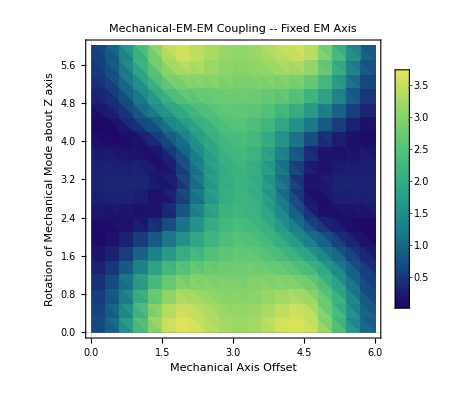

```mathematica
optpoints1={{0.0,Pi/4.0},{2.0*Pi,Pi/4.0}};
optpoints2={{0.0,2.0*Pi-3.0*Pi/4.0},{2.0*Pi,2.0*Pi-3.0*Pi/4.0}};
p1=ListDensityPlot[Abs[angularOverlaps1],PlotTheme->"Scientific", FrameLabel->{Style["Mechanical Axis Offset",16], Style["Rotation of Mechanical Mode about Z axis",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- Fixed EM Axis",16], InterpolationOrder->2,ColorFunction->"BlueGreenYellow"]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/mech-em-em-coupling-fixedEMpolarization-vary-mechanical-axis-and-polarization.png",p1,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/mech-em-em-coupling-fixedEMpolarization-vary-mechanical-axis-and-polarization.png

#### Right function wrong frequency splitting

```mathematica
angularOverlaps={{{0.,0.,-27.960472716120947},{0.,0.3,-26.02050686091922},{0.,0.6,-21.534733635114186},{0.,0.8999999999999999,-14.952312413546192},{0.,1.2,-9.136220558553049},{0.,1.5,-7.208730837230907},{0.,1.7999999999999998,-8.021922862560894},{0.,2.1,-12.449953954467661},{0.,2.4,-18.808768321752993},{0.,2.6999999999999997,-24.495580279260366},{0.,3.,-27.580175340132058}},{{0.3,0.,-25.997862046384228},{0.3,0.3,-25.11048789676591},{0.3,0.6,-19.604525305344264},{0.3,0.8999999999999999,-12.979414711567532},{0.3,1.2,-7.931217582744931},{0.3,1.5,-5.330735143608484},{0.3,1.7999999999999998,-6.296667981864672},{0.3,2.1,-10.35002697187591},{0.3,2.4,-16.945229414184425},{0.3,2.6999999999999997,-22.60241137587495},{0.3,3.,-25.941828445259667}},{{0.6,0.,-21.408276084801418},{0.6,0.3,-19.61770438168749},{0.6,0.6,-14.555508119914343},{0.6,0.8999999999999999,-8.196986797278091},{0.6,1.2,-2.6346976158526534},{0.6,1.5,-0.15995073532404813},{0.6,1.7999999999999998,-1.3833159801454453},{0.6,2.1,-5.691660799797039},{0.6,2.4,-11.741039513191009},{0.6,2.6999999999999997,-17.68137628895758},{0.6,3.,-21.05299220901437}},{{0.8999999999999999,0.,-14.770176587046368},{0.8999999999999999,0.3,-13.148261732497675},{0.8999999999999999,0.6,-8.044634106677002},{0.8999999999999999,0.8999999999999999,-2.136130170116152},{0.8999999999999999,1.2,3.067867268351742},{0.8999999999999999,1.5,5.80532413945167},{0.8999999999999999,1.7999999999999998,4.925754572127225},{0.8999999999999999,2.1,0.6166753006685364},{0.8999999999999999,2.4,-5.64458919989189},{0.8999999999999999,2.6999999999999997,-10.924967961918556},{0.8999999999999999,3.,-14.865186118252097}},{{1.2,0.,-9.552772267503729},{1.2,0.3,-7.6871669775692375},{1.2,0.6,-2.7978841652941577},{1.2,0.8999999999999999,3.063551880620132},{1.2,1.2,8.773402039251403},{1.2,1.5,11.397429472928756},{1.2,1.7999999999999998,10.216098176450199},{1.2,2.1,5.871824136388648},{1.2,2.4,-0.39516457865417465},{1.2,2.6999999999999997,-5.513886897621195},{1.2,3.,-9.759223829862137}},{{1.5,0.,-7.402131546629543},{1.5,0.3,-4.882784063385195},{1.5,0.6,-0.08850748306732736},{1.5,0.8999999999999999,5.807385645146162},{1.5,1.2,11.230778476706472},{1.5,1.5,13.6521628818726},{1.5,1.7999999999999998,12.871475126610846},{1.5,2.1,8.707072531837472},{1.5,2.4,2.2698291347339303},{1.5,2.6999999999999997,-3.739497374970002},{1.5,3.,-7.073121831932078}},{{1.7999999999999998,0.,-8.465608667868803},{1.7999999999999998,0.3,-6.145959916286062},{1.7999999999999998,0.6,-2.186838071032396},{1.7999999999999998,0.8999999999999999,4.701334105593752},{1.7999999999999998,1.2,10.123306608332172},{1.7999999999999998,1.5,12.901875684593447},{1.7999999999999998,1.7999999999999998,11.791840897316506},{1.7999999999999998,2.1,7.6377967906383954},{1.7999999999999998,2.4,1.7771016873410925},{1.7999999999999998,2.6999999999999997,-3.9706419696849027},{1.7999999999999998,3.,-7.5990208103917585}},{{2.1,0.,-12.254625652089134},{2.1,0.3,-10.408155092711578},{2.1,0.6,-5.7077984450187715},{2.1,0.8999999999999999,0.483457993117665},{2.1,1.2,5.804026845282698},{2.1,1.5,8.35749495844653},{2.1,1.7999999999999998,7.750138754698066},{2.1,2.1,3.2883741412379477},{2.1,2.4,-2.4996661315718187},{2.1,2.6999999999999997,-8.706838549349929},{2.1,3.,-11.967976905776723}},{{2.4,0.,-19.06677154381652},{2.4,0.3,-16.43628390872536},{2.4,0.6,-12.109522639607121},{2.4,0.8999999999999999,-5.2736325928005146},{2.4,1.2,0.19838771761205987},{2.4,1.5,2.284115247769166},{2.4,1.7999999999999998,1.2409333111038077},{2.4,2.1,-3.1616557699699896},{2.4,2.4,-9.204435270882378},{2.4,2.6999999999999997,-14.186475240536693},{2.4,3.,-17.76201790790985}},{{2.6999999999999997,0.,-24.2574626703086},{2.6999999999999997,0.3,-21.7624708996408},{2.6999999999999997,0.6,-18.125820904824508},{2.6999999999999997,0.8999999999999999,-11.624436831170733},{2.6999999999999997,1.2,-5.480618034790852},{2.6999999999999997,1.5,-3.377264693295224},{2.6999999999999997,1.7999999999999998,-4.089476981925204},{2.6999999999999997,2.1,-8.626953903162308},{2.6999999999999997,2.4,-14.364008686105727},{2.6999999999999997,2.6999999999999997,-20.44877288401445},{2.6999999999999997,3.,-23.8546601375406}},{{3.,0.,-28.130006204082278},{3.,0.3,-26.155589934278385},{3.,0.6,-20.548225943722713},{3.,0.8999999999999999,-14.820025447291219},{3.,1.2,-9.464310007372479},{3.,1.5,-6.2806989603313435},{3.,1.7999999999999998,-7.847338683889712},{3.,2.1,-12.222366445676304},{3.,2.4,-17.645816572534},{3.,2.6999999999999997,-24.240264890747483},{3.,3.,-26.910491631367023}}};
```

```mathematica
angularOverlaps=Flatten[angularOverlaps,1];
```

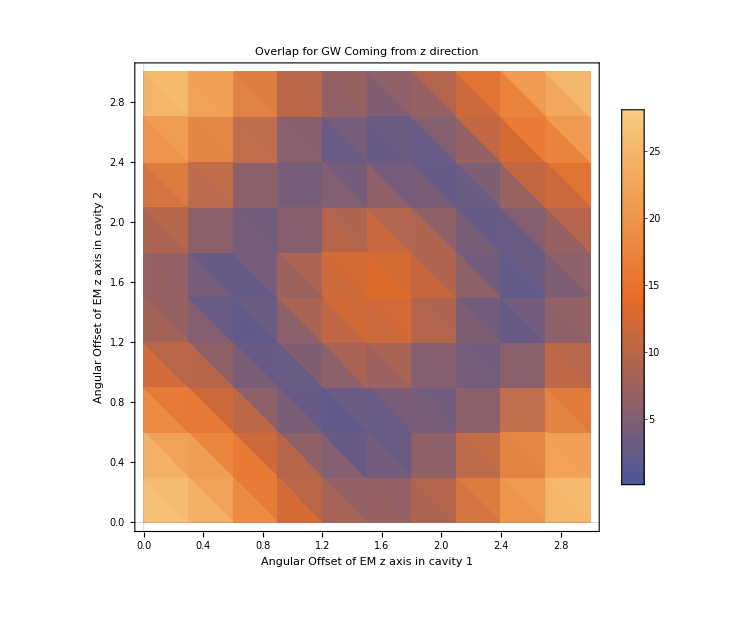

```mathematica
myplot=ListDensityPlot[Abs[angularOverlaps],PlotTheme->"Scientific",PlotLabel->"Overlap for GW Coming from z direction",FrameLabel->{"Angular Offset of EM z axis in cavity 1","Angular Offset of EM z axis in cavity 2"}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-with-EM-polarization.png",myplot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-with-EM-polarization.png

# Double Spherical Shell GW-Mechanical Coupling

We basically just need to compute the integral given in eq. (114) of Sebastian’s notes. The coupling should just be eq. (19) from my notes where the strain and the time dependence comes from the actual form of the + polarized GW.

#### Coordinate transformation of TT metric perturbation

```mathematica
cartinsphere={r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]*Sin[θ],r*Cos[θ]};
spherecoords={r,θ,ϕ};
jacobian=Table[D[cartinsphere[[i]],spherecoords[[j]]],{i,1,3},{j,1,3}];
ttMetric={{1,0,0},{0,-1,0},{0,0,0}};
ttMetricSpherical=Module[{a,b,i,j},Table[Simplify[Sum[ttMetric[[a,b]]*jacobian[[a,i]]*jacobian[[b,j]],{a,1,3},{b,1,3}]],{i,1,3},{j,1,3}]];
```

```mathematica
ttMetricSpherical//MatrixForm
```

(Cos[2 ϕ] Sin[θ]^2 | 1/2 r Cos[2 ϕ] Sin[2 θ] | -2 r Cos[ϕ] Sin[θ]^2 Sin[ϕ]
1/2 r Cos[2 ϕ] Sin[2 θ] | r^2 Cos[θ]^2 Cos[2 ϕ] | -2 r^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]
-2 r Cos[ϕ] Sin[θ]^2 Sin[ϕ] | -2 r^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] | -r^2 Cos[2 ϕ] Sin[θ]^2)

#### GW-Mechanical coupling function

```mathematica
garbageVariableUsedToDefineFunctions=r^3 * Sin[θ] *(Cos[ϕ]*Sin[θ]*(displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ].{Sin[θ]*Cos[ϕ],Cos[θ]*Cos[ϕ],-Sin[ϕ]})-Sin[ϕ]*Sin[θ]*(displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ].{Sin[θ]*Sin[ϕ],Cos[θ]*Sin[ϕ],Cos[ϕ]}));
gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,pol1_,pol2_,pol3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[m_,n_,l_,a_,b_,pol1_,pol2_,pol3_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol1,pol2,pol3]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"LevinRule",PrecisionGoal->4]/(2*((4/3)*Pi*(outerRadius^3 - innerRadius^3))^(4/3))
gwMechCouplingFixedGWVarMechCart2SphereMC[m_,n_,l_,a_,b_,pol1_,pol2_,pol3_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol1,pol2,pol3]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->10^5]/(2*((4/3)*Pi*(outerRadius^3 - innerRadius^3))^(4/3))
gwMechCouplingFixedGWVarMechCart2SphereTwoSpheres[m_,n_,l_,a_,b_,pol_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->2]/(2*(4/3)*Pi*(outerRadius^3 - innerRadius^3))
```

#### Test integrand and integral

```mathematica
Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[2,0,0,innerRadius,"C0","D0",0.0,0.0,"C2","D2",1.004,0.1,0.2,Pi/4]/.Quiet[(StringJoin["m",ToString[2],"n",ToString[0],"l",ToString[0]]/.MODES[[1]])]//N]]
```

Re[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[2.,0.,0.,0.2,47.1908,0.0191296,0.,0.,3.46041,-0.126813,1.004,0.1,0.2,0.785398]]

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,3,2,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
(*gwMechCouplingFixedGWVarMechCart2SphereTwoSpheres[2,0,1,innerRadius,outerRadius,0]//AbsoluteTiming*)
```

{364.775,-0.0000116789}

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,2,2,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

{7.14093,0.00467069}

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,2,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

{1.06605,-0.409548}

```mathematica
gwMechCouplingFixedGWVarMechCart2SphereMC[2,0,1,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

{31.4071,-0.000163652}

```mathematica
{-0.4086634150814706,0.11970550719268995,0.004670689728271012,-0.0000116788735650819}
```

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,0,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

{647.775,-1.56262×10^-17}

# Figures

### Optimal polarization of EM axes

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.0,0.1,0.0,0.0,0.0,0.0,0.0,0.5,0.0},0.0033]//AbsoluteTiming
```

{30.8791,0.236084}

```mathematica
OverlapsWithVariablePolarizationTableFlattened=Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/test-best-polarization.csv","CSV"]
```

{{0.01,-3.13159,-0.00540214},{0.01,-3.03159,0.0341494},{0.01,-2.93159,0.0686809},{0.01,-2.83159,0.138429},{0.01,-2.73159,0.27491},{0.01,-2.63159,0.434182},2004,{3.11,2.56841,0.473892},{3.11,2.66841,0.294653},{3.11,2.76841,0.18836},{3.11,2.86841,0.10508},{3.11,2.96841,0.0237494},{3.11,3.06841,-0.00514592}}
 |  |  |  |

```mathematica
OverlapsWithVariablePolarizationTableFlattenedAbs=OverlapsWithVariablePolarizationTableFlattened;
OverlapsWithVariablePolarizationTableFlattenedAbs[[All,3]]=Abs[OverlapsWithVariablePolarizationTableFlattenedAbs[[All,3]]];
```

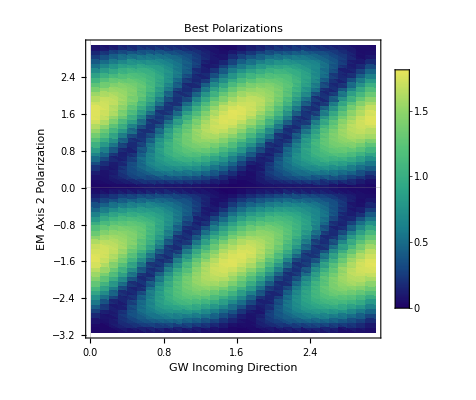

```mathematica
ListDensityPlot[OverlapsWithVariablePolarizationTableFlattenedAbs,PlotTheme->"Scientific",FrameLabel->{Style["GW Incoming Direction",20],Style["EM Axis 2 Polarization",20]}, PlotLabel->Style[StringJoin["Best Polarizations"],20],ColorFunction->"BlueGreenYellow",AspectRatio->1,ImageSize->{400,400},ColorFunctionScaling->True,PlotLegends->Automatic]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarizations.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarizations.png

### Overlaps: (η^200)_(012,012) Fixed EM Polarization Variable GW Directionality Plus Polarization

Plot of the mechanical-EM-EM overlap factor for mechanical mode 200 and EM modes 012+ and 012-. Double cavity setup with a fixed splitting on 1 MHz. EM polarizations set to -Pi/4 and 5 Pi/4 for the left and right cavities respectively. Coupling axis is along x. Directionality of the GW is determined by RollPitchYawMatrix[{α, β, 0}]. The plot is made by converting the z’’ axis (given by RollPitchYawMatrix[{α, β, 0}].{0, 0, 1} into spherical coordinates and then plotting an Aitoff projection. In this sense, the GW polarization is fixed. Since the third euler angle is zero, this GW is plus polarized.

```mathematica
filename="eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.txt";
(* import data *)
overlaps=Flatten[Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius1-thickness1percent/overlaps/",filename],"CSV"],1];
(* name data floats *)
For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]]
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{#1,#2,overlaps[[i,3]]}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]/((32*Pi/3)^(1/3))}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
p1=ListDensityPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["Euler Angle α",16], Style["Euler Angle β",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic]
p2=ListDensityPlot[overlapsSpherical,PlotTheme->"Scientific", FrameLabel->{Style["Inclination θ",16], Style["Azimuth ϕ",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic]
p3=ListDensityPlot[overlapsAitoff,PlotTheme->"Scientific", FrameLabel->{Style["Aitoff x (θ, ϕ)",20], Style["Aitoff y (θ, ϕ)",20]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012 -- MHz Splitting",24], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500}]
(*Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.png",p3,"PNG"]*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Activate[getNormalizationFactor[1,0,1,2,1.0,0,wavenumberEM[0,1,2,1.0,0]]]
Activate[getNormalizationFactor[1,0,1,2,1.0,0,wavenumberEM[0,1,2,1.0,0]+0.0033]]
```

7.768

7.80461

### Overlaps: (η^200)_(012,012) Fixed EM Polarization Variable GW Directionality Cross Polarization

Plot of the mechanical-EM-EM overlap factor for mechanical mode 200 and EM modes 012+ and 012-. Double cavity setup with a fixed splitting on 1 MHz. EM polarizations set to -Pi/4 and 5 Pi/4 for the left and right cavities respectively. Coupling axis is along x. Directionality of the GW is determined by RollPitchYawMatrix[{π/4, β, α}]. The plot is made by converting the z’’ axis (given by RollPitchYawMatrix[{π/4, β, α}].{0, 0, 1} into spherical coordinates and then plotting an Aitoff projection. In this sense, the GW polarization is fixed. Since the third euler angle is pi/4, this GW is cross polarized.

```mathematica
filename="eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res-GWCross.txt";
(* import data *)
overlaps=Flatten[Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius1-thickness1percent/overlaps/",filename],"CSV"],1];
(* name data floats *)
For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]]
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{#1,#2,overlaps[[i,3]]}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
p1=ListDensityPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["Euler Angle α",16], Style["Euler Angle β",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic];
p2=ListDensityPlot[overlapsSpherical,PlotTheme->"Scientific", FrameLabel->{Style["Inclination θ",16], Style["Azimuth ϕ",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic];
p3=ListDensityPlot[overlapsAitoff,PlotTheme->"Scientific", FrameLabel->{Style["Aitoff x (θ, ϕ)",20], Style["Aitoff y (θ, ϕ)",20]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012 -- MHz Splitting",24], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500}]
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res-GWCross.png",p3,"PNG"]
```

-Graphics-

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res-GWCross.png

### nothing

```mathematica
overlapIntegrand[mVec_,iVec_,jVec_,a_,modeCoefs_,EMamplitude_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,θ_,ϕ_,offsets_]:=(a^2*Sin[θ]*(displacementVecQ[mVec[[1]],mVec[[2]],mVec[[3]],a,modeCoefs[[1]],modeCoefs[[2]],modeCoefs[[3]],modeCoefs[[4]],modeCoefs[[5]],modeCoefs[[6]],a,θ,ϕ,offsets[[1]],offsets[[2]],offsets[[3]]].{1,0,0})*((wi/wj)*magneticField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]],jVec[[2]],jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].magneticField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]],iVec[[2]],iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]-electricField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]],jVec[[2]],jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].electricField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]],iVec[[2]],iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]))
```

```mathematica
displacementVecQ[2,0,0,0.1,Quiet["C0"/.("m2n0l0"/.MODES[[1]])],Quiet["D0"/.("m2n0l0"/.MODES[[1]])],0.0,0.0,Quiet["C2"/.("m2n0l0"/.MODES[[1]])],Quiet["D2"/.("m2n0l0"/.MODES[[1]])],0.1,0.1,0.2,0.0,0.0,0.0].{1,0,0}
```

```mathematica
"m2n0l0"/.MODES[[1]]
```

{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→2.18785,C2→0.0000728853,D0→0.140649,D2→-0.00167631}

### Make Plots Function

Plot of the mechanical-EM-EM overlap factor for mechanical mode 100 and EM modes 012+ and 012-. Double cavity setup with a fixed splitting on 1 MHz. EM polarizations set to -Pi/4 and 5 Pi/4 for the left and right cavities respectively. Coupling axis is along x. Directionality of the GW is determined by RollPitchYawMatrix[{α, β, 0}]. The plot is made by converting the z’’ axis (given by RollPitchYawMatrix[{α, β, 0}].{0, 0, 1} into spherical coordinates and then plotting an Aitoff projection. In this sense, the GW polarization is fixed. Since the third euler angle is zero, this GW is plus polarized.

```mathematica
makeplot[mode_,ncs_]:=Module[{mymode,overlaps,filename,overlapsSpherical,overlapsAitoff},mymode=mode;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
(* import data *)
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
(* name data floats *)
(*For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]];*)
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]](*/((32*8*Pi/3)^(1/3))*)}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
{p1=ListContourPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["Euler Angle α",16], Style["Euler Angle β",16]},PlotLabel->Style[StringJoin["Mechanical-EM-EM Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs],
p2=ListContourPlot[overlapsSpherical,PlotTheme->"Scientific", FrameLabel->{Style["Inclination θ",16], Style["Azimuth ϕ",16]},PlotLabel->Style[StringJoin["Mechanical-EM-EM Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs],
p3=ListContourPlot[overlapsAitoff,PlotTheme->"Scientific", FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},PlotLabel->Style[StringJoin["Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{300,200},ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs]}]
(*Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.png",p3,"PNG"]*)
```

```mathematica
myplots=makeplot[210,7];
GraphicsRow[{myplots[[2]],myplots[[3]]},ImageSize->Full]
```

-Graphics-

### Grid of mech. mode results cavity radius 1.0 thickness 0.01

```mathematica
plots={};
modelist={410};
For[k=1,k<=1,k++,AppendTo[plots,makeplot[modelist[[k]],7][[3]]]]
```

```mathematica
GraphicsGrid[{plots[[1;;2]],plots[[3;;4]]},ImageSize->{800,950}]
```

-Graphics-

```mathematica
plots[[1]]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-correct-sign-m=4.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-correct-sign-m=4.png

### Grid of mech. mode results cavity radius 0.2 thickness 0.005

```mathematica
plots={};
modelist={200,201,202,210,211,212,220,221,222};
For[k=1,k<=9,k++,AppendTo[plots,makeplot[modelist[[k]],7][[3]]]]
```

```mathematica
GraphicsGrid[{plots[[1;;3]],plots[[4;;6]],plots[[7;;9]]},ImageSize->{1200,825}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-radius-0.2-m2.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-radius-0.2-m2.png

```mathematica
plots={};
modelist={200,210,220,230,250,260,280,290,2100};
For[k=1,k<=9,k++,AppendTo[plots,makeplot[modelist[[k]],4][[3]]]]
GraphicsGrid[{plots[[1;;3]],plots[[4;;6]],plots[[7;;9]]},ImageSize->{1200,1100*3/4}]
```

-Graphics-

### Super high resolution radius 0.2 thickness 0.005

```mathematica
overlaps={};
kks={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20};
For[kk=1,kk<=20,kk++,
filename=StringJoin["eta-202-012-012-EMPol-minpi4-pi4-highest-res-",ToString[kks[[kk]]],".csv"];
(* import data *)
overlaps=Join[overlaps,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"]]]
```

```mathematica
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]]*0.49/((32*8*Pi/3)^(1/3))}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoffLog={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoffLog,{#1,#2,Log[Abs[overlapsSpherical[[i,3]]]]}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
```

```mathematica
(* make an interpolation function to plot that interpolates the log of overlapsAitoff *)
overlapsIF[t_,p_]:=Interpolation[overlapsAitoffLog,InterpolationOrder->8,Method->"BSplineBasis"][t,p]
```

```mathematica
Exp[overlapsIF[#1,#2]]&@@aitoff[0.1,0.2]
```

0.018083

```mathematica
myvals=Flatten[Table[{#1,#2,Exp[overlapsIF[#1,#2]]}&@@N[aitoff[t,p]],{t,0,Pi,0.05},{p,-Pi,Pi,0.05}],1]
```

{{-1.92367×10^-16,-1.5708,0.0179936},{-1.92307×10^-16,-1.5708,0.0179936},{-1.92127×10^-16,-1.5708,0.0179936},{-1.91826×10^-16,-1.5708,0.0179936},7930,{0.129768,1.56565,0.00276099},{0.130111,1.56668,0.0028343},{0.130373,1.56771,0.00285683},{0.130554,1.56875,0.00287055}}
 |  |  |  |

```mathematica
contplot=ListContourPlot[myvals,PlotTheme->"Scientific", (*FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},*)PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20], Method->"BSplineBasis",ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->10,ImageSize->{800,500},Axes->False,Frame->False,PerformanceGoal->"Quality",InterpolationOrder->1]
```

-Graphics-

```mathematica
Needs["FixPolygons`"]
```

```mathematica
?FixPolygons
```

```mathematica
contplot2=FixPolygons[contplot]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-contour-log-interpolation.pdf",contplot2,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-contour-log-interpolation.pdf

```mathematica
ListDensityPlot[myvals,PlotTheme->"Scientific", (*FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},*)PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20], InterpolationOrder->1,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500},ColorFunctionScaling->True,PlotLegends->Automatic,Axes->False,Frame->False]
```

-Graphics-

```mathematica
densplot=FixPolygons[%]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-density-log-interpolation.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-density-log-interpolation.png

```mathematica
ListContourPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20], InterpolationOrder->1,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500},ColorFunctionScaling->True,PlotLegends->Automatic]
```

-Graphics-

```mathematica
f=Interpolation[overlapsSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.1}}],Axes->False,Boxed->False]
```

-Graphics3D-

### Wrap density map on sphere

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,1,innerRadius,outerRadius,0.0,0.0,0.0]
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,2,innerRadius,outerRadius,0.0,0.0,0.0]
```

$Aborted

-0.409548

```mathematica
mymode=200;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{{overlaps[[i,1]],overlaps[[i,2]]},Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]];
f=Interpolation[overlapsSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.3}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
overlapsSpherical
```

{{{0.01,-3.13159},0.00240371},{{0.01,-2.93159},0.00297726},{{0.01,-2.73159},0.00179089},{{0.01,-2.53159},0.00153386},{{0.01,-2.33159},0.00163621},{{0.01,-2.13159},0.00119849},500,{{3.01,2.06841},0.0143029},{{3.01,2.26841},0.0190813},{{3.01,2.46841},0.0228902},{{3.01,2.66841},0.0270259},{{3.01,2.86841},0.0307698}}
 |  |  |  |

### Modes 2n0

```mathematica
myns={0,1,2,3,5,6,8,9,10};
modesWithFrequency=ParallelTable[{myns[[n]],Activate[overlapCoupledSpheresArtificialSplittingGlobalAdaptive[{2,myns[[n]],2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]},{n,1,9}]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000546957 and 8.45524×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000548923 and 7.61767×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000549906 and 5.98965×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000542681 and 8.30757×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000539165 and 6.87701×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000539489 and 5.69526×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000549465 and 6.24499×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.0005528 and 7.67041×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000561204 and 5.78355×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000543449 and 5.77631×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000549825 and 8.43642×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.00055737 and 5.77608×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000551527 and 5.73583×10^-6 for the integral and error estimates.

{{0,0.633848},{1,0.459441},{2,-0.0235341},{3,-0.0301623},{5,-0.00197998},{6,0.00273171},{8,0.0428451},{9,0.00252186},{10,-0.000360121}}

```mathematica
Activate[overlapCoupledSpheresArtificialSplittingGlobalAdaptive[{2,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]//AbsoluteTiming
```

{9.05023,0.631134}

```mathematica
{"C0","D0",0.0,0.0,"C2","D2"}/."m2n124l2"/.MODES[[1]]
```

{1.01527,0.00115816,0.,0.,0.000118122,-0.000332562}

```mathematica
(* just plot radial displacement *)
rdisplacements={};
ns={0,1,2,3,5,6,8,9,10};
Module[{i},For[i=1,i<=9,i++,mvec={2,ns[[i]],2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]}]]];
```

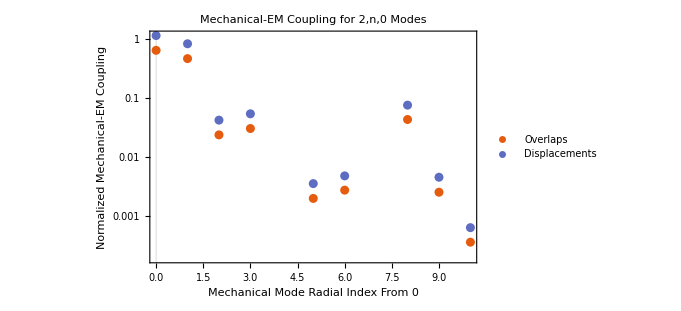

```mathematica
bothplot=ListLogPlot[{Abs[modesWithFrequency],Abs[rdisplacements]},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Radial Index From 0","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for 2,n,0 Modes",PlotLegends->{"Overlaps","Displacements"}]
```

### Plot displacements out to n=128

```mathematica
rdisplacements={};
(* make list of ns *)
ns={};
Module[{n},For[n=0,n<=128,n++,If[Head[StringJoin["m2n",ToString[n],"l2"]/.MODES[[1]]]==Head[{1,2,3}],AppendTo[ns,n],Clear[garbageVariableUsedToDefineFunctions],Clear[garbageVariableUsedToDefineFunctions]]]]
```

```mathematica
Length[ns]
```

129

```mathematica
Module[{i},For[i=1,i<=Length[ns],i++,mvec={2,ns[[i]],2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Re[Evaluate[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]}]]];
```

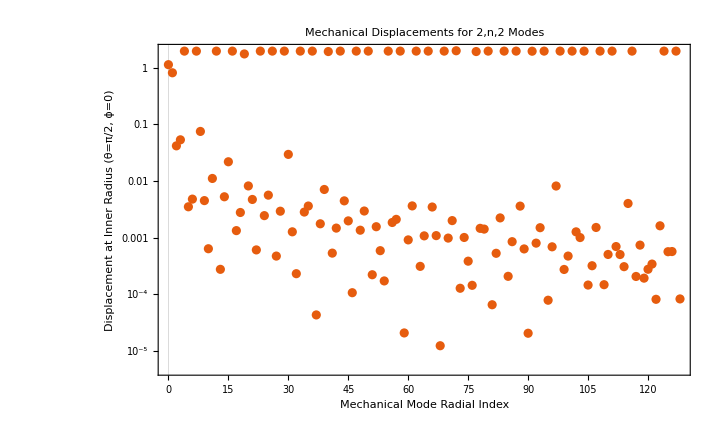

```mathematica
displot=ListLogPlot[Abs[rdisplacements],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{Style["Mechanical Mode Radial Index",18],Style["Displacement at Inner Radius (θ=π/2, ϕ=0)",18]},PlotLabel->Style["Mechanical Displacements for 2,n,2 Modes",18]]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-displacements.png",displot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-displacements.png

Find out which points are over 1 and see if there’s a pattern

```mathematica
nsGreaterThan1={};
Module[{n},For[n=0,n<=128,n++,If[Abs[rdisplacements[[n]][[2]]]>1.0,AppendTo[nsGreaterThan1,n]]]]
```

```mathematica
nsGreaterThan1
```

{1,5,8,13,17,20,24,27,30,34,37,41,44,48,51,56,59,63,66,70,73,78,81,85,88,92,95,99,102,105,109,112,117,125,128}

```mathematica
43543433434343534343534343433435
```

```mathematica
rdisplacements[[1]][[2]]
```

-1.12983

### Calculate GW-Mech coupling out to n=128

```mathematica
Module[{i},For[i=1,i<=30,i++,
AppendTo[gw mech couplings,{wavek[2,ns[[i]],2,innerRadius],gwMechCouplingFixedGWVarMechCart2Sphere[2,ns[[i]],2,innerRadius,outerRadius,0.0,0.0,0.0]}];Print[i]]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

```mathematica
(*gw mech couplings={{5.932372150064459,-0.4086634150814706},{25.08444808257359,0.11970550719268995},{628.8365033529869,0.004670689728271012},{1256.5237295968607,-0.0000116788735650819}};
gw mech couplingsN={{1,-0.4086634150814706},{2,0.11970550719268995},{3,0.004670689728271012},{4,-0.0000116788735650819}};*)
```

```mathematica
(*fits in n = FindFit[Abs[gw mech couplingsN],a*x^(-b),{a,b},x];
fits in k = FindFit[Abs[gw mech couplings],a*x^(-b),{a,b},x];*)
```

```mathematica
(*fitDataN=Table[{n,a*n^(-b)/.fits in n},{n,1,4,0.1}];
fitDatak=Table[{k,a*k^(-b)/.fits in k},{k,5,1257,1.0}];*)
```

```mathematica
gwMechCouplings={};
Module[{i},For[i=1,i<=30,i++,AppendTo[gwMechCouplings,{"frequency"/.StringJoin["m2n",ToString[i-1],"l2"]/.MODES[[1]],gw mech couplings[[i,2]]}]]]
```

```mathematica
gwMechCouplings
```

{{12409.5,-0.409548},{52472.3,0.118848},{1.31542×10^6,0.00466396},{2.62843×10^6,-0.0000116386},{3.20273×10^6,0.000642793},{3.94311×10^6,-0.000519209},{5.25745×10^6,4.2006×10^-6},{6.40359×10^6,5.65149×10^-6},{6.57199×10^6,-0.000186863},{7.88605×10^6,-1.35332×10^-6},{9.20038×10^6,0.0000953962},{1.1829×10^7,0.0000576999},{1.28072×10^7,-5.78981×10^-7},{1.31434×10^7,-5.66944×10^-7},{1.44577×10^7,0.0000386286},{1.5772×10^7,1.0029×10^-7},{1.60089×10^7,0.0000257261},{1.70863×10^7,-0.0000276554},{1.84007×10^7,3.03643×10^-7},{1.92106×10^7,-1.21961×10^-7},{1.9715×10^7,-0.0000207736},{2.10293×10^7,2.07092×10^-7},{2.23437×10^7,-0.0000161807},{2.24123×10^7,0.0000131196},{2.3658×10^7,1.92951×10^-7},{2.49723×10^7,0.0000129467},{2.5614×10^7,-1.49324×10^-7},{2.62867×10^7,-1.41721×10^-7},{2.7601×10^7,0.0000105974},{2.88158×10^7,7.93796×10^-6}}

```mathematica
fits in f = FindFit[Abs[gwMechCouplings[[3;;30]]],a*(1/x)^(-b),{a,b},x];
fitDataf=Table[{f,a*(1/f)^(-b)/.fits in f},{f,10^4,10^8,10000}];
```

```mathematica
fits in f
```

{a→7.84186×10^9,b→-2.00468}

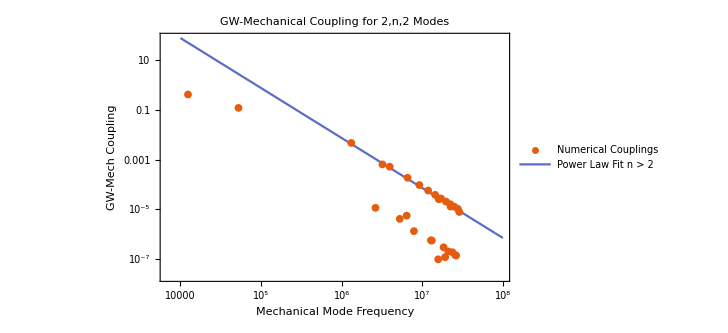

```mathematica
gwcouplingPlot=ListLogLogPlot[{Abs[gwMechCouplings],fitDataf},Joined->{False,True},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{Style["Mechanical Mode Frequency",20],Style["GW-Mech Coupling",20]},PlotLabel->Style["GW-Mechanical Coupling for 2,n,2 Modes",20],PlotLegends->{"Numerical Couplings", "Power Law Fit n > 2"},PlotMarkers->{{Automatic,8},None},ImageSize->Large]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/gw-mech-coupling-with-n.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/gw-mech-coupling-with-n.pdf

```mathematica
"frequency"/."m2n2l2"/.MODES[[1]]
```

1.31542×10^6

```mathematica
Length[fitDataf]
```

10000

```mathematica
gw mech couplings[[30,2]]
```

7.93796×10^-6

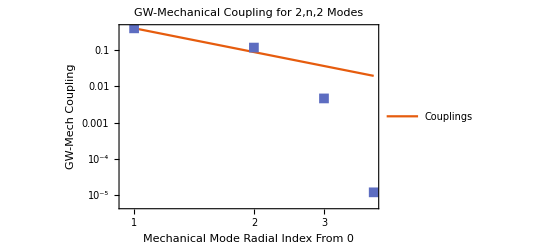

```mathematica
gwcouplingPlot=ListLogLogPlot[{fitDataN,Abs[gw mech couplingsN]},Joined->{True,False},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Radial Index From 0","GW-Mech Coupling"},PlotLabel->"GW-Mechanical Coupling for 2,n,2 Modes",PlotLegends->{"Couplings"},PlotMarkers->{None,{Automatic,10}}]
```

```mathematica
gwmechCouplings={{12409.480767696727,-0.4095476296620654},{52472.260366471055,0.11884790778446398},{1.3154155364814326*^6,0.004663958732297951},{2.628426987072512*^6,-0.000011638622390396924},{3.202725581046194*^6,0.0006427931559582118},{3.9431099403288327*^6,-0.0005192093987980081},{5.257449686392999*^6,4.2005995486028915*^-6},{6.403594191910093*^6,5.6514869355327*^-6},{6.571987757040123*^6,-0.00018686333870526493},{7.886047253282356*^6,-1.3533243397195711*^-6},{9.200384289052246*^6,0.00009539624300492337},{1.1829021288609548*^7,0.000057699935603000196},{1.2807162105872503*^7,-5.789809778507523*^-7},{1.3143360044753645*^7,-5.669443943034488*^-7},{1.4457693234215071*^7,0.00003862861565881665},{1.5771987877461556*^7,1.0028973883051423*^-7},{1.6008892689117782*^7,0.00002572609094250986},{1.7086345844753616*^7,-0.00002765541825165471},{1.8400678491938*^7,3.0364340026920685*^-7},{1.921057499466591*^7,-1.2196111488050526*^-7},{1.9715016457667943*^7,-0.000020773551140826166},{2.1029335366623234*^7,2.0709165831963843*^-7},{2.234366842188835*^7,-0.00001618071086052662},{2.241230950348132*^7,0.00001311956536003365},{2.365800131608084*^7,1.9295130673660808*^-7},{2.497232558119132*^7,0.000012946717706928947},{2.5614043976244684*^7,-1.4932416108196325*^-7},{2.6286660438500475*^7,-1.417214784572068*^-7},{2.7600992719261236*^7,0.000010597402910003818},{2.881575262002291*^7,7.9379638410133*^-6}};
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv",gwmechCouplings,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv

### Even modes m02

```mathematica
(* find out how many coefficients calculated correctly *)
"m8n0l2"/.MODES[[1]]
```

{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46844×10^8,C2→53967.3,D0→6.49089×10^-8,D2→-0.0000227249}

```mathematica
(* just try doing the calculations at the same point as above *)
myns={0,1,2,3,5,6,8,9,10};
modesWithFrequency=Table[{l,Activate[overlapCoupledSpheresArtificialSplitting[{l,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]},{l,2,8}]
```

{{2,0.656981},{3,-0.00161941},{4,0.00317309},{5,-0.0037984},{6,-0.00343638},{7,0.00251495},{8,0.0100299}}

```mathematica
ListPlot[Abs[modesWithFrequency],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Frequency (kHz)","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for l,0,2 Modes"]
```

### Even modes as function of inclination index

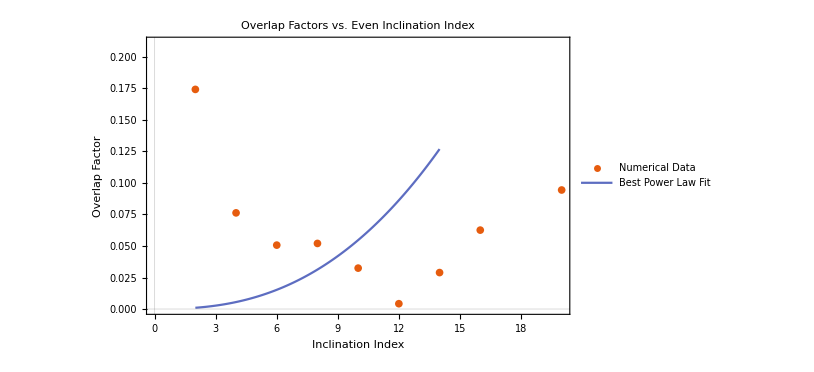

```mathematica
overlapFactors={{2,-1.1235584546663355},{4,-0.4919130249460447},{6,-0.3268342817602289},{8,-0.3354943578086973},{10,-0.20917577786521352},{12,-0.0271156506437399},{14,-0.18642779107256072},{16,-0.40364546211320407},{18,-4.406104286869174},{20,-0.6088732339288097}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors,a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,14,0.1}];
ListPlot[{overlapFactors,fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

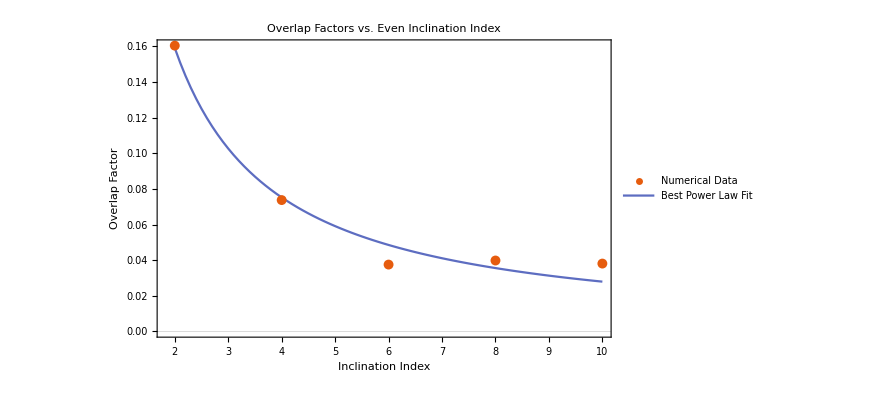

```mathematica
overlapFactors={{2,-1.0341905214781628},{4,-0.4753210516295555},{6,-0.24189868673184403},{8,-0.256644242200031},{10,-0.24555021477047248},{12,-0.26502006088785557},{14,-0.3736925389518085},{16,-0.4816832887383363},{18,-1.3555311566670856},{20,-0.42746618420901317}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors[[1;;5]],a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,10,0.1}];
ListPlot[{overlapFactors[[1;;5]],fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

```mathematica
fits
```

{a→0.336369,b→1.08053}

```mathematica
Activate[omegaMech[2,0,0,innerRadius]]
```

6275.69

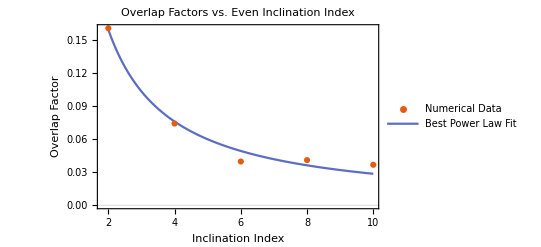

```mathematica
overlapFactors={{2,-1.0335823676574207},{4,-0.47689363383718625},{6,-0.25510648397465097},{8,-0.2632707498816675},{10,-0.2360591937627628},{12,-0.2871287128086725},{14,-0.326570042771931},{16,-0.5052490051342726},{18,-2.0248716117156285},{20,-0.45453124268413475}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors[[1;;5]],a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,10,0.1}];
ListPlot[{overlapFactors[[1;;5]],fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

```mathematica
fits
```

{a→0.333715,b→1.06944}

```mathematica
?omegaMech
```

### Modes 2n0 Single Cavity

```mathematica
(* get point at which to evaluate *)
aitoff[Pi/6,0.0]
```

{0.,2.0944}

```mathematica
"m2n10l0"/.MODES[[1]]
```

{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000718916,C2→-0.418098,D0→0.00225187,D2→-0.00477947}

```mathematica
(*("frequency"/.StringJoin["m2n",ToString[myns[[n]]],"l0"]/.MODES[[1]])*)
```

```mathematica
myns={0,1,2,3,5,6,8,9,10};
modesWithFrequency1Cavity=ParallelTable[{myns[[n]],Activate[overlapfunction[{2,myns[[n]],0,0,1,2,0,1,2},innerRadius,0,0,1,1,wavenumberEM[0,1,2,innerRadius,0],wavenumberEM[0,1,2,innerRadius,0]+0.0033,wavenumberEM[0,1,2,innerRadius,0],wavenumberEM[0,1,2,innerRadius,0]+0.0033,{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},1]]},{n,1,9}]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000555509 and 7.12617×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000548655 and 6.44704×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000555991 and 7.21449×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000541555 and 8.27105×10^-6 for the integral and error estimates.

{{0,1.19042},{1,0.868614},{2,-0.0435272},{3,-0.0563321},{5,-0.00369624},{6,0.00490837},{8,0.0792641},{9,0.00490329},{10,-0.000690746}}

```mathematica
(* just plot radial displacement *)
rdisplacements={};
ns={0,1,2,3,5,6,8,9,10};
Module[{i},For[i=1,i<=9,i++,mvec={2,ns[[i]],0};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Abs[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]}]]];
```

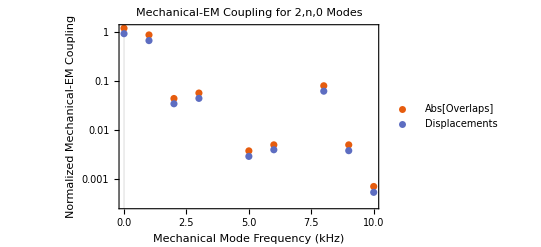

```mathematica
bothplot=ListLogPlot[{Abs[modesWithFrequency1Cavity],rdisplacements},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Frequency (kHz)","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for 2,n,0 Modes",PlotLegends->{"Abs[Overlaps]","Displacements"}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-mode-increase-single-cavity-with-displacements.png",bothplot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-mode-increase-single-cavity-with-displacements.png

### Plot displacements and em fields at surface

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png

```mathematica
myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0]]]];
```

```mathematica
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
f=Interpolation[emSpherical];
```

```mathematica
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/em-2.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/em-2.png

```mathematica
mymode=201;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{{overlaps[[i,1]],overlaps[[i,2]]},Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]];
f=Interpolation[overlapsSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.25}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.25}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/201-overlap.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/201-overlap.png

### Sensitivity plot

#### Load in mechanical couplings

```mathematica
gwmechCouplings=Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv","CSV"];
```

#### SIGNAL

```mathematica
signal power analytic over h0 squared m[wg_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_]:=Ppump*(w1*Q0/(w0*Q1))*w0^4*wg^4*(wm^2-wg^2)^2*(ηmij*Ωm)^2*Pi^2*((wm^2-wg^2)^2+(wm*wg/Qm)^2)^(-2)*(((w1^2-(w0-wg)^2)^2+(w1*(w0-wg)/Q1)^2)^(-1)+((w1^2-(w0+wg)^2)^2+(w1*(w0+wg)/Q1)^2)^(-1))
```

```mathematica
signal psd analytic over h0 squared m[w_,wg_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_]:=Re[Ppump*(w1*Q0/(w0*Q1))*w0^4*wg^4*(wm^2-wg^2)^2*(ηmij*Ωm)^2*Pi^2*((wm^2 - wg^2+I*wg*wm/Qm)^(-1) + (wm^2 - wg^2-I*wg*wm/Qm)^(-1))*((w1^2-w^2)^2+(w*w1/Q1)^2)^(-2) * ((DiracDelta[w+w0-wg]+DiracDelta[w+w0+wg])/(wm^2-(w+w0)^2+I*wm*(w+w0)/Qm) + (DiracDelta[w-w0-wg]+DiracDelta[w-w0+wg])/(wm^2-(w-w0)^2+I*wm*(w-w0)/Qm))]
```

```mathematica
signal power analytic over h0 squared[wg_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_]:=Evaluate[Sum[signal power analytic over h0 squared m[wg,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump],{m,0,100}]]

signal psd analytic over h0 squared[w_,wg_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_]:=Evaluate[Sum[signal psd analytic over h0 squared m[w,wg,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump],{m,0,100}]]
```

#### Pseudo-monochromatic signal

Here we’ll look at a signal spread out over a given bandwidth rather than an exact delta function. We want to see if that kills the sensitivity.

#### THERMAL NOISE

```mathematica
thermal noise psd[w_,w1_,Q1_,Qint_,T_]:=(Q1/Qint)*4*Pi*T*(w*w1/Q1)^2/((w^2-w1^2)^2+(w*w1/Q1)^2)
(*garbageVariableUsedToDefineFunctions=Integrate[thermal noise psd[w,w1,Q1,Qint,T],{w,-Infinity,Infinity}]
thermal noise power[w1_,Q1_,Qint_,T_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]*)
```

#### AMPLIFIER NOISE

```mathematica
amplifier noise psd[w_,w1_]:=4*Pi*w1
```

#### LEAK NOISE

```mathematica
leak noise psd[w_,w0_,w1_,Q0_,Q1_,epsilon_,B0_,V_]:=(4108.24*1.51927*^-15)epsilon^2*(Q1/Q0)*(w0*B0^2*V/(4.0*Q0))*(((w*w0)/Q1)^2/((w^2-w1^2)^2+((w*w0)/Q1)^2))*(10^(-15) + 10^(-11)*w^(-1)+10^(-10)*w^(-2)+10^(-8)*w^(-3))
```

#### MECHANICAL MIXING NOISE

```mathematica
(*mechanical mixing noise psd m[w_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_,T_,V_,Mm_]:=Ppump*(w1*Q0/(4*w0*Q1))*(w0^4*ηmij^2*V^(-2/3)/((w1^2-w^2)^2+(w*w1/Q1)^2))*(4*Pi*T*wm/(Mm*Qm))*((((w)^2-wm^2)^2+((w)*wm/Qm)^2)^(-1))*)

mechanical mixing noise psd m[w_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_,T_,V_,Mm_]:=Ppump*(w1*Q0/(4*w0*Q1))*(w0^4*ηmij^2*V^(-2/3)/((w1^2-w^2)^2+(w*w1/Q1)^2))*(4*Pi*T*wm/(Mm*Qm))*((((w-w0)^2-wm^2)^2+((w-w0)*wm/Qm)^2)^(-1)+(((w+w0)^2-wm^2)^2+((w+w0)*wm/Qm)^2)^(-1))
```

```mathematica
mechanical mixing noise psd[w_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_,T_,V_,Mm_]:=Module[{m},Evaluate[Sum[Abs[mechanical mixing noise psd m[w,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump,T,V,Mm]],{m,0,100}]]]
```

#### TOTAL NOISE

```mathematica
noise psd total[w_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_]:=thermal noise psd[w,w1,Q1,Qint,T]+amplifier noise psd[w,w1]+mechanical mixing noise psd[w,w0,w1,Q0,Q1,Qm,ηmij,Ppump,T,V,Mm]
```

#### SNR

```mathematica
SNR over h0 squared[wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_]:=(signal power analytic over h0 squared[wg,w0,w1,Q0,Q1,Qm,ηmij,Ppump]/noise psd total[w1,w0,w1,Q0,Q1,Qm,Qint,ηmij,Ppump,T,V,Mm])*Sqrt[tint/bandwidth]
```

#### Sensitivity Function

```mathematica
h0 sensitivity[wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_]:=(SNR over h0 squared[wg,w0,w1,Q0,Q1,Qm,Qint,ηmij,Ppump,T,V,Mm,tint,bandwidth])^(-1/2)
```

#### Define all constants in natural units

```mathematica
(* define all your constants *)
(* required constants *)
(* wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_ *)
(* all must be in eV *)

(* physical constants *)
vol=(4/3)*Pi*innerRadius^3;

mySpeedOfLight=299792458.0; (* m/s *)
hbar=6.582*^-16; (* eV s *)
kb=8.617*^-5; (* J/K *)
electriccharge=1.602*^-19 ;

(* frequencies *)
wmC=("frequency"/."m2n0l2"/.MODES[[1]]) * hbar; (* eV *)
w0C=Activate[wavenumberEM[0,1,2,innerRadius,0]]*mySpeedOfLight*hbar; (* eV *)
E0C=(*(30.0*^6)*hbar*mySpeedOfLight *)19.5488;
VC=vol*(hbar*mySpeedOfLight)^(-3);
(*VC=0.03*(hbar*mySpeedOfLight)^(-3);*)
VcavC=(4/3)*Pi*(outerRadius^3 - innerRadius^3)*(hbar*mySpeedOfLight)^(-3);
ηmijC=1.0;
ΩmC=0.4;
Q0C=10^10;
Q1C=10^10;
QmC=10^6;
QintC=10^10;
TC=1.8*kb;
tintC=3600*24*365/hbar;
bandwidthC=10*hbar;
PinC=(w0C/Q0C)*NIntegrate[Norm[electricFieldTEnotrotated[1.0,1,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->4]*E0C^2*(hbar*mySpeedOfLight)^(-3);
B0C = E0C;
epsilonC=10^(-7);
rhoC=matieralDensity*5.61*^35*(hbar*mySpeedOfLight)^(3);
MC=10*5.61*^35;
```

```mathematica
E0C
```

5.9197

```mathematica
TC*electriccharge
```

2.4848×10^-23

#### Plot signal power function

```mathematica
signal power analytic over h0 squared m[wmC,w0C,w0C+wmC,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC]
```

0.

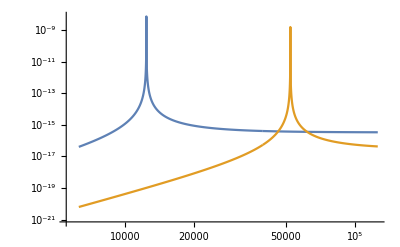

```mathematica
(* integrated power single mode *)
h0Test=10^(-20);
IntegratedSignalPowerValues=Table[{10^myf,h0Test^2*signal power analytic over h0 squared m[hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC]},{myf,3.8,5.1,0.0001}];
IntegratedSignalPowerValues2=Table[{10^myf,h0Test^2*signal power analytic over h0 squared m[hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*(("frequency"/."m2n0l2"/.MODES[[1]])*hbar)/(("frequency"/."m2n1l2"/.MODES[[1]])*hbar),ηmijC,gwmechCouplings[[2,2]],PinC]},{myf,3.8,5.1,0.0001}];
ListLogLogPlot[{IntegratedSignalPowerValues,IntegratedSignalPowerValues2},Joined->True,PlotRange->All]
```

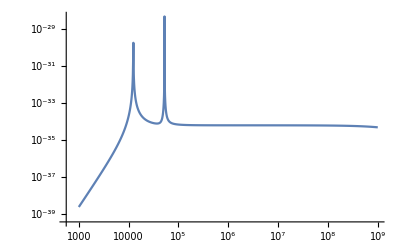

```mathematica
(* total integrated *)
TotalIntegratedSignalPowerValues=Table[{10^myf,electriccharge*h0Test^2*signal power analytic over h0 squared[hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,ηmijC,PinC]},{myf,3,9,0.005}];
ListLogLogPlot[TotalIntegratedSignalPowerValues,Joined->True]
```

#### Plot individual noise functions

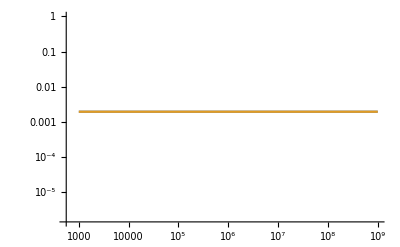

```mathematica
(* thermal EM PSD *)
ThermalEMPSDValues=Table[{10^myf,thermal noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf,Q1C,QintC,TC]},{myf,3,9,0.01}];
ThermalEMPSDValuesold=Table[{10^myf,thermal noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf,Q1C,QintC,TC]},{myf,3,9,0.01}];
ListLogLogPlot[{ThermalEMPSDValues,ThermalEMPSDValuesold},Joined->True]
```

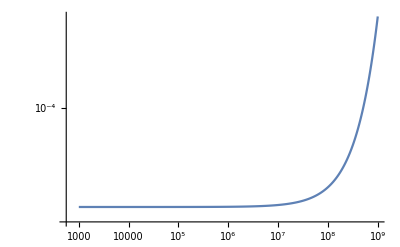

```mathematica
(* thermal EM PSD *)
AmplifierPSDValues=Table[{10^myf,amplifier noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf]},{myf,3,9,0.01}];
ListLogLogPlot[AmplifierPSDValues,Joined->True]
```

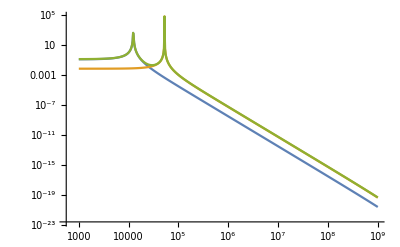

```mathematica
(* thermal Mechanical PSD Single Mode *)
SingleModeThermalMechanicalPSDValues=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC,TC,VC,MC]},{myf,3,9,0.01}];
SingleModeThermalMechanicalPSDValues2=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/."m2n1l2"/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}];
SingleModeThermalMechanicalPSDValues3=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC,TC,VC,MC]+mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/."m2n1l2"/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}];
ListLogLogPlot[{SingleModeThermalMechanicalPSDValues,SingleModeThermalMechanicalPSDValues2,SingleModeThermalMechanicalPSDValues3},Joined->True]
```

```mathematica
(* plot all single mode signals *)
SingleModeSignals={};
Module[{i},For[i=0,i<=100,i++,AppendTo[SingleModeSignals,Table[{10^myf,electriccharge*mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/.StringJoin["m2n",ToString[i],"l2"]/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[i],"l2"]/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}]]]];
Print[Length[SingleModeSignals]]
```

101

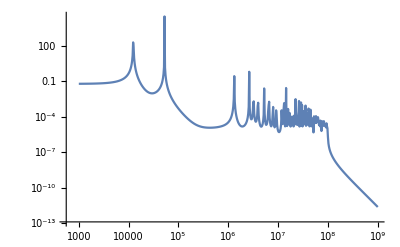

```mathematica
(* thermal Mechanical PSD *)
TotalThermalMechanicalPSDValues=Table[{10^myf,mechanical mixing noise psd[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,ηmijC,PinC,TC,VC,VcavC*rhoC]},{myf,3,9,0.01}];
ListLogLogPlot[TotalThermalMechanicalPSDValues,Joined->True]
```

```mathematica
(* total noise PSD *)
```

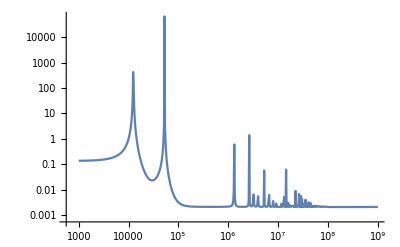

```mathematica
TotalNoisePSDValues=Table[{10^myf, noise psd total[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC]},{myf,3,9,0.01}];
ListLogLogPlot[TotalNoisePSDValues,Joined->True]
```

#### Plot all noise functions together

```mathematica
totalsignalValuesWHz=Table[{10^myf,10^(-40)*signal power analytic over h0 squared[hbar*10^myf,w0C,w0C+wmC,Q1C,Q1C,QmC,ηmijC,PinC]},{myf,3,9,0.01}];
```

```mathematica
allplots=SingleModeSignals;
ThermalEMPSDValuesWHz=ThermalEMPSDValues;
TotalThermalMechanicalPSDValuesWHz=TotalThermalMechanicalPSDValues;
AmplifierPSDValuesWHz=AmplifierPSDValues;
TotalNoisePSDValuesWHz=TotalNoisePSDValues;

ThermalEMPSDValuesWHz[[All,2]]=ThermalEMPSDValuesWHz[[All,2]]*electriccharge/(4*Pi);
TotalThermalMechanicalPSDValuesWHz[[All,2]]=TotalThermalMechanicalPSDValuesWHz[[All,2]]*electriccharge;
AmplifierPSDValuesWHz[[All,2]]=AmplifierPSDValuesWHz[[All,2]]*electriccharge/(4*Pi);
TotalNoisePSDValuesWHz[[All,2]]=TotalNoisePSDValuesWHz[[All,2]]*electriccharge;

PrependTo[allplots,TotalThermalMechanicalPSDValuesWHz];
PrependTo[allplots,ThermalEMPSDValuesWHz];
PrependTo[allplots,AmplifierPSDValuesWHz];
PrependTo[allplots,totalsignalValuesWHz];
Print[Length[allplots]]
myPlotStyle={{Purple,Thick},{Orange,Thick},{RGBColor[9/255,121/255,19/255],Thick},{RGBColor[9/255,54/255,121/255],Thick}};
Module[{i},For[i=0,i<=100,i++,AppendTo[myPlotStyle,{RGBColor[9/255,54/255,121/255],Dashed,Opacity[0.5]}]]];
```

105

```mathematica
(* add in scaling lines for mechanical mixing *)
mechNoiseScalingFunction[frequency_]:=electriccharge*mechanical mixing noise psd m[w0C+("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,w0C,w0C+("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]*(("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])/(frequency))^4
```

```mathematica
scalingValues=Table[{10^myf, mechNoiseScalingFunction[10^myf]},{myf,3,9,0.01}];
```

```mathematica
PrependTo[allplots,scalingValues];
PrependTo[myPlotStyle,{RGBColor[9/255,54/255,121/255],Thick,Dashing[{0.02,0.004,0.004,0.004}]}];
```

```mathematica
Print[Length[allplots]]
```

106

```mathematica
PrependTo[allplots,TotalNoisePSDValuesWHz];
PrependTo[myPlotStyle,{Red,Thick}];
```

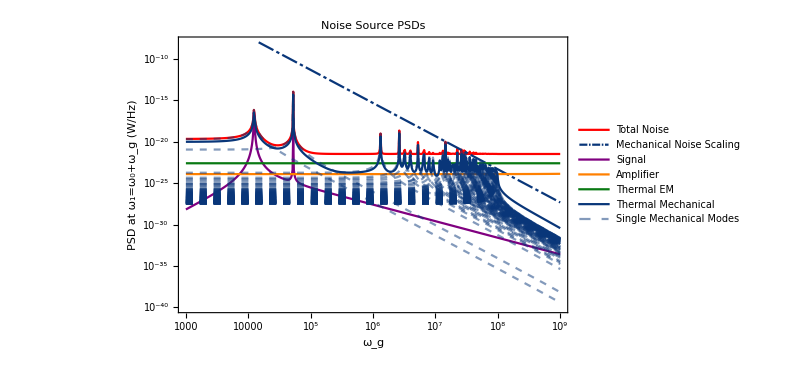

```mathematica
noisesources=ListLogLogPlot[allplots,Joined->True,PlotStyle->myPlotStyle,PlotTheme->"Scientific",PlotLabel->Style["Noise Source PSDs",22],ImageSize->{600,400},PlotLegends->{"Total Noise","Mechanical Noise Scaling","Signal","Amplifier","Thermal EM","Thermal Mechanical","Single Mechanical Modes"},FrameLabel->{Style["ω_g",20],Style["PSD at ω_1=ω_0+ω_g (W/Hz)",20]},PlotRange->{{10^3,10^9},{10^-40,10^-8}}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/noise-sources.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/noise-sources.png

#### Plot sensitivity

```mathematica
(* total sensitivity *)
SensitivityValues=Table[{10^myf,h0 sensitivity[hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC*(w0C+hbar*10^myf)/(Q1C*hbar*10^myf),bandwidthC]},{myf,3,9,0.001}];
```

```mathematica
scanningSensitivity=SensitivityValues;
```

```mathematica
h0 sensitivity[hbar*10^4,w0C,w0C+hbar*12000,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC,bandwidthC]
```

3.30943×10^-18

```mathematica
wmC
```

8.16792×10^-12

```mathematica
fixedmodeSensitivity=Table[{10^myf,h0 sensitivity[hbar*10^myf,w0C,w0C+("frequency"/."m2n0l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC,bandwidthC]},{myf,3,9,0.01}];
```

```mathematica
pbh parameter space[mp_,wp_]:=10*^-31 * (mp/10^-11)^(4/3)*(wp/10^9)^(2/3)
```

```mathematica
pbh5=Table[{10^myf,pbh parameter space[10^-5,10^myf]},{myf,3,8.2,0.005}];
pbh6=Table[{10^myf,pbh parameter space[10^-6,10^myf]},{myf,3,8.2,0.005}];
pbh8=Table[{10^myf,pbh parameter space[10^-8,10^myf]},{myf,3,9,0.005}];
pbh11=Table[{10^myf,pbh parameter space[10^-11,10^myf]},{myf,3,9,0.005}];
```

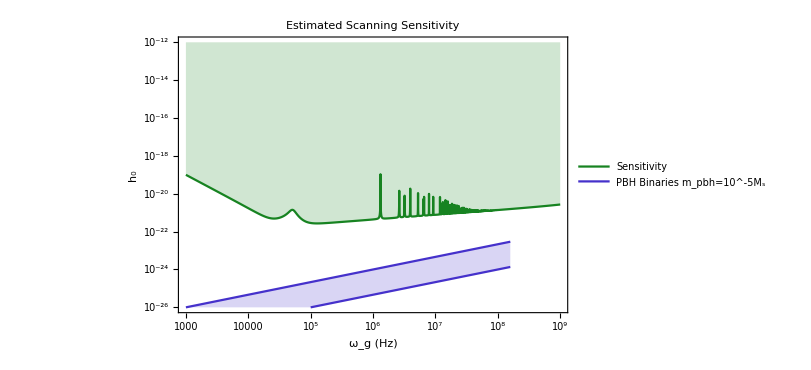

```mathematica
ListLogLogPlot[{scanningSensitivity,pbh5,pbh6},Joined->True,PlotStyle->{{RGBColor[23/255,131/255,33/255]},{RGBColor[69/255,49/255,203/255]},{RGBColor[69/255,49/255,203/255]}},PlotTheme->"Scientific",PlotLabel->Style["Estimated Scanning Sensitivity",25],FrameLabel->{Style["ω_g (Hz)",25],Style["h_0",25]},Filling->{1->Top,2->{3}},FillingStyle->{{RGBColor[255/255,84/255,26/255]},{RGBColor[69/255,49/255,203/255]}},ImageSize->{600,400},PlotLegends->Placed[{Style["Sensitivity",18],Style["PBH Binaries m_pbh=10^-5M_s",18]},{0.25,0.83}],PlotRange->{{10^3,10^9},{10^-26,10^-12}}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/sensitivity-whoa.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/sensitivity-whoa.png

```mathematica
cartvec = Simplify[spherevec2cartvec[{Ar,Aθ,Aϕ},{r,θ,ϕ}]]
```

{Aθ Cos[θ] Cos[ϕ]+Ar Cos[ϕ] Sin[θ]-Aϕ Sin[ϕ],Aϕ Cos[ϕ]+(Aθ Cos[θ]+Ar Sin[θ]) Sin[ϕ],Ar Cos[θ]-Aθ Sin[θ]}

```mathematica
TeXForm[cartvec[[2]]]
```

\sin (\phi ) (\text{A$\theta $} \cos (\theta )+\text{Ar} \sin (\theta ))+\text{A$\phi $} \cos (\phi )

```mathematica
?electricField
```

```mathematica
Simplify[Cross[electricField[1,1,1,m,n,p,1,wavenumberEM[m,n,p,1,1],1,θ,ϕ,0,0,0],magneticField[1,1,1,m,n,p,1,wavenumberEM[m,n,p,1,1],1,θ,ϕ,0,0,0]]]
```

{-1/(16 SphericalBesselJDerivZero[n,p])Csc[θ]^2 (1) SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]] (SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]+(SphericalBesselJ[-1+n,SphericalBesselJDerivZero[n,p]]-SphericalBesselJ[1+n,SphericalBesselJDerivZero[n,p]]) SphericalBesselJDerivZero[n,p]),(Cos[m 1]^2 1^4 2 √1 1^2)/(2 SphericalBesselJDerivZero[n,p]),(m Csc[θ]^2 LegendreP[1] (1) Sin[2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]^2)/(4 √(Sin[θ]^2) SphericalBesselJDerivZero[n,p])}
 |  |  |  |

```mathematica
poynting=%;
```

```mathematica
poynting[[1]]
```

-1/(16 SphericalBesselJDerivZero[n,p])Csc[θ]^2 ((2+4 m^2+4 n+2 n^2+2 (1+n)^2 Cos[2 θ]+(-4 m^2+2 (1+n)^2) Cos[2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+2 n Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+n^2 Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]+2 n Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]+n^2 Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]) LegendreP[n,m,Cos[θ]]^2+16 (-1+m-n) (1+n) Cos[θ] Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]^2 LegendreP[n,m,Cos[θ]] LegendreP[1+n,m,Cos[θ]]+8 (1-m+n)^2 Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]^2 LegendreP[1+n,m,Cos[θ]]^2) SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]] (SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]+(SphericalBesselJ[-1+n,SphericalBesselJDerivZero[n,p]]-SphericalBesselJ[1+n,SphericalBesselJDerivZero[n,p]]) SphericalBesselJDerivZero[n,p])

```mathematica
Activate[Simplify[Cross[electricField[1,1,1,0,2,2,1,wavenumberEM[m,n,p,1,0],1,θ,ϕ,0,0,0],magneticField[1,1,0,0,1,2,1,wavenumberEM[0,1,2,1,0],1,θ,ϕ,0,0,0]]]]
```

{0,0,0.0125671 √(Sin[θ]^2) (6.94817×10^-16 Cos[θ]^2+0.254625 (1+3 Cos[2 θ])-9.48372×10^-9 (1.28375 Cos[θ]^2-0.128375 Sin[θ]^2))}

```mathematica
sphericalBesselJDerivZero//TableForm//TeXForm
```

\begin{array}{cccccccccc}
 1.5708 & 4.71239 & 7.85398 & 10.9956 & 14.1372 & 17.2788 & 20.4204 & 23.5619 & 26.7035 & 29.8451 \\
 0. & 2.74371 & 6.11676 & 15.6439 & 9.31662 & 18.7963 & 12.4859 & 21.9455 & 25.0928 & 28.2389 \\
 0. & 3.87024 & 10.713 & 7.44309 & 13.9205 & 17.1027 & 20.272 & 23.4337 & 26.5906 & 29.7442 \\
 0. & 4.97342 & 8.72175 & 12.0636 & 15.3136 & 18.5242 & 21.7139 & 24.8911 & 28.0601 & \text{} \\
 0. & 6.06195 & 9.96755 & 13.3801 & 16.6742 & 19.9154 & 23.1278 & 26.3224 & 29.5054 & \text{} \\
 0. & 7.14023 & 11.189 & 14.6701 & 18.0085 & 21.2815 & 24.5178 & 27.7313 & \text{} & \text{} \\
 0. & 8.21084 & 12.3915 & 15.9387 & 19.3212 & 22.6263 & 25.8873 & 29.1205 & \text{} & \text{} \\
 0. & 9.27546 & 13.5787 & 17.1896 & 20.6154 & 23.9528 & 27.239 & \text{} & \text{} & \text{} \\
 0. & 10.3352 & 14.7534 & 18.4254 & 21.8939 & 25.2633 & 28.5749 & \text{} & \text{} & \text{} \\
 0. & 11.391 & 15.9174 & 19.6485 & 23.1586 & 26.5598 & 29.8967 & \text{} & \text{} & \text{} \\
\end{array}

```mathematica
Bfieldold = FullSimplify[magneticField[f,1,0,m,n,p,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0,θ>=0,θ<Pi}]
```

{-1/(2 k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ]^2 ((2-2 m^2+3 n+n^2+n (1+n) Cos[2 θ]) LegendreP[n,m,Cos[θ]]+2 (-1+m-n) ((3+2 n) Cos[θ] LegendreP[1+n,m,Cos[θ]]+(-2+m-n) LegendreP[2+n,m,Cos[θ]])) SphericalBesselJ[n,k r],-1/(k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ] ((1+n) Cos[θ] LegendreP[n,m,Cos[θ]]+(-1+m-n) LegendreP[1+n,m,Cos[θ]]) ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]),-(f m Csc[θ] LegendreP[n,m,Cos[θ]] Sin[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]))/(k r)}

```mathematica
Bfield[[1]]//TraditionalForm
```

-(f csc^2(θ) nk r ((-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))) cos(m tan^-1(sin(θ) cos(ϕ),sin(θ) sin(ϕ))))/(2 k r)

```mathematica
Bfieldnew= FullSimplify[magneticField[f,1,0,m,n,p,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0,θ>=0,θ<Pi}]
```

{-1/(2 k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ]^2 ((2-2 m^2+3 n+n^2+n (1+n) Cos[2 θ]) LegendreP[n,m,Cos[θ]]+2 (-1+m-n) ((3+2 n) Cos[θ] LegendreP[1+n,m,Cos[θ]]+(-2+m-n) LegendreP[2+n,m,Cos[θ]])) SphericalBesselJ[n,k r],1/(k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] (-((1+n) Cot[θ] LegendreP[n,m,Cos[θ]])+(1-m+n) Csc[θ] LegendreP[1+n,m,Cos[θ]]) Sign[Csc[θ]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]),-(f m Csc[θ] LegendreP[n,m,Cos[θ]] Sin[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]))/(k r)}

```mathematica
FullSimplify[Bfieldold[[1]]]//TraditionalForm
```

-(f csc^2(θ) nk r ((-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))) cos(m tan^-1(sin(θ) cos(ϕ),sin(θ) sin(ϕ))))/(2 k r)

```mathematica
FullSimplify[(2-2*m^2+3*n+n^2+n*(1+n)*Cos[2*θ])*LegendreP[n,m,Cos[θ]]+2*(-1+m-n)*((3+2*n)*Cos[θ]*LegendreP[1+n,m,Cos[θ]]+(-2+m-n)*LegendreP[2+n,m,Cos[θ]])]//TraditionalForm
```

(-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))

```mathematica
filename=StringJoin["eta-",ToString[200],"-012-012-EMpol-pion4pion4-minpion4pion4-0-variable-mechanical-euler-alpha-beta-hi-res-GWplus-newsigns.txt"];
(* import data *)

(* name data floats *)
For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]];
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
```

```mathematica
overlapsSpherical
```

{{0.01,-3.13159,0.0514715},{0.01,-3.03159,0.0514728},{0.01,-2.93159,0.0510532},{0.01,-2.83159,0.0525634},{0.01,-2.73159,0.0452514},{0.01,-2.63159,0.0487506},{0.01,-2.53159,0.0508667},{0.01,-2.43159,0.0466596},{0.01,-2.33159,0.0469519},{0.01,-2.23159,0.0420965},{0.01,-2.13159,0.0404165},{0.01,-2.03159,0.04079},{0.01,-1.93159,0.0430498},{0.01,-1.83159,0.0527355},{0.01,-1.73159,0.0609038},{0.01,-1.63159,0.0679025},{0.01,-1.53159,0.0745204},{0.01,-1.43159,0.0856176},{0.01,-1.33159,0.0970298},{0.01,-1.23159,0.108656},{0.01,-1.13159,0.121781},{0.01,-1.03159,0.130203},{0.01,-0.931593,0.146892},{0.01,-0.831593,0.160369},{0.01,-0.731593,0.171999},{0.01,-0.631593,0.182991},{0.01,-0.531593,0.20144},{0.01,-0.431593,0.214097},{0.01,-0.331593,0.21723},{0.01,-0.231593,0.221862},{0.01,-0.131593,0.22732},{0.01,-0.0315927,0.226306},{0.01,0.0684073,0.229011},{0.01,0.168407,0.225292},{0.01,0.268407,0.218279},{0.01,0.368407,0.217001},{0.01,0.468407,0.205516},{0.01,0.568407,0.200479},{0.01,0.668407,0.184754},{0.01,0.768407,0.172882},{0.01,0.868407,0.158297},{0.01,0.968407,0.14022},{0.01,1.06841,0.128975},{0.01,1.16841,0.116107},{0.01,1.26841,0.104906},{0.01,1.36841,0.0905215},{0.01,1.46841,0.0799991},{0.01,1.56841,0.0694948},{0.01,1.66841,0.0638293},{0.01,1.76841,0.0598982},{0.01,1.86841,0.0521484},{0.01,1.96841,0.0453277},{0.01,2.06841,0.0432129},{0.01,2.16841,0.0446645},{0.01,2.26841,0.044346},{0.01,2.36841,0.0495516},{0.01,2.46841,0.0483699},{0.01,2.56841,0.0484799},{0.01,2.66841,0.0494587},{0.01,2.76841,0.0501749},{0.01,2.86841,0.0517916},{0.01,2.96841,0.055584}}

```mathematica
ListContourPlot[overlapsSpherical,Contours->7]
```

-Graphics-

```mathematica
overlaps
```

{{0.01,-3.13159,-0.331887},{0.01,-3.03159,-0.331895},{0.01,-2.93159,-0.329189},{0.01,-2.83159,-0.338927},{0.01,-2.73159,-0.291779},{0.01,-2.63159,-0.314343},{0.01,-2.53159,-0.327987},{0.01,-2.43159,-0.30086},{0.01,-2.33159,-0.302744},{0.01,-2.23159,-0.271437},{0.01,-2.13159,-0.260605},{0.01,-2.03159,-0.263013},{0.01,-1.93159,-0.277584},{0.01,-1.83159,-0.340037},{0.01,-1.73159,-0.392706},{0.01,-1.63159,-0.437833},{0.01,-1.53159,-0.480505},{0.01,-1.43159,-0.55206},{0.01,-1.33159,-0.625645},{0.01,-1.23159,-0.700613},{0.01,-1.13159,-0.785243},{0.01,-1.03159,-0.839542},{0.01,-0.931593,-0.947157},{0.01,-0.831593,-1.03406},{0.01,-0.731593,-1.10904},{0.01,-0.631593,-1.17992},{0.01,-0.531593,-1.29888},{0.01,-0.431593,-1.38049},{0.01,-0.331593,-1.40069},{0.01,-0.231593,-1.43056},{0.01,-0.131593,-1.46575},{0.01,-0.0315927,-1.45921},{0.01,0.0684073,-1.47666},{0.01,0.168407,-1.45267},{0.01,0.268407,-1.40746},{0.01,0.368407,-1.39921},{0.01,0.468407,-1.32516},{0.01,0.568407,-1.29268},{0.01,0.668407,-1.19129},{0.01,0.768407,-1.11474},{0.01,0.868407,-1.02069},{0.01,0.968407,-0.904134},{0.01,1.06841,-0.831627},{0.01,1.16841,-0.748656},{0.01,1.26841,-0.676428},{0.01,1.36841,-0.58368},{0.01,1.46841,-0.515832},{0.01,1.56841,-0.4481},{0.01,1.66841,-0.411569},{0.01,1.76841,-0.386222},{0.01,1.86841,-0.336251},{0.01,1.96841,-0.292272},{0.01,2.06841,-0.278636},{0.01,2.16841,-0.287995},{0.01,2.26841,-0.285941},{0.01,2.36841,-0.319507},{0.01,2.46841,-0.311888},{0.01,2.56841,-0.312597},{0.01,2.66841,-0.318908},{0.01,2.76841,-0.323526},{0.01,2.86841,-0.33395},{0.01,2.96841,-0.358404},{0.01,3.06841,-0.328005}}

```mathematica
MODES
```

{"m2n0l0" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.187854422191361, 
   "C2" -> 0.00007288525020600044, "D0" -> 0.14064870856014164, "D2" -> -0.0016763116094842038}, 
 "m2n0l1" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.1871795995800207, 
   "C2" -> 0.00007286276945299726, "D0" -> 0.1406053268214713, "D2" -> -0.0016757945673235104}, 
 "m2n0l2" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.7301393096411153, 
   "C2" -> 0.0000914145055749922, "D0" -> 0.17559037861002963, "D2" -> -0.002086356990172635}, 
 "m2n1l0" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 2.742256905256485, 
   "C2" -> 0.9136662957787578, "D0" -> -0.45444949931493, "D2" -> 0.6993944473689281}, 
 "m2n1l1" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 2.7343377577490613, 
   "C2" -> 0.9110277909198716, "D0" -> -0.45313713043626974, "D2" -> 0.6973747212871116}, 
 "m2n1l2" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 0.00019848543540139832, 
   "C2" -> 0.00006596031100592674, "D0" -> -0.000032991787061125105, "D2" -> 0.000050229132008137565}, 
 "m2n2l0" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.00019928622767316696, 
   "C2" -> -0.0001323100498101604, "D0" -> -0.05206069572666428, "D2" -> 2.0719368889433776}, 
 "m2n2l1" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.0001983103905660513, 
   "C2" -> -0.000131662172343882, "D0" -> -0.05180577214611634, "D2" -> 2.0617913162992476}, 
 "m2n2l2" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.00012137966275508659, 
   "C2" -> -0.00008025550985915276, "D0" -> -0.031702676340497296, "D2" -> 1.2668098099843839}, 
 "m2n3l0" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 0.00012118635342580138, 
   "C2" -> 0.0001501191215219726, "D0" -> -0.026176835363973885, "D2" -> 2.062920639911493}, 
 "m2n3l1" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 0.0001213945644133911, 
   "C2" -> 0.00015037704206883787, "D0" -> -0.026221809938990235, "D2" -> 2.0664649560132085}, 
 "m2n3l2" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 2.912990605731566, 
   "C2" -> 3.591014562389404, "D0" -> -630.4896220361462, "D2" -> 49888.518779330254}, 
 "m2n4l0" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 2.922460674469915, 
   "C2" -> -1.7305656595610233, "D0" -> 0.015702441701182426, "D2" -> 0.0095915793150132}, 
 "m2n4l1" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 2.9044508477362516, 
   "C2" -> -1.7199009522641233, "D0" -> 0.015605674529324744, "D2" -> 0.00953247067308189}, 
 "m2n4l2" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 0.00001362540746091902, 
   "C2" -> -8.064094780332282*^-6, "D0" -> 7.335703577965818*^-8, "D2" -> 4.481153354518136*^-8}, 
 "m2n5l0" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, "C0" -> 0.00001359163072670708, 
   "C2" -> -0.000013150608561237183, "D0" -> -0.01739166868263313, "D2" -> 2.0619496936531063}, 
 "m2n5l1" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, "C0" -> 0.000013644147658708935, 
   "C2" -> -0.000013201421420229624, "D0" -> -0.017458868645608132, "D2" -> 2.069916895972696}, 
 "m2n5l2" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, 
   "C0" -> 0.3562646937253713/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "C2" -> -0.34470459252290875/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "D0" -> -455.87153161955956/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "D2" -> 54047.95722142333/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]]}}

```mathematica
garbageVariableUsedToDefineFunctions=Evaluate[c0*Grad[auxϕ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+d0*Grad[auxϕT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+c1*Cross[{r,0,0},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+d1*Cross[{r,0,0},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+c2*Curl[Cross[{r,0,0},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"]+d2*Curl[Cross[{r,0,0},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"]];
displacementVecQnotrotated2[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

```mathematica
displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]-displacementVecQnotrotated2[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]
```

{0,0,0}

```mathematica
1/(50*10^(-9))
```

20000000

```mathematica
20000000/10^3
```

20000

# Scratch-book

```mathematica
FullSimplify[1/(wm^2-wg^2+I*wm*wg/Qm)^2+1/(wm^2-wg^2-I*wm*wg/Qm)^2+2/((wm^2-wg^2)^2+(wm*wg/Qm)^2)]
```

(4 Qm^4 (wg^2-wm^2)^2)/((wg^2 wm^2+Qm^2 (wg^2-wm^2)^2)^2)

```mathematica
Series[signal power analytic over h0 squared m[wg,w0,w1,wm,Q0,Q1,Qm,ηmij,Ωm,Pin]/.{wg->wm+ϵ},{ϵ,0,2}]
```

(4 π^2 Pin Q0 Qm^4 w0^3 w1 (1/((w1^2-(w0-wm)^2)^2+(w1^2 (w0-wm)^2)/Q1^2)+1/((w1^2 (w0+wm)^2)/Q1^2+(w1^2-(w0+wm)^2)^2)) ηmij^2 Ωm^2 ϵ^2)/(Q1 wm^2)+O[ϵ]^3

```mathematica
Simplify[Exp[-b^2*Exp[2*I*t]]]
```

ⅇ^(-b^2 ⅇ^(2 ⅈ t))

```mathematica
Simplify[Cos[b^2*Sin[2*t]]]
```

Cos[b^2 Sin[2 t]]

```mathematica
Limit[Integrate[Exp[a^2]/(m-z+a),{a,z,b}],{b->Infinity}]
```

lim_(b→∞) ∫_z^b (ⅇ^(a^2))/(a+m-z)ⅆa

```mathematica
2*Pi/0.1
```

62.8319